# Vector WKB/PIA expansion for a system of coupled differential equations

## License and author info

Copyright © Ibai Asensio, 2025.

This Mathematica code computes the vector/multidimensional adiabatic WKB/phase-integral approximation for a specific system of coupled differential equations, and compares it with the exact (numerical) solution. The theory was developed in Fulling (1975). (See Fulling (1979) and Skorupski (2008) as well.) The example we solve was also proposed by Fulling in his 1975 paper. Here we implement and reproduce Fulling’s results for the original example (introducing two arbitrary parameters), and go beyond it by reaching second adiabatic order — fully analytic! The expansion could be easily continued to arbitrary adiabatic order, if desired, but closed-form expressions are not guaranteed.

This code is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License, v3.0, as published by the Free Software Foundation. For more information, visit: https://www.gnu.org/licenses/

Developed by Ibai Asensio as part of the master thesis: ‘Towards Adiabatic States for Perturbations in Anisotropic Spacetimes. Analytical Approximations for Coupled Differential Equations in Quantum Fields in Curved Spacetimes’.

Supervisors:		Béatrice Bonga (Radboud Universiteit)
				Javier Olmedo (Universidad de Granada)
Second reader:	Wim J.P. Beenakker (Radboud Universiteit)

Part of a the  odes-approximations  project; find more accompanying files on the project’s repository.
If you find this code useful, or have any thoughtful feedback, you are encouraged to contact the author and let him know.

## Preamble

## Variables and notation

#### Clearing variables

```mathematica
ClearAll["Global`*"]
```

#### Notation short guide

- For a matrix X:	 X[t]->Symbolic matrix
mX[t]->True matrix X
X[i,j]==mX[[i,j]]->Components
- For a vector x:	x[t]->Symbolic vector
vx[t]->True vector x(t)
x[i]==vx[[i]]->Components
- Constants:		ζ_(n,k,±l)->	 n: order n,
						 k: eigenspace k,
						 ±: solution +/- (i.e. j->±ⅈ)
						 l: proportional to eigenvector e_k^(l)[t]

Semi-numeric updates (or after that) colored in purple.

## Shortcuts

#### Plotting styles

```mathematica
style0th={
{Dashing[Tiny],ColorData[97,1]},{Dashing[Tiny],ColorData[97,2]},{Dashing[Tiny],ColorData[97,3]}};
```

```mathematica
style1st={
{Dashing[Small],ColorData[97,1]},{Dashing[Small],ColorData[97,2]},{Dashing[Small],ColorData[97,3]}};
```

```mathematica
style2nd={
{Dashing[Large],ColorData[97,1]},{Dashing[Large],ColorData[97,2]},{Dashing[Large],ColorData[97,3]}};
```

```mathematica
stylenum={{SolidData,ColorData[97,1]},{SolidData,ColorData[97,2]},{SolidData,ColorData[97,3]}};
```

```mathematica
stylecompare={SolidData,Dashed,SolidData,Dashed,SolidData,Dashed};
```

```mathematica
stylecompare2={SolidData,SolidData,SolidData,Dashed,Dashed,Dashed};
```

To mix some of these styles, use (e.g.)

Flatten[{style0th,style1st,style2nd},1]

#### Linear algebra shortcuts

Quick identity matrix:

```mathematica
II:=IdentityMatrix[dim];
```

Quick zero matrix:

```mathematica
m0:=Array[0&,{dim,dim}];
```

Quick zero vector:

```mathematica
v0:=Array[0&,dim];
```

#### Relevant time domain

```mathematica
relevantdomain={t,ti,tf}
```

{t,ti,tf}

## Custom functions

### Klein-Gordon product

These functions adopt the notation v⃗=(x_1,x_2,...,v_1,v_2,...) for elements of the phase space, and implement the Klein-Gordon inner product ((v⃗)^(1),(v⃗)^(2))=ⅈ(v⃗)^(1)Ω ((v⃗)^(2))* , with Ω the corresponding N-dimensional symplectic matrix.

```mathematica
SymplecticMatrix[n_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[n]]
```

```mathematica
PhaseSpaceArray[x_]:={Array[{x}[[#]]&,Length[{x}]],Array[D[{x}[[#]],t]&,Length[{x}]]}//Flatten
```

```mathematica
KleinGordonProduct[va_,vb_]:=If[
(*Condition:*)Length[va]===Length[vb],
(*Then:*)ⅈ PhaseSpaceArray[va].SymplecticMatrix[Length[PhaseSpaceArray[va]]/2].Conjugate[PhaseSpaceArray[vb]],
(*Else:*)Print["Dimensions of vectors do not agree."]]
```

```mathematica
KleinGordonNorm[v_]:=KleinGordonProduct[v,v]
```

### Linear algebra

#### Changes of basis

Build a linear operator from a vector set (i.e. the linear operator which transforms the basis vectors into the vector set provided to the function):

```mathematica
LinearOperator[vectorset_]:=Transpose[vectorset]
```

Change-of-basis matrix (the same operation as building a linear operator):

```mathematica
ChangeofBasisMatrix[newbasis_]:=Transpose[newbasis]
```

Change of basis for a matrix:

```mathematica
ChangedBasisMatrix[M_,newbasis_]:=Inverse[Transpose[newbasis]].M.Transpose[newbasis]//Simplify
```

Change of basis for a vector:

```mathematica
ChangedBasisVector[v_,newbasis_]:=Inverse[Transpose[newbasis]].v//Simplify
```

#### Some extra vector and matrix operations

Also, since Mathematica doesn’t distinguish between vectors and dual vectors (the built-in Transpose function doesn’t have any effect) some vector and matrix operations are not included by default. For example:

Bra-ket operator (i.e. dual vector acting on a vector):

```mathematica
Braket[u_,v_]:=({v}.Transpose[{u}])[[1]][[1]]
```

(This has the same effect as the Dot operation. However, the next functions are not.)

Ket-bra operator (i.e. vector acting on a dual vector):

```mathematica
Ketbra[u_,v_]:=Transpose[{u}].{v}
```

Vector-matrix multiplication:

```mathematica
DotVectorMatrix[v_,M_]:=
If[Length[v]==Length[M],
Array[∑_(l=1)^Length[v] v[[l]]M[[l,#]]&,Length[v]],
(* Else: *)
 Print["Error: Dimensions doesn't agree."]
]
```

#### Defining vectors and matrices

Constant vectors and matrices:

```mathematica
DefineVector[entriesName_,dim_]:=Array[entriesName[#]&,dim]
```

```mathematica
DefineMatrix[entriesName_,{dimRows_,dimCols_}]:=Array[entriesName[#1,#2]&,{dimRows,dimCols}]
```

```mathematica
DefineSquareMatrix[entriesName_,dim_]:=Array[entriesName[#1,#2]&,{dim,dim}]
```

Variable-dependent vectors and matrices:

```mathematica
DefineVectorVar[entriesName_,var_,dim_]:=Array[entriesName[#][var]&,dim]
```

```mathematica
DefineMatrixVar[entriesName_,var_,{dimRows_,dimCols_}]:=Array[entriesName[#1,#2][var]&,{dimRows,dimCols}]
```

```mathematica
DefineSquareMatrixVar[entriesName_,var_,dim_]:=Array[entriesName[#1,#2][var]&,{dim,dim}]
```

### Numerical help: NPrimitive functions

#### NPrimitive

```mathematica
NPrimitive[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_}]:=NDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax}]
```

#### NPrimitiveValue

```mathematica
NPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_}]:=NDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax}]
```

#### ParametricNPrimitive

```mathematica
ParametricNPrimitive[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]
```

```mathematica
ParametricNPrimitiveIC[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==ic},primitiveName,{var,varMin,varMax},Flatten[{paramList,ic}]]
```

#### ParametricNPrimitiveValue

```mathematica
ParametricNPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]
```

```mathematica
ParametricNPrimitiveICValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==ic},primitiveName,{var,varMin,varMax},Flatten[{paramList,ic}]]
```

#### Caution and comments

Caution! This procedure only gives the strict indefinite integral (or antiderivative or primitive function) if we set the integration constant to the value of the indefinite integral at the selected initial point, i.e. if

ic=F(t_i)

Nomenclature:

ParametricNPrimitive[{f[param ][t],ti},F,{t,tmin,tmax},{param }]

- ParametricNPrimitive gives the integral ∫_t_i^t =F(t)-F(t_i), F(t) being the indefinite integral (the antiderivative or primitive function).

- ParametricNPrimitiveIC in turn gives the integral ∫_t_i^t + ic=F(t)-F(t_i)+ic.

(More info & context on this in Integrating with ParametricNDSolve.nb notebook.)

## The problem

## Generic inputs

### Dimension (number of equations)

```mathematica
dim=3;
```

### Adiabatic order (highest considered)

```mathematica
adbOrd=2;
```

## Equation of motion

```mathematica
Eom[M_,x_]:=D[x,{t,2}]+T^2 M.x
```

#### Symbolically

```mathematica
Eom[M[t],x[t]]
```

T^2 M[t].x[t]+x''[t]

#### Vectors & matrices’ components

```mathematica
mM[t_]=Array[M[#1,#2][t]&,{dim,dim}]
```

{{M[1,1][t],M[1,2][t],M[1,3][t]},{M[2,1][t],M[2,2][t],M[2,3][t]},{M[3,1][t],M[3,2][t],M[3,3][t]}}

```mathematica
vx[t_]=Array[x[#][t]&,dim]
```

{x[1][t],x[2][t],x[3][t]}

#### EOM in components

```mathematica
Eom[mM[t],vx[t]]//MatrixForm
```

(T^2 (M[1,1][t] x[1][t]+M[1,2][t] x[2][t]+M[1,3][t] x[3][t])+x[1]''[t]
T^2 (M[2,1][t] x[1][t]+M[2,2][t] x[2][t]+M[2,3][t] x[3][t])+x[2]''[t]
T^2 (M[3,1][t] x[1][t]+M[3,2][t] x[2][t]+M[3,3][t] x[3][t])+x[3]''[t])

## Specializing the problem (form of the M(t) matrix)

Specifying a model here means to select a specific matrix M(t), i.e.  mM[t_] in the code.

Here we particularize it for Fulling’s example (@Fulling_1975).

This already fixes the functions in M(t), so there is no need to choose a specific model within a class of more generic M(t) problems.

### Fulling’s example (modified)

```mathematica
mM[a_,b_][t_]={
{a t,0,0},
{0,a(t Cos[b t]^2+Sin[b t]^2),a(t-1)Cos[b t]Sin[b t]},
{0,a(t-1)Cos[b t]Sin[b t],a(t Sin[b t]^2+Cos[b t]^2)}};
mM[a,b][t]//MatrixForm
```

(a t | 0 | 0
0 | a (t Cos[b t]^2+Sin[b t]^2) | a (-1+t) Cos[b t] Sin[b t]
0 | a (-1+t) Cos[b t] Sin[b t] | a (Cos[b t]^2+t Sin[b t]^2))

Note: We have added a parameter-dependence, on parameters a and b, to make the problem slightly more complicated and test our semi-analytic implementation (that performs certain integrations numerically).

Equations:

```mathematica
mM[a,b][t].vx[t]//MatrixForm
```

(a t x[1][t]
a (t Cos[b t]^2+Sin[b t]^2) x[2][t]+a (-1+t) Cos[b t] Sin[b t] x[3][t]
a (-1+t) Cos[b t] Sin[b t] x[2][t]+a (Cos[b t]^2+t Sin[b t]^2) x[3][t])

Vectors:

```mathematica
vx[a_,b_,T_][t_]=Array[x[#][a,b,T][t]&,dim]
```

{x[1][a,b,T][t],x[2][a,b,T][t],x[3][a,b,T][t]}

### Fulling’s initial conditions

Let’s stay at 1st order for now (like Fulling does).

For the vector, x(t_i):

```mathematica
icFullingSol=π^(-1/4)e[1,2][a,b][ti];
icFullingSol//MatrixForm
```

(e[1,2][a,b][ti])/π^(1/4)

For its derivative, x'(t_i):

```mathematica
icFullingDeriv=ⅈ T π^(1/4)e[1,2][a,b][ti];
icFullingDeriv//MatrixForm
```

ⅈ π^(1/4) T e[1,2][a,b][ti]

### Time window (suitable final time for T ~ 10)

```mathematica
tf=ti+3*2π/10
```

(3 π)/5+ti

## Fulling’s method, part I ↪︎ Eigen-analysis, Kato transformation and adiabatic ansatz

## Eigen analysis of M(t)

### Eigenvalues

#### Computation

```mathematica
eigenvalues=Eigenvalues[mM[a,b][t]]
```

{a,a t,a t}

#### Number of different eigenvalues

```mathematica
nk=CountDistinct[eigenvalues]
```

2

#### Name each eigenvalue

Automatically:

```mathematica
For[k=1,k<=nk,k++,{
p[k][a_,b_][t_]=DeleteDuplicates[eigenvalues][[k]],
Print["p[",k,"][a,b][t] = ",p[k][a,b][t]]
}]
```

p[1][a,b][t] = a

p[2][a,b][t] = a t

Manually (in case we want a different order):

```mathematica
p[1][a_,b_][t_]=eigenvalues[[(* Select: *)2]]
p[2][a_,b_][t_]=eigenvalues[[(* Select: *)1]]
```

a t

a

(Automatically reorder the eigenvalues’ array to match our naming choice in case we changed the order:)

```mathematica
ñ={};
For[k=1,k<=nk,k++,
For[l=1,l<=Count[eigenvalues,p[k][a,b][t]],l++,
AppendTo[ñ,p[k][a,b][t]]
]
]
eigenvalues=ñ
```

{a t,a t,a}

#### Dimension of each eigenspace

```mathematica
For[k=1,k<=nk,k++,{
nl[k]=Count[eigenvalues,p[k][a,b][t]],
Print["nl[",k,"] = ",nl[k]]
}]
```

nl[1] = 2

nl[2] = 1

### Eigenvectors

#### Computation

```mathematica
eigenvectors=Eigenvectors[mM[a,b][t]]//Simplify
```

{{0,-Tan[b t],1},{0,Cot[b t],1},{1,0,0}}

These are different from Fulling’s.

Check that the computed eigenvectors are orthogonal:

```mathematica
For[k=1,k<=dim,k++,
For[l=k+1,l<=dim,l++,{
Print[TrueQ[eigenvectors[[k]].eigenvectors[[l]]==0]]
}]
]
```

True

True

True

#### Orthonormalized eigenvectors

```mathematica
eigenvectors=Orthogonalize[eigenvectors]//ComplexExpand//Simplify//PowerExpand//Simplify
(* Obs: "Orthogonalize" actually ortho_normal_izes. *)
```

{{0,-Sin[b t],Cos[b t]},{0,Cos[b t],Sin[b t]},{1,0,0}}

These are Fulling’s eigenvectors indeed.

#### Name each eigenvector

Automatically:

```mathematica
ñ=1;
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,{
e[k,l][a_,b_][t_]=eigenvectors[[ñ]],
Print["e[",k,",",l,"][t] = ",e[k,l][a,b][t]],
ñ=ñ+1
}]
]
```

e[1,1][t] = {0,-Sin[b t],Cos[b t]}

e[1,2][t] = {0,Cos[b t],Sin[b t]}

e[2,1][t] = {1,0,0}

Check that the order is consistent (shall return all True):

```mathematica
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
Print[
mM[a,b][t].e[k,l][a,b][t]==p[k][a,b][t]e[k,l][a,b][t]//Simplify
]
]
]
```

{0,a (-1+t) Sin[b t],-a (-1+t) Cos[b t]}=={0,0,0}

True

{a t,0,0}=={a,0,0}

(If the order weren’t consistent, manually select them until all match.)

In this case the order is:

```mathematica
e[1,1][a_,b_][t_]=eigenvectors[[3]]
e[1,2][a_,b_][t_]=eigenvectors[[2]]
e[2,1][a_,b_][t_]=eigenvectors[[1]]
```

{1,0,0}

{0,Cos[b t],Sin[b t]}

{0,-Sin[b t],Cos[b t]}

```mathematica
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
Print[
mM[a,b][t].e[k,l][a,b][t]==p[k][a,b][t]e[k,l][a,b][t]//Simplify
]
]
]
```

True

True

True

#### Normalization (if needed)

(It won’t be needed since we have already applied Orthogonalize; in any case, this code checks if each eigenvector is normalized and if not divides it by its norm.)

```mathematica
eigenvectors={};
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
If[TrueQ[Norm[e[k,l][a,b][t]]==1//ComplexExpand//Simplify//PowerExpand],{
(* Already normalized *)
Print["Vector e[",k,"][",l,"][t] already normalized."],
AppendTo[eigenvectors,e[k,l][a,b][t]]},{
(* Else: *)
e[k,l][a_,b_][t_]=e[k,l][a,b][t]/Norm[e[k,l][a,b][t]]//ComplexExpand//Simplify//PowerExpand,
Print["Vector e[",k,"][",l,"][t] normalized to ",e[k,l][a,b][t]],
AppendTo[eigenvectors,e[k,l][a,b][t]]
}]
]]
```

Vector e[1][1][t] already normalized.

Vector e[1][2][t] already normalized.

Vector e[2][1][t] already normalized.

### Eigenprojectors

#### Computation

```mathematica
For[k=1,k<=nk,k++,
mP[k][a_,b_][t_]=∑_(l=1)^nl[k] Ketbra[e[k,l][a,b][t],e[k,l][a,b][t]];
Print["mP[",k,"][a,b][t] = ",mP[k][a,b][t]//MatrixForm]
]
```

mP[1][a,b][t] = (1 | 0 | 0
0 | Cos[b t]^2 | Cos[b t] Sin[b t]
0 | Cos[b t] Sin[b t] | Sin[b t]^2)

mP[2][a,b][t] = (0 | 0 | 0
0 | Sin[b t]^2 | -Cos[b t] Sin[b t]
0 | -Cos[b t] Sin[b t] | Cos[b t]^2)

### Some properties

#### Eigenprojectors

1. Eigenprojectors are indeed projector operators:

P_k^2=P_k

```mathematica
For[k=1,k<=nk,k++,
Print[
TrueQ[mP[k][a,b][t]==mP[k][a,b][t].mP[k][a,b][t]//Simplify]
]]
```

True

True

2. Combined, they add up to the identity (i.e. the sum of all eigenspaces cover the whole space):

∑_k P_k=1

```mathematica
∑_(k=1)^nk mP[k][a,b][t]//Simplify//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

This translates into the relation:

P_k=(1-∑_(k'≠ k) P_k')

```mathematica
TrueQ[mP[1][a,b][t]==II-mP[2][a,b][t]//Simplify]
TrueQ[mP[2][a,b][t]==II-mP[1][a,b][t]//Simplify]
```

True

True

3. Eigenprojectors acting on their own matrix give the eigenvalue times the eigenprojector:

P M=p_k P

```mathematica
For[k=1,k<=nk,k++,Print[
mP[k][a,b][t].mM[a,b][t]==p[k][a,b][t]mP[k][a,b][t]//Simplify
]]
```

True

True

This translates into:

P (M-p_k)=0

4. Furthermore, eigenprojectors commute with their own matrix:

P M=M P

```mathematica
For[k=1,k<=nk,k++,Print[
mP[k][a,b][t].mM[a,b][t]==mM[a,b][t].mP[k][a,b][t]//Simplify
]]
```

True

True

#### Eigenvectors

5. Eigenvectors indeed belong to their eigen-spaces:

P_k p_k=p_k

```mathematica
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
Print[
TrueQ[mP[k][a,b][t].e[k,l][a,b][t]==e[k,l][a,b][t]//Simplify]
]]]
```

True

True

True

6. Furthermore, in this concrete case, and for a = b = 1 (Fulling’s original example), the derivatives of the eigenvectors are quite simple and satisfy:

```mathematica
TrueQ[e[1,1][1,1]'[t]=={0,0,0}]
TrueQ[e[1,2][1,1]'[t]==e[2,1][1,1][t]]
TrueQ[e[2,1][1,1]'[t]==-e[1,2][1,1][t]]
```

True

True

True

They, however, don’t satisfy it for generic a and b:

```mathematica
TrueQ[e[1,1][a,b]'[t]=={0,0,0}]
TrueQ[e[1,2][a,b]'[t]==e[2,1][a,b][t]]
TrueQ[e[2,1][a,b]'[t]==-e[1,2][a,b][t]]
```

True

False

False

### Diagonalization of M(t)

#### Usual change-of-basis matrix L(t)

```mathematica
mL[a_,b_][t_]=ChangeofBasisMatrix[eigenvectors];
mL[a,b][t]//MatrixForm
```

(1 | 0 | 0
0 | Cos[b t] | -Sin[b t]
0 | Sin[b t] | Cos[b t])

#### Fulling’s change-of-basis matrix D(t) = L^-1(t)

```mathematica
mD[a_,b_][t_]=Inverse[mL[a,b][t]]//Simplify;
mD[a,b][t]//MatrixForm
```

(1 | 0 | 0
0 | Cos[b t] | Sin[b t]
0 | -Sin[b t] | Cos[b t])

#### Diagonal M’ = L^-1 M L in the basis {e_k(t)}

```mathematica
mMdiag[a_,b_][t_]=ChangedBasisMatrix[mM[a,b][t],eigenvectors];
mMdiag[a,b][t]//MatrixForm
```

(a t | 0 | 0
0 | a t | 0
0 | 0 | a)

#### The eigenprojectors in their own eigenbasis

The eigenprojectors in their own eigenbasis take the form of a diagonal matrix with only 1’s or 0’s in the diagonal. Concretely, they have 1’s in the corresponding positions of their eigenvectors, i.e. they are a n_k×n_k identity matrix. This is because the columns of a matrix expressed in a certain basis tells what it does to the elements of the basis, and here the projections leave the eigenvectors intact.

Check:

```mathematica
For[k=1,k<=nk,k++,{
mPdiag[k][a_,b_][t_]=ChangedBasisMatrix[mP[k][a,b][t],eigenvectors],
Print["mPdiag[",k,"][a,b][t] = ",mPdiag[k][a,b][t]//MatrixForm]
}]
```

mPdiag[1][a,b][t] = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)

mPdiag[2][a,b][t] = (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

Now is even more clear that they add up to the identity:

```mathematica
TrueQ[∑_(k=1)^nk mPdiag[k][a,b][t]==II//Simplify]
```

True

### Avoiding eigenvalue crossing

The method requires to avoid ‘eigenvalue crossing’, i.e. points where eigenvalues of M(t) become equal.

Here, that happens at t=π, so we will assume that π is our initial time.

```mathematica
$Assumptions={t∈Reals,t>π}
```

{t∈ℝ,t>π}

## Kato’s adiabatic transformation U(t)

#### Initial time

This process relies on the definition of an initial time, from which the eigenvectors at all later times are calculated through a transformation.

In Fulling’s example this is

```mathematica
ti=π;
```

#### Operator Q(t)=∑_k P_k'(t)P_k(t)

```mathematica
mQ[a_,b_][t_]=∑_(k=1)^nk mP[k][a,b]'[t].mP[k][a,b][t]//Simplify;
mQ[a,b][t]//MatrixForm
```

(0 | 0 | 0
0 | 0 | -b
0 | b | 0)

### Kato’s adiabatic transformation operator U(t)

#### Components’ definition

```mathematica
mU[a_,b_][t_]=Array[U[#1,#2][t]&,{dim,dim}];
mU[a,b][t]//MatrixForm
```

(U[1,1][t] | U[1,2][t] | U[1,3][t]
U[2,1][t] | U[2,2][t] | U[2,3][t]
U[3,1][t] | U[3,2][t] | U[3,3][t])

#### Equations for the U(t) components

The fundamental equation satisfied by the Kato transformation operator is:

U '(t)=Q(t)U(t)=∑_k P_k'(t)P_k(t) U(t)

```mathematica
eqnsU={};
varsU={};
For[k=1,k<=dim,k++,
For[l=1,l<=dim,l++,{
eqnU[k,l]={mU[a,b]'[t][[k,l]]==(mQ[a,b][t].mU[a,b][t])[[k,l]],mU[a,b][ti][[k,l]]==IdentityMatrix[dim][[k,l]]},
Print[eqnU[k,l]],
AppendTo[eqnsU,eqnU[k,l]],
AppendTo[varsU,U[k,l]]
}]
]
eqnsU=eqnsU//Flatten;
```

{U[1,1]'[t]==0,U[1,1][π]==1}

{U[1,2]'[t]==0,U[1,2][π]==0}

{U[1,3]'[t]==0,U[1,3][π]==0}

{U[2,1]'[t]==-b U[3,1][t],U[2,1][π]==0}

{U[2,2]'[t]==-b U[3,2][t],U[2,2][π]==1}

{U[2,3]'[t]==-b U[3,3][t],U[2,3][π]==0}

{U[3,1]'[t]==b U[2,1][t],U[3,1][π]==0}

{U[3,2]'[t]==b U[2,2][t],U[3,2][π]==0}

{U[3,3]'[t]==b U[2,3][t],U[3,3][π]==1}

#### System of solutions (just display)

```mathematica
For[k=1,k<=dim,k++,
For[l=1,l<=dim,l++,{
Print[(DSolve[{mU[a,b]'[t][[k,l]]==(mQ[a,b][t].mU[a,b][t])[[k,l]],mU[a,b][ti][[k,l]]==IdentityMatrix[dim][[k,l]]},U[k,l][t],t]/.K[_]->Subscript[t, 1]//Flatten)[[1]]]
}]
]
```

U[1,1][t]→1

U[1,2][t]→0

U[1,3][t]→0

U[2,1][t]→-b U[3,1][t_1]t_1πt

U[2,2][t]→1+-b U[3,2][t_1]t_1πt

U[2,3][t]→-b U[3,3][t_1]t_1πt

U[3,1][t]→b U[2,1][t_1]t_1πt

U[3,2][t]→b U[2,2][t_1]t_1πt

U[3,3][t]→1+b U[2,3][t_1]t_1πt

#### Solution for U(t)

```mathematica
solU=DSolve[eqnsU,varsU,t]//Flatten
```

{U[1,1]→Function[{t},1],U[1,2]→Function[{t},0],U[1,3]→Function[{t},0],U[2,1]→Function[{t},0],U[3,1]→Function[{t},0],U[2,2]→Function[{t},(Cos[b π] Cos[b t]+Sin[b π] Sin[b t])/(Cos[b π]^2+Sin[b π]^2)],U[3,2]→Function[{t},(-Cos[b t] Sin[b π]+Cos[b π] Sin[b t])/(Cos[b π]^2+Sin[b π]^2)],U[2,3]→Function[{t},(Sec[b π] (Cos[b π] Cos[b t] Sin[b π]-Cos[b π]^2 Sin[b t]-Sin[b π]^2 Sin[b t]+Cos[b t] Sin[b π]^2 Tan[b π]))/((Cos[b π]^2+Sin[b π]^2) (1+Tan[b π]^2))],U[3,3]→Function[{t},(Sec[b π] (Cos[b π]^2 Cos[b t]+Cos[b t] Sin[b π]^2+Cos[b π] Sin[b π] Sin[b t]+Sin[b π]^2 Sin[b t] Tan[b π]))/((Cos[b π]^2+Sin[b π]^2) (1+Tan[b π]^2))]}

```mathematica
mU[a,b][t]/.solU//MatrixForm//Simplify
```

(1 | 0 | 0
0 | Cos[b (π-t)] | Sin[b (π-t)]
0 | -Sin[b (π-t)] | Cos[b (π-t)])

#### Obs. for this example

This U(t), for Fulling’s original example (i.e., for a = b = 1) happens to be:

```mathematica
TrueQ[
(mU[a,b][t]/.solU/.{a->1,b->1}//Simplify)==Transpose[{e[1,1][1,1][t]//Simplify,-e[1,2][1,1][t],-e[2,1][1,1][t]}]
]
```

True

but this is purely coincidence. In fact, for generic a and b, it isn’t anymore:

```mathematica
TrueQ[
(mU[a,b][t]/.solU//Simplify)==Transpose[{e[1,1][a,b][t]//Simplify,-e[1,2][a,b][t],-e[2,1][a,b][t]}]
]
```

False

#### Redefinition based on the found solution

```mathematica
mU[a_,b_][t_]=mU[a,b][t]/.solU//Simplify;
mU[a,b][t]//MatrixForm
```

(1 | 0 | 0
0 | Cos[b (π-t)] | Sin[b (π-t)]
0 | -Sin[b (π-t)] | Cos[b (π-t)])

Let’s compute and name the inverse (so it doesn’t need to be computed more times):

```mathematica
mUinv[a_,b_][t_]=Inverse[mU[a,b][t]]//Simplify;
mUinv[a,b][t]//MatrixForm
```

(1 | 0 | 0
0 | Cos[b (π-t)] | -Sin[b (π-t)]
0 | Sin[b (π-t)] | Cos[b (π-t)])

### Time evolution through Kato’s transformation

#### Eigenvectors

The Kato transformation is defined s.t. it realizes the equation:

v_k(t)=U(t)v_k(t_i)

for v_k(t) eigenvectors of M(t).

Check for our e_k(t):

```mathematica
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
TrueQ[Print[
e[k,l][a,b][t]==mU[a,b][t].e[k,l][a,b][ti]//Simplify
]]
]
]
```

True

True

True

#### Time-dependent diagonalization

“If D diagonalizes M(t_i), i.e. D M(t_i)D^-1 is diagonal, then D U(t)^-1 diagonalizes M(t)”.

Translated to L:
“If L^-1 diagonalizes M(t_i), i.e. L^-1 M(t_i)L is diagonal, then L^-1 (U(t))^-1 diagonalizes M(t)”.
This L is then our L(t_i) (since it diagonalizes M(t_i)). Hence, the statement is that

(L(t_i))^-1(U(t))^-1 M(t)U(t)L(t_i) is diagonal.

Check:

```mathematica
Inverse[mL[a,b][ti]].mUinv[a,b][t].mM[a,b][t].mU[a,b][t].mL[a,b][ti]//Simplify//MatrixForm
```

(a t | 0 | 0
0 | a t | 0
0 | 0 | a)

## Fulling’s vector adiabatic expansion

^k x^(∓ (o))(t)=p_k(t)^(-1/4)e^(∓ ⅈ T (∫^t (p_k(t'))^(1/2)ⅆt' + ϕ_k)) ∑_(n=0)^o (∓ ⅈ T )^-n ^k a_n^∓(t)

	x^(o)(t)=∑_∓ ∑_k ^k x^(∓ (o))(t)

### Expansion and order by order equations

#### Fulling’s vector adiabatic ansatz

```mathematica
ClearAll[j,k,l,ph]
```

```mathematica
VecAdbAnsatz[o_,k_][a_,b_,T_][t_]:=(p[k][a,b][t])^(-1/4) Exp[j T(∫(p[k][a,b][t])^(1/2)ⅆt+iph[k][a,b])]∑_(n=0)^o (j T)^-n va[n,k][a,b,T][t]
```

↪︎ Updated: Arbitrary adiabatic order + Changed the initial phase name from ph[k] to iph[k][a,b].

Obs: The initial phase iph[k][a,b] should be just the primitive ∫(p[k][a,b][t])^(1/2)ⅆt at initial time ti, but the indefinite integral is slightly more complicated for Mathematica. In this case it computes, and is calculated below. We may also want to tune it in another way.

Up to the chosen adiabatic order ordAdb this gives:

```mathematica
VecAdbAnsatz[adbOrd,k][a,b,T][t]
```

(ⅇ^(j T (∫√(p[k][a,b][t])ⅆt+iph[k][a,b])) (va[0,k][a,b,T][t]+(va[1,k][a,b,T][t])/(j T)+(va[2,k][a,b,T][t])/(j^2 T^2)))/(p[k][a,b][t])^(1/4)

#### Derivatives

```mathematica
VecAdbAnsatz[adbOrd,k][a,b,T]'[t]//Simplify
```

1/(4 j^2 T^2 (p[k][a,b][t])^(5/4))ⅇ^(j T (∫√(p[k][a,b][t])ⅆt+iph[k][a,b])) (4 j^2 T^2 va[0,k][a,b,T]'[t] p[k][a,b][t]+4 j T va[1,k][a,b,T]'[t] p[k][a,b][t]+4 va[2,k][a,b,T]'[t] p[k][a,b][t]-j^2 T^2 p[k][a,b]'[t] va[0,k][a,b,T][t]+4 j^3 T^3 (p[k][a,b][t])^(3/2) va[0,k][a,b,T][t]-j T p[k][a,b]'[t] va[1,k][a,b,T][t]+4 j^2 T^2 (p[k][a,b][t])^(3/2) va[1,k][a,b,T][t]-p[k][a,b]'[t] va[2,k][a,b,T][t]+4 j T (p[k][a,b][t])^(3/2) va[2,k][a,b,T][t])

```mathematica
VecAdbAnsatz[adbOrd,k][a,b,T]''[t]//Simplify
```

1/(16 j^2 T^2 (p[k][a,b][t])^(9/4))ⅇ^(j T (∫√(p[k][a,b][t])ⅆt+iph[k][a,b])) (-8 p[k][a,b]'[t] (j^2 T^2 va[0,k][a,b,T]'[t]+j T va[1,k][a,b,T]'[t]+va[2,k][a,b,T]'[t]) p[k][a,b][t]+5 (p[k][a,b]'[t])^2 (j^2 T^2 va[0,k][a,b,T][t]+j T va[1,k][a,b,T][t]+va[2,k][a,b,T][t])+4 p[k][a,b][t] (4 j^2 T^2 va[0,k][a,b,T]''[t] p[k][a,b][t]+4 j T va[1,k][a,b,T]''[t] p[k][a,b][t]+4 va[2,k][a,b,T]''[t] p[k][a,b][t]+8 j^3 T^3 va[0,k][a,b,T]'[t] (p[k][a,b][t])^(3/2)+8 j^2 T^2 va[1,k][a,b,T]'[t] (p[k][a,b][t])^(3/2)+8 j T va[2,k][a,b,T]'[t] (p[k][a,b][t])^(3/2)-j^2 T^2 p[k][a,b]''[t] va[0,k][a,b,T][t]+4 j^4 T^4 (p[k][a,b][t])^2 va[0,k][a,b,T][t]-j T p[k][a,b]''[t] va[1,k][a,b,T][t]+4 j^3 T^3 (p[k][a,b][t])^2 va[1,k][a,b,T][t]-p[k][a,b]''[t] va[2,k][a,b,T][t]+4 j^2 T^2 (p[k][a,b][t])^2 va[2,k][a,b,T][t]))

#### Substitution into the EOM

```mathematica
eomAdb[k_]=Collect[T^-2(p[k][a,b][t])^(1/4)/ⅇ^(j T (∫√(p[k][a,b][t])ⅆt+iph[k][a,b]))TensorExpand[Eom[M,VecAdbAnsatz[adbOrd,k][a,b,T][t]]]//Simplify,T]
```

(16 j^2 M.va[0,k][a,b,T][t] (p[k][a,b][t])^2+16 j^4 (p[k][a,b][t])^3 va[0,k][a,b,T][t])/(16 j^2 (p[k][a,b][t])^2)+1/(16 j^2 T^3 (p[k][a,b][t])^2)(-8 j p[k][a,b]'[t] va[1,k][a,b,T]'[t] p[k][a,b][t]+16 j va[1,k][a,b,T]''[t] (p[k][a,b][t])^2+32 j va[2,k][a,b,T]'[t] (p[k][a,b][t])^(5/2)+5 j (p[k][a,b]'[t])^2 va[1,k][a,b,T][t]-4 j p[k][a,b]''[t] p[k][a,b][t] va[1,k][a,b,T][t])+1/(16 j^2 T (p[k][a,b][t])^2)(16 j M.va[1,k][a,b,T][t] (p[k][a,b][t])^2+32 j^3 va[0,k][a,b,T]'[t] (p[k][a,b][t])^(5/2)+16 j^3 (p[k][a,b][t])^3 va[1,k][a,b,T][t])+1/(16 j^2 T^4 (p[k][a,b][t])^2)(-8 p[k][a,b]'[t] va[2,k][a,b,T]'[t] p[k][a,b][t]+16 va[2,k][a,b,T]''[t] (p[k][a,b][t])^2+5 (p[k][a,b]'[t])^2 va[2,k][a,b,T][t]-4 p[k][a,b]''[t] p[k][a,b][t] va[2,k][a,b,T][t])+1/(16 j^2 T^2 (p[k][a,b][t])^2)(-8 j^2 p[k][a,b]'[t] va[0,k][a,b,T]'[t] p[k][a,b][t]+16 M.va[2,k][a,b,T][t] (p[k][a,b][t])^2+16 j^2 va[0,k][a,b,T]''[t] (p[k][a,b][t])^2+32 j^2 va[1,k][a,b,T]'[t] (p[k][a,b][t])^(5/2)+5 j^2 (p[k][a,b]'[t])^2 va[0,k][a,b,T][t]-4 j^2 p[k][a,b]''[t] p[k][a,b][t] va[0,k][a,b,T][t]+16 j^2 (p[k][a,b][t])^3 va[2,k][a,b,T][t])

#### Order by order equations for the vector coefficients

For  j->+ⅈ we have, order by order:

```mathematica
For[n=0,n<=adbOrd,n++,{
eomAdbCoeffs[n,k_]=Coefficient[eomAdb[k],T,-n]/.(j->+ⅈ)//Simplify,
Print["Adb. order ",n,":"],
Print[eomAdbCoeffs[n,k]== 0//Simplify]
}]
```

Adb. order 0:

M.va[0,k][a,b,T][t]==p[k][a,b][t] va[0,k][a,b,T][t]

Adb. order 1:

M.va[1,k][a,b,T][t]==2 va[0,k][a,b,T]'[t] √(p[k][a,b][t])+p[k][a,b][t] va[1,k][a,b,T][t]

Adb. order 2:

va[0,k][a,b,T]''[t]+1/(16 (p[k][a,b][t])^2)(-8 p[k][a,b]'[t] va[0,k][a,b,T]'[t] p[k][a,b][t]+32 va[1,k][a,b,T]'[t] (p[k][a,b][t])^(5/2)+5 (p[k][a,b]'[t])^2 va[0,k][a,b,T][t]-4 p[k][a,b]''[t] p[k][a,b][t] va[0,k][a,b,T][t]+16 (p[k][a,b][t])^3 va[2,k][a,b,T][t])==M.va[2,k][a,b,T][t]

(These are just to check Fulling’s general expressions; we don’t really use the eomAdbCoeffs[n,k] later on, since we solve for the vector coefficients decomposing the equations into their normal and parallel components.)

### Particularization to the chosen model

#### Integration constants in the exponents

(Evaluate after having computed all p[k][a,b][t])

```mathematica
For[k=1,k<=nk,k++,{
iph[k][a_,b_]=-∫(p[k][a,b][t])^(1/2)ⅆt/.t->ti,
Print[iph[k][a,b]]
}]
```

-2/3 √a π^(3/2)

-√a π

#### Order by order equations for the vector coefficients

```mathematica
For[k=1,k<=nk,k++,{
Print[],
Print["Equations for eigenspace ",k,":"],
For[n=0,n<=adbOrd,n++,{
Print["Adb. order ",n,":"],
Print[eomAdbCoeffs[n,k]== 0//Simplify]
}]
}]
Print[]
```

Equations for eigenspace 1:

Adb. order 0:

M.va[0,1][a,b,T][t]==a t va[0,1][a,b,T][t]

Adb. order 1:

M.va[1,1][a,b,T][t]==2 √(a t) va[0,1][a,b,T]'[t]+a t va[1,1][a,b,T][t]

Adb. order 2:

2 √(a t) va[1,1][a,b,T]'[t]+va[0,1][a,b,T]''[t]+(5 va[0,1][a,b,T][t])/(16 t^2)+a t va[2,1][a,b,T][t]==M.va[2,1][a,b,T][t]+(va[0,1][a,b,T]'[t])/(2 t)

Equations for eigenspace 2:

Adb. order 0:

M.va[0,2][a,b,T][t]==a va[0,2][a,b,T][t]

Adb. order 1:

M.va[1,2][a,b,T][t]==2 √a va[0,2][a,b,T]'[t]+a va[1,2][a,b,T][t]

Adb. order 2:

M.va[2,2][a,b,T][t]==2 √a va[1,2][a,b,T]'[t]+va[0,2][a,b,T]''[t]+a va[2,2][a,b,T][t]

### Fulling’s vector adiabatic general expansion function

#### Vector adiabatic general expansion function

```mathematica
VecAdbGralExp[o_][a_,b_,T_][t_]:=(∑_(k=1)^nk VecAdbAnsatz[o,k][a,b,T][t]/.j->+ⅈ)+(∑_(k=1)^nk VecAdbAnsatz[o,k][a,b,T][t]/.j->-ⅈ)
```

## Fulling’s method, part II ↪︎ Vector coefficients and adiabatic solution

## Computation of the expansion coefficients

### Parallel (∥) / Normal (⊥) decomposition

```mathematica
ClearAll[k,n,t]
```

```mathematica
va[n_,k_][a_,b_,T_][t_]=vaP[n,k][a,b,T][t]+vaN[n,k][a,b,T][t]
```

vaN[n,k][a,b,T][t]+vaP[n,k][a,b,T][t]

### Order 0

↪︎ Rec. it determines a_0^⊥ but not a_0^∥.

#### ∥ - No new info

a_0^∥=P a_0=a_0->No new info.

#### ⊥ - All zero

a_0^⊥=(1-P)a_0=0

```mathematica
vaN[0,_][a_,b_,T_][t_]=v0
```

{0,0,0}

### Order 1

↪︎ Rec. it determines a_1^⊥ and a_0^∥, but not a_1^∥.

#### ∥ - Initial eigenvectors

a_0^∥=P a_0=a_0=U(t)a_0(t_i)

```mathematica
vaP[0,k_][a_,b_,T_][ti]=∑_(l=1)^nl[k] Subscript[ζ, 0,k,l j/ⅈ] e[k,l][a,b][ti]
```

∑_(l=1)^nl[k] ζ_(0,k,-ⅈ j l) e[k,l][a,b][π]

```mathematica
vaP[0,k_][a_,b_,T_][t_]=∑_(l=1)^nl[k] Subscript[ζ, 0,k,l j/ⅈ] mU[a,b][t].e[k,l][a,b][ti]
```

∑_(l=1)^nl[k] {{1,0,0},{0,Cos[b (π-t)],Sin[b (π-t)]},{0,-Sin[b (π-t)],Cos[b (π-t)]}}.e[k,l][a,b][π] ζ_(0,k,-ⅈ j l)

We have now determined a_0(t). For each eigenspace reads:

```mathematica
For[k=1,k<=nk,k++,{
Print["va[0,",k,"][a,b,T][t] = ",va[0,k][a,b,T][t]//MatrixForm]
}]
ClearAll[k]
```

va[0,1][a,b,T][t] = (ζ_(0,1,-ⅈ j)
(Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)
(Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j))

va[0,2][a,b,T][t] = (0
(-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j)
(Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j))

#### ⊥ - Formula for a_1^⊥’s and computations

a_1^⊥:=(1-P) a_1=(M-p)^-1 2(p^(1/2)(a_0'))^⊥,	where  p≡p_k and  a_1≡^k a_1,

and with	(M-p)^-1≡(M-p_k)^-1=(∑_(k'≠k)^nk p_k'-p_k)^-1=(∑_(k'=1)^nk p_k'-2 p_k)^-1,

so	a_1^⊥=(∑_(k'=1)^nk p_k'-2 p_k)^-1 2(p^(1/2)(a_0'))^⊥

```mathematica
(*Before:

vaN[1,k_][a_,b_,T_][t_]=((∑_(kk=1)^nk (p[kk][a,b][t]-p[k][a,b][t]))^-1 2(p[k][a,b][t])^(1/2)(II-mP[k][a,b][t])).(va[0,k][a,b]'[t])//Simplify

But this direct implementation causes trouble, so I have defined a FirstvaN[k_][a_,b_,T_][t_]:= function as a workaround.

Troubles come from the generic-k va[0,k][a,b][t] not having mU[a,b][t] act on ∑_(l=1)^nl[k] e[k,l][a,b][ti], which I don't see exactly why leads to problems.

*)
```

```mathematica
FirstvaN[k_][a_,b_,T_][t_]:=(∑_(kk=1)^nk p[kk][a,b][t]-2p[k][a,b][t])^-1 2(p[k][a,b][t])^(1/2)(II-mP[k][a,b][t]).va[0,k][a,b,T]'[t]
```

```mathematica
For[k=1,k<=nk,k++,
vaN[1,k][a_,b_,T_][t_]=FirstvaN[k][a,b,T][t]//Simplify
]
ClearAll[k];
```

```mathematica
For[k=1,k<=nk,k++,{
Print["vaN[1,",k,"][a,b,T][t] = ",vaN[1,k][a,b,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaN[1,1][a,b,T][t] = (0
(2 b t Sin[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))
-(2 b t Cos[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t)))

vaN[1,2][a,b,T][t] = (0
-(2 b Cos[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))
-(2 b Sin[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t)))

### Higher order recurrent relations

#### ∥ - Formula for ^k a_n^∥ in terms of ^k(a_(n-1))^∥’s and ^k a_n^⊥’s

a_n^∥=P a_n=U(t)(P a_n(t_i))+U(t)∫_ti^t ⅆ t_1U(t_1)^-1[-1/2 p^(-1/2)P (a_(n-1)'')+1/4 p^(-3/2)p'P (a_(n-1)')+1/2 p^(1/2)(p''/(4 p^2)-(5(p')^2)/(16 p^3))P (a_(n-1))-P ((a_n^⊥)')]

```mathematica
HOvaP[n_,k_][a_,b_,T_][t_]:=mU[a,b][t].∑_(l=1)^nl[k] Subscript[ζ, n,k,+l j/ⅈ] e[k,l][a,b][ti]+mU[a,b][t].∫_ti^t mUinv[a,b][t1].(-1/2(p[k][a,b][t1])^(-1/2)mP[k][a,b][t1].va[n-1,k][a,b,T]''[t1]+1/4(p[k][a,b][t1])^(-3/2)p[k][a,b]'[t1]mP[k][a,b][t1].va[n-1,k][a,b,T]'[t1]+1/2(p[k][a,b][t1])^(1/2)((p[k][a,b]''[t1])/(4p[k][a,b][t1]^2)-(5p[k][a,b]'[t1]^2)/(16p[k][a,b][t1]^3))mP[k][a,b][t1].va[n-1,k][a,b,T][t1]-mP[k][a,b][t1].vaN[n,k][a,b,T]'[t1])ⅆt1//Simplify
```

#### ⊥ - Formula for ^k a_n^⊥ in terms of ^k(a_(n-1))^⊥’s and ^k(a_(n-2))^⊥’s

a_n^⊥=(1-P) a_n=(M-p)^-1[2 p^(1/2) (a_(n-1)')^⊥-p'/(2p)(a_(n-2)')^⊥+(a_(n-2)'')^⊥-p(p''/(4 p^2)-(5(p')^2)/(16 p^3))(a_(n-2))^⊥],	with (M-p)^-1=(∑_(k'=1)^nk p_k'-p)^-1

```mathematica
HOvaN[n_,k_][a_,b_,T_][t_]:=(∑_(kp=1)^nk (p[kp][a,b][t]-p[k][a,b][t]))^-1(2(p[k][a,b][t])^(1/2) (II.mP[k][a,b][t]).(va[n-1,k][a,b,T]'[t])-(p[k][a,b]'[t])/(2p[k][a,b][t])(II.mP[k][a,b][t]).(va[n-2,k][a,b,T]'[t])+(II.mP[k][a,b][t]).(va[n-2,k][a,b,T]''[t])-p[k][a,b][t]((p[k][a,b]''[t])/(4(p[k][a,b][t])^2)-(5(p[k][a,b]'[t])^2)/(16(p[k][a,b][t])^3))(II.mP[k][a,b][t]).(va[n-2,k][a,b,T][t]))//Simplify
```

### Order 2

↪︎ Rec. it determines a_2^⊥ and a_1^∥, but not a_2^∥.

#### ∥ - Computation of ^k a_1^∥’s

```mathematica
For[k=1,k<=nk,k++,
vaP[1,k][a_,b_,T_][t_]=HOvaP[1,k][a,b,T][t]
]
```

↪︎ Takes a moment but computes.

```mathematica
For[k=1,k<=nk,k++,{
Print["vaP[1][",k,"][a,b,T][t] = ",vaP[1,k][a,b,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaP[1][1][a,b,T][t] = (-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,-ⅈ j))/(48 √a)+ζ_(1,1,-ⅈ j)
1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j))
1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j)))

vaP[1][2][a,b,T][t] = (0
1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)-2 ζ_(1,2,-ⅈ j))
1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)+2 ζ_(1,2,-ⅈ j)))

#### ⊥ - Computation of ^k a_2^⊥’s

```mathematica
For[k=1,k<=nk,k++,
vaN[2,k][a_,b_,T_][t_]=HOvaN[2,k][a,b,T][t]
]
```

```mathematica
For[k=1,k<=nk,k++,{
Print["vaN[2,",k,"][a,b,T][t] = ",vaN[2,k][a,b,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaN[2,1][a,b,T][t] = (0
0
0)

vaN[2,2][a,b,T][t] = (0
0
0)

### Order 3 ↪︎ Takes a while but it computes.

↪︎ Rec. it determines a_3^⊥ and a_2^∥, but not a_3^∥.

#### ∥ - Computation of ^k a_2^∥’s

```mathematica
For[k=1,k<=nk,k++,
vaP[2,k][a_,b_,T_][t_]=HOvaP[2,k][a,b,T][t]
]
```

↪︎ Takes a while but it computes.

```mathematica
For[k=1,k<=nk,k++,{
Print["vaP[2][",k,"][a,b,T][t] = ",vaP[2,k][a,b,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaP[2][1][a,b,T][t] = ((5 (π^(3/2)-t^(3/2)) ((77 π^(3/2)+67 t^(3/2)) ζ_(0,1,-ⅈ j)+96 √a π^(3/2) t^(3/2) ζ_(1,1,-ⅈ j)))/(4608 a π^3 t^3)+ζ_(2,1,-ⅈ j)
(Cos[b π] Cos[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+(Sin[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b π] Cos[b (π-t)] ζ_(2,1,-2 ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j)
(Cos[b (π-t)] Sin[b π] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)-(Cos[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b (π-t)] Sin[b π] ζ_(2,1,-2 ⅈ j)-Cos[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j))

vaP[2][2][a,b,T][t] = (0
1/4 ((b^2 Cos[b (π-t)] Sin[b π] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/a+(b^2 Cos[b π] Sin[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/a-4 Cos[b (π-t)] Sin[b π] ζ_(2,2,-ⅈ j)+4 Cos[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))
-(b^2 Sin[b π] Sin[b (π-t)] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/(4 a)+(b^2 Cos[b π] Cos[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/(4 a)+Cos[b π] Cos[b (π-t)] ζ_(2,2,-ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))

#### ⊥ - Computation of ^k a_3^⊥’s

```mathematica
For[k=1,k<=nk,k++,
vaN[3,k][a_,b_,T_][t_]=HOvaN[3,k][a,b,T][t]
]
```

↪︎ Takes a bit but computes.

```mathematica
For[k=1,k<=nk,k++,{
Print["vaN[3,",k,"][a,b,T][t] = ",vaN[3,k][a,b,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaN[3,1][a,b,T][t] = (0
(b^2 (-5+16 b^2 t^2) Cos[b t] (2 ArcCoth[√t]+Log[(-1+√t)/(1+√t)]) ζ_(0,1,-2 ⅈ j))/(8 a^(3/2) (-1+t) t^2)
(b^2 (-5+16 b^2 t^2) (2 ArcCoth[√t]+Log[(-1+√t)/(1+√t)]) Sin[b t] ζ_(0,1,-2 ⅈ j))/(8 a^(3/2) (-1+t) t^2))

vaN[3,2][a,b,T][t] = (0
0
0)

### All-orders final solutions for the vector coefficients (just printing)

#### ∥ vector coefficients

Up to adiabatic order adbOrd=

```mathematica
adbOrd
```

2

```mathematica
For[n=0,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
Print["vaP[",n,"][",k,"][a,b,T][t] = ",vaP[n,k][a,b,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

vaP[0][1][a,b,T][t] = (ζ_(0,1,-ⅈ j)
(Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)
(Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j))

vaP[0][2][a,b,T][t] = (0
(-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j)
(Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j))

vaP[1][1][a,b,T][t] = (-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,-ⅈ j))/(48 √a)+ζ_(1,1,-ⅈ j)
1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j))
1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j)))

vaP[1][2][a,b,T][t] = (0
1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)-2 ζ_(1,2,-ⅈ j))
1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)+2 ζ_(1,2,-ⅈ j)))

vaP[2][1][a,b,T][t] = ((5 (π^(3/2)-t^(3/2)) ((77 π^(3/2)+67 t^(3/2)) ζ_(0,1,-ⅈ j)+96 √a π^(3/2) t^(3/2) ζ_(1,1,-ⅈ j)))/(4608 a π^3 t^3)+ζ_(2,1,-ⅈ j)
(Cos[b π] Cos[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+(Sin[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b π] Cos[b (π-t)] ζ_(2,1,-2 ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j)
(Cos[b (π-t)] Sin[b π] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)-(Cos[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b (π-t)] Sin[b π] ζ_(2,1,-2 ⅈ j)-Cos[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j))

vaP[2][2][a,b,T][t] = (0
1/4 ((b^2 Cos[b (π-t)] Sin[b π] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/a+(b^2 Cos[b π] Sin[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/a-4 Cos[b (π-t)] Sin[b π] ζ_(2,2,-ⅈ j)+4 Cos[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))
-(b^2 Sin[b π] Sin[b (π-t)] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/(4 a)+(b^2 Cos[b π] Cos[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/(4 a)+Cos[b π] Cos[b (π-t)] ζ_(2,2,-ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))

#### ⊥ vector coefficients

Up to adiabatic order adbOrd+1=

```mathematica
adbOrd+1
```

3

```mathematica
For[n=0,n<=adbOrd+1,n++,{
For[k=1,k<=nk,k++,{
Print["vaN[",n,"][",k,"][a,b,T][t] = ",vaN[n,k][a,b,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

vaN[0][1][a,b,T][t] = (0
0
0)

vaN[0][2][a,b,T][t] = (0
0
0)

vaN[1][1][a,b,T][t] = (0
(2 b t Sin[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))
-(2 b t Cos[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t)))

vaN[1][2][a,b,T][t] = (0
-(2 b Cos[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))
-(2 b Sin[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t)))

vaN[2][1][a,b,T][t] = (0
0
0)

vaN[2][2][a,b,T][t] = (0
0
0)

vaN[3][1][a,b,T][t] = (0
(b^2 (-5+16 b^2 t^2) Cos[b t] (2 ArcCoth[√t]+Log[(-1+√t)/(1+√t)]) ζ_(0,1,-2 ⅈ j))/(8 a^(3/2) (-1+t) t^2)
(b^2 (-5+16 b^2 t^2) (2 ArcCoth[√t]+Log[(-1+√t)/(1+√t)]) Sin[b t] ζ_(0,1,-2 ⅈ j))/(8 a^(3/2) (-1+t) t^2))

vaN[3][2][a,b,T][t] = (0
0
0)

Obs: Note that here in the perpendicular part we reach one order higher than in the parallel one. We won’t use it though, since we’d need the parallel part to compute the full vector coefficient.

#### Complete vector coefficients (∥ + ⊥)

Up to adiabatic order adbOrd=

```mathematica
adbOrd
```

2

```mathematica
For[n=0,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
Print["va[",n,",",k,"][a,b,T][t] = ",va[n,k][a,b,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

va[0,1][a,b,T][t] = (ζ_(0,1,-ⅈ j)
(Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)
(Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j))

va[0,2][a,b,T][t] = (0
(-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j)
(Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j))

va[1,1][a,b,T][t] = (-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,-ⅈ j))/(48 √a)+ζ_(1,1,-ⅈ j)
(2 b t Sin[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))+1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j))
-(2 b t Cos[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))+1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j)))

va[1,2][a,b,T][t] = (0
-(2 b Cos[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))+1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)-2 ζ_(1,2,-ⅈ j))
-(2 b Sin[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))+1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)+2 ζ_(1,2,-ⅈ j)))

va[2,1][a,b,T][t] = ((5 (π^(3/2)-t^(3/2)) ((77 π^(3/2)+67 t^(3/2)) ζ_(0,1,-ⅈ j)+96 √a π^(3/2) t^(3/2) ζ_(1,1,-ⅈ j)))/(4608 a π^3 t^3)+ζ_(2,1,-ⅈ j)
(Cos[b π] Cos[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+(Sin[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b π] Cos[b (π-t)] ζ_(2,1,-2 ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j)
(Cos[b (π-t)] Sin[b π] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)-(Cos[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b (π-t)] Sin[b π] ζ_(2,1,-2 ⅈ j)-Cos[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j))

va[2,2][a,b,T][t] = (0
1/4 ((b^2 Cos[b (π-t)] Sin[b π] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/a+(b^2 Cos[b π] Sin[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/a-4 Cos[b (π-t)] Sin[b π] ζ_(2,2,-ⅈ j)+4 Cos[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))
-(b^2 Sin[b π] Sin[b (π-t)] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/(4 a)+(b^2 Cos[b π] Cos[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/(4 a)+Cos[b π] Cos[b (π-t)] ζ_(2,2,-ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))

### List of all integration constants ζ_(n,k,±l)

#### Recall: Constants notation

- Constants:	ζ_(n,k,±l)->	 n: order n,
					 k: eigenspace k,
					 ±: solution +/- (i.e. j->±ⅈ)
					 l: proportional to eigenvector e_k^(l)[t]

#### List with all constants

```mathematica
constsList={};
For[n=0,n<=adbOrd,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsList,Subscript[ζ, n,k,+l]];
AppendTo[constsList,Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsList
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,1,2),ζ_(0,1,-2),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,1,2),ζ_(1,1,-2),ζ_(1,2,1),ζ_(1,2,-1),ζ_(2,1,1),ζ_(2,1,-1),ζ_(2,1,2),ζ_(2,1,-2),ζ_(2,2,1),ζ_(2,2,-1)}

#### Lists of constants up to each order (manual)

```mathematica
constsListUpto[0]={};
For[n=0,n<=0,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsListUpto[0],Subscript[ζ, n,k,+l]];
AppendTo[constsListUpto[0],Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsListUpto[0]
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,1,2),ζ_(0,1,-2),ζ_(0,2,1),ζ_(0,2,-1)}

```mathematica
constsListUpto[1]={};
For[n=0,n<=1,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsListUpto[1],Subscript[ζ, n,k,+l]];
AppendTo[constsListUpto[1],Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsListUpto[1]
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,1,2),ζ_(0,1,-2),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,1,2),ζ_(1,1,-2),ζ_(1,2,1),ζ_(1,2,-1)}

```mathematica
constsListUpto[2]={};
For[n=0,n<=2,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsListUpto[2],Subscript[ζ, n,k,+l]];
AppendTo[constsListUpto[2],Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsListUpto[2]
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,1,2),ζ_(0,1,-2),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,1,2),ζ_(1,1,-2),ζ_(1,2,1),ζ_(1,2,-1),ζ_(2,1,1),ζ_(2,1,-1),ζ_(2,1,2),ζ_(2,1,-2),ζ_(2,2,1),ζ_(2,2,-1)}

## Adiabatic general solution

### General adiabatic solution

#### Each eigenspace solution (just printing)

```mathematica
Definition[VecAdbAnsatz]
```

VecAdbAnsatz[o_,k_][a_,b_,T_][t_]:=(p[k][a,b][t])^(-1/4) Exp[j T (∫√(p[k][a,b][t])ⅆt+iph[k][a,b])] ∑_(n=0)^o (j T)^-n va[n,k][a,b,T][t]

```mathematica
For[k=1,k<=nk,k++,
Print["VecAdbAnsatz[adbOrd=2,k=",k,"][a,b,T][t] = ",VecAdbAnsatz[adbOrd,k][a,b,T][t]//MatrixForm]
]
```

VecAdbAnsatz[adbOrd=2,k=1][a,b,T][t] = ((ⅇ^(j (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (ζ_(0,1,-ⅈ j)+(-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,-ⅈ j))/(48 √a)+ζ_(1,1,-ⅈ j))/(j T)+((5 (π^(3/2)-t^(3/2)) ((77 π^(3/2)+67 t^(3/2)) ζ_(0,1,-ⅈ j)+96 √a π^(3/2) t^(3/2) ζ_(1,1,-ⅈ j)))/(4608 a π^3 t^3)+ζ_(2,1,-ⅈ j))/(j^2 T^2)))/(a t)^(1/4)
(ⅇ^(j (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)+((2 b t Sin[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))+1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j)))/(j T)+((Cos[b π] Cos[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+(Sin[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b π] Cos[b (π-t)] ζ_(2,1,-2 ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j))/(j^2 T^2)))/(a t)^(1/4)
(ⅇ^(j (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)+(-(2 b t Cos[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))+1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j)))/(j T)+((Cos[b (π-t)] Sin[b π] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)-(Cos[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2 ⅈ j))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2 ⅈ j)))/(4608 a π^3 t^3)+Cos[b (π-t)] Sin[b π] ζ_(2,1,-2 ⅈ j)-Cos[b π] Sin[b (π-t)] ζ_(2,1,-2 ⅈ j))/(j^2 T^2)))/(a t)^(1/4))

VecAdbAnsatz[adbOrd=2,k=2][a,b,T][t] = (0
(ⅇ^(j (-√a π+√a t) T) ((-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j)+(-(2 b Cos[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))+1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)-2 ζ_(1,2,-ⅈ j)))/(j T)+((b^2 Cos[b (π-t)] Sin[b π] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/a+(b^2 Cos[b π] Sin[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/a-4 Cos[b (π-t)] Sin[b π] ζ_(2,2,-ⅈ j)+4 Cos[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))/(4 j^2 T^2)))/a^(1/4)
(ⅇ^(j (-√a π+√a t) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j)+(-(2 b Sin[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))+1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)+2 ζ_(1,2,-ⅈ j)))/(j T)+(-(b^2 Sin[b π] Sin[b (π-t)] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-ⅈ j)))/(4 a)+(b^2 Cos[b π] Cos[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-ⅈ j))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-ⅈ j)))/(4 a)+Cos[b π] Cos[b (π-t)] ζ_(2,2,-ⅈ j)+Sin[b π] Sin[b (π-t)] ζ_(2,2,-ⅈ j))/(j^2 T^2)))/a^(1/4))

#### General solution (computing and printing)

```mathematica
Definition[VecAdbGralExp]
```

VecAdbGralExp[o_][a_,b_,T_][t_]:=(∑_(k=1)^nk VecAdbAnsatz[o,k][a,b,T][t]/.j→+ⅈ)+(∑_(k=1)^nk VecAdbAnsatz[o,k][a,b,T][t]/.j→-ⅈ)

```mathematica
For[n=0,n<=adbOrd,n++,
vxAdbGral[n][a_,b_,T_][t_]=VecAdbGralExp[n][a,b,T][t]]
ClearAll[n];
```

```mathematica
Print["vxAdbGral[adbOrd=2][a,b,T][t] = ",vxAdbGral[adbOrd][a,b,T][t]//MatrixForm]
```

vxAdbGral[adbOrd=2][a,b,T][t] = ((ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (ζ_(0,1,-1)+(ⅈ (-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,-1))/(48 √a)+ζ_(1,1,-1)))/T-((5 (π^(3/2)-t^(3/2)) ((77 π^(3/2)+67 t^(3/2)) ζ_(0,1,-1)+96 √a π^(3/2) t^(3/2) ζ_(1,1,-1)))/(4608 a π^3 t^3)+ζ_(2,1,-1))/T^2))/(a t)^(1/4)+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (ζ_(0,1,1)-(ⅈ (-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,1))/(48 √a)+ζ_(1,1,1)))/T-((5 (π^(3/2)-t^(3/2)) ((77 π^(3/2)+67 t^(3/2)) ζ_(0,1,1)+96 √a π^(3/2) t^(3/2) ζ_(1,1,1)))/(4608 a π^3 t^3)+ζ_(2,1,1))/T^2))/(a t)^(1/4)
(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2)+(ⅈ ((2 b t Sin[b t] ζ_(0,1,-2))/((-1+t) √(a t))+1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2))/(√a)+48 ζ_(1,1,-2))))/T-((Cos[b π] Cos[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2)))/(4608 a π^3 t^3)+(Sin[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2)))/(4608 a π^3 t^3)+Cos[b π] Cos[b (π-t)] ζ_(2,1,-2)+Sin[b π] Sin[b (π-t)] ζ_(2,1,-2))/T^2))/(a t)^(1/4)+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,2)-(ⅈ ((2 b t Sin[b t] ζ_(0,1,2))/((-1+t) √(a t))+1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,2))/(√a)+48 ζ_(1,1,2))))/T-((Cos[b π] Cos[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,2)))/(4608 a π^3 t^3)+(Sin[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,2)))/(4608 a π^3 t^3)+Cos[b π] Cos[b (π-t)] ζ_(2,1,2)+Sin[b π] Sin[b (π-t)] ζ_(2,1,2))/T^2))/(a t)^(1/4)+(ⅇ^(-ⅈ (-√a π+√a t) T) ((-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,-1)+(ⅈ (-(2 b Cos[b t] ζ_(0,2,-1))/(√a (-1+t))+1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,-1))/(√a)-2 ζ_(1,2,-1))))/T-((b^2 Cos[b (π-t)] Sin[b π] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-1))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-1)))/a+(b^2 Cos[b π] Sin[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-1))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-1)))/a-4 Cos[b (π-t)] Sin[b π] ζ_(2,2,-1)+4 Cos[b π] Sin[b (π-t)] ζ_(2,2,-1))/(4 T^2)))/a^(1/4)+(ⅇ^(ⅈ (-√a π+√a t) T) ((-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,1)-(ⅈ (-(2 b Cos[b t] ζ_(0,2,1))/(√a (-1+t))+1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,1))/(√a)-2 ζ_(1,2,1))))/T-((b^2 Cos[b (π-t)] Sin[b π] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,1))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,1)))/a+(b^2 Cos[b π] Sin[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,1))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,1)))/a-4 Cos[b (π-t)] Sin[b π] ζ_(2,2,1)+4 Cos[b π] Sin[b (π-t)] ζ_(2,2,1))/(4 T^2)))/a^(1/4)
(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2)+(ⅈ (-(2 b t Cos[b t] ζ_(0,1,-2))/((-1+t) √(a t))+1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2))/(√a)+48 ζ_(1,1,-2))))/T-((Cos[b (π-t)] Sin[b π] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2)))/(4608 a π^3 t^3)-(Cos[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,-2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,-2)))/(4608 a π^3 t^3)+Cos[b (π-t)] Sin[b π] ζ_(2,1,-2)-Cos[b π] Sin[b (π-t)] ζ_(2,1,-2))/T^2))/(a t)^(1/4)+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,2)-(ⅈ (-(2 b t Cos[b t] ζ_(0,1,2))/((-1+t) √(a t))+1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,2))/(√a)+48 ζ_(1,1,2))))/T-((Cos[b (π-t)] Sin[b π] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,2)))/(4608 a π^3 t^3)-(Cos[b π] Sin[b (π-t)] (((385 π^3-385 π^4-385 π^3 t+385 π^4 t-50 π^(3/2) t^(3/2)+50 π^(5/2) t^(3/2)+1440 b^2 π^(7/2) t^(3/2)-1440 b^2 π^(9/2) t^(3/2)-2592 b^2 π^3 t^2+2592 b^2 π^4 t^2+50 π^(3/2) t^(5/2)-50 π^(5/2) t^(5/2)-1440 b^2 π^(7/2) t^(5/2)+1440 b^2 π^(9/2) t^(5/2)-335 t^3+335 π t^3+1632 b^2 π^2 t^3+960 b^2 π^3 t^3-7200 b^2 π^4 t^3-6912 b^4 π^4 t^3+6912 b^4 π^5 t^3-480 b^2 π^(3/2) t^(7/2)+480 b^2 π^(5/2) t^(7/2)+13824 b^4 π^(7/2) t^(7/2)-13824 b^4 π^(9/2) t^(7/2)+335 t^4-335 π t^4-1632 b^2 π^2 t^4+6240 b^2 π^3 t^4-6912 b^4 π^3 t^4+13824 b^4 π^4 t^4-6912 b^4 π^5 t^4+480 b^2 π^(3/2) t^(9/2)-480 b^2 π^(5/2) t^(9/2)-13824 b^4 π^(7/2) t^(9/2)+13824 b^4 π^(9/2) t^(9/2)+6912 b^4 π^3 t^5-6912 b^4 π^4 t^5-1920 b^2 π^3 t^(3/2) ArcCoth[√π]+1920 b^2 π^4 t^(3/2) ArcCoth[√π]+1920 b^2 π^3 t^(5/2) ArcCoth[√π]-1920 b^2 π^4 t^(5/2) ArcCoth[√π]+75 π^(3/2) t^3 ArcCoth[√π]+1200 b^2 π^(3/2) t^3 ArcCoth[√π]-75 π^(5/2) t^3 ArcCoth[√π]-1200 b^2 π^(5/2) t^3 ArcCoth[√π]-2160 b^2 π^(7/2) t^3 ArcCoth[√π]+39168 b^4 π^(7/2) t^3 ArcCoth[√π]+2160 b^2 π^(9/2) t^3 ArcCoth[√π]-39168 b^4 π^(9/2) t^3 ArcCoth[√π]-18432 b^4 π^3 t^(7/2) ArcCoth[√π]+18432 b^4 π^4 t^(7/2) ArcCoth[√π]-75 π^(3/2) t^4 ArcCoth[√π]-1200 b^2 π^(3/2) t^4 ArcCoth[√π]+75 π^(5/2) t^4 ArcCoth[√π]+1200 b^2 π^(5/2) t^4 ArcCoth[√π]+2160 b^2 π^(7/2) t^4 ArcCoth[√π]-39168 b^4 π^(7/2) t^4 ArcCoth[√π]-2160 b^2 π^(9/2) t^4 ArcCoth[√π]+39168 b^4 π^(9/2) t^4 ArcCoth[√π]+18432 b^4 π^3 t^(9/2) ArcCoth[√π]-18432 b^4 π^4 t^(9/2) ArcCoth[√π]+2880 b^2 π^3 t^3 ArcCoth[√π]^2-27648 b^4 π^3 t^3 ArcCoth[√π]^2-2880 b^2 π^4 t^3 ArcCoth[√π]^2+27648 b^4 π^4 t^3 ArcCoth[√π]^2-2880 b^2 π^3 t^4 ArcCoth[√π]^2+27648 b^4 π^3 t^4 ArcCoth[√π]^2+2880 b^2 π^4 t^4 ArcCoth[√π]^2-27648 b^4 π^4 t^4 ArcCoth[√π]^2-3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcCoth[√t]-75 π^(3/2) t^3 ArcTanh[1/(√π)]+720 b^2 π^(3/2) t^3 ArcTanh[1/(√π)]+75 π^(5/2) t^3 ArcTanh[1/(√π)]-720 b^2 π^(5/2) t^3 ArcTanh[1/(√π)]+2160 b^2 π^(7/2) t^3 ArcTanh[1/(√π)]-20736 b^4 π^(7/2) t^3 ArcTanh[1/(√π)]-2160 b^2 π^(9/2) t^3 ArcTanh[1/(√π)]+20736 b^4 π^(9/2) t^3 ArcTanh[1/(√π)]+75 π^(3/2) t^4 ArcTanh[1/(√π)]-720 b^2 π^(3/2) t^4 ArcTanh[1/(√π)]-75 π^(5/2) t^4 ArcTanh[1/(√π)]+720 b^2 π^(5/2) t^4 ArcTanh[1/(√π)]-2160 b^2 π^(7/2) t^4 ArcTanh[1/(√π)]+20736 b^4 π^(7/2) t^4 ArcTanh[1/(√π)]+2160 b^2 π^(9/2) t^4 ArcTanh[1/(√π)]-20736 b^4 π^(9/2) t^4 ArcTanh[1/(√π)]-2880 b^2 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^3 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^4 t^3 ArcCoth[√π] ArcTanh[1/(√π)]+2880 b^2 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-27648 b^4 π^3 t^4 ArcCoth[√π] ArcTanh[1/(√π)]-2880 b^2 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+27648 b^4 π^4 t^4 ArcCoth[√π] ArcTanh[1/(√π)]+3 (-5+48 b^2) (-1+π) π^(3/2) (-1+t) t^3 (-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π])) ArcTanh[1/(√t)]+960 b^2 π^(3/2) t^3 Log[-1+√π]-960 b^2 π^(5/2) t^3 Log[-1+√π]+9216 b^4 π^(7/2) t^3 Log[-1+√π]-9216 b^4 π^(9/2) t^3 Log[-1+√π]-960 b^2 π^(3/2) t^4 Log[-1+√π]+960 b^2 π^(5/2) t^4 Log[-1+√π]-9216 b^4 π^(7/2) t^4 Log[-1+√π]+9216 b^4 π^(9/2) t^4 Log[-1+√π]-960 b^2 π^(3/2) t^3 Log[1+√π]+960 b^2 π^(5/2) t^3 Log[1+√π]-9216 b^4 π^(7/2) t^3 Log[1+√π]+9216 b^4 π^(9/2) t^3 Log[1+√π]+960 b^2 π^(3/2) t^4 Log[1+√π]-960 b^2 π^(5/2) t^4 Log[1+√π]+9216 b^4 π^(7/2) t^4 Log[1+√π]-9216 b^4 π^(9/2) t^4 Log[1+√π]+1344 b^2 π^3 t^3 Log[-1+π]-9216 b^4 π^3 t^3 Log[-1+π]-1344 b^2 π^4 t^3 Log[-1+π]+9216 b^4 π^4 t^3 Log[-1+π]-1344 b^2 π^3 t^4 Log[-1+π]+9216 b^4 π^3 t^4 Log[-1+π]+1344 b^2 π^4 t^4 Log[-1+π]-9216 b^4 π^4 t^4 Log[-1+π]-1344 b^2 π^3 t^3 Log[π]+1344 b^2 π^4 t^3 Log[π]+1344 b^2 π^3 t^4 Log[π]-1344 b^2 π^4 t^4 Log[π]-960 b^2 π^3 t^(3/2) Log[-1+√t]+960 b^2 π^4 t^(3/2) Log[-1+√t]+960 b^2 π^3 t^(5/2) Log[-1+√t]-960 b^2 π^4 t^(5/2) Log[-1+√t]-9216 b^4 π^3 t^(7/2) Log[-1+√t]+9216 b^4 π^4 t^(7/2) Log[-1+√t]+9216 b^4 π^3 t^(9/2) Log[-1+√t]-9216 b^4 π^4 t^(9/2) Log[-1+√t]+960 b^2 π^3 t^(3/2) Log[1+√t]-960 b^2 π^4 t^(3/2) Log[1+√t]-960 b^2 π^3 t^(5/2) Log[1+√t]+960 b^2 π^4 t^(5/2) Log[1+√t]+9216 b^4 π^3 t^(7/2) Log[1+√t]-9216 b^4 π^4 t^(7/2) Log[1+√t]-9216 b^4 π^3 t^(9/2) Log[1+√t]+9216 b^4 π^4 t^(9/2) Log[1+√t]-1344 b^2 π^3 t^3 Log[-1+t]+9216 b^4 π^3 t^3 Log[-1+t]+1344 b^2 π^4 t^3 Log[-1+t]-9216 b^4 π^4 t^3 Log[-1+t]+1344 b^2 π^3 t^4 Log[-1+t]-9216 b^4 π^3 t^4 Log[-1+t]-1344 b^2 π^4 t^4 Log[-1+t]+9216 b^4 π^4 t^4 Log[-1+t]+1344 b^2 π^3 t^3 Log[t]-1344 b^2 π^4 t^3 Log[t]-1344 b^2 π^3 t^4 Log[t]+1344 b^2 π^4 t^4 Log[t]) ζ_(0,1,2))/((-1+π) (-1+t))-96 √a π^(3/2) (√π-√t) t^(3/2) (-5 π-5 √π √t-5 t+48 b^2 π^(3/2) t^(3/2)) ζ_(1,1,2)))/(4608 a π^3 t^3)+Cos[b (π-t)] Sin[b π] ζ_(2,1,2)-Cos[b π] Sin[b (π-t)] ζ_(2,1,2))/T^2))/(a t)^(1/4)+(ⅇ^(-ⅈ (-√a π+√a t) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,-1)+(ⅈ (-(2 b Sin[b t] ζ_(0,2,-1))/(√a (-1+t))+1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,-1))/(√a)+2 ζ_(1,2,-1))))/T-(-(b^2 Sin[b π] Sin[b (π-t)] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-1))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,-1)))/(4 a)+(b^2 Cos[b π] Cos[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,-1))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,-1)))/(4 a)+Cos[b π] Cos[b (π-t)] ζ_(2,2,-1)+Sin[b π] Sin[b (π-t)] ζ_(2,2,-1))/T^2))/a^(1/4)+(ⅇ^(ⅈ (-√a π+√a t) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,1)-(ⅈ (-(2 b Sin[b t] ζ_(0,2,1))/(√a (-1+t))+1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,1))/(√a)+2 ζ_(1,2,1))))/T-(-(b^2 Sin[b π] Sin[b (π-t)] (((-((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t))+8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,1))/(2 (-1+π) (-1+t))+2 √a (π-t) ζ_(1,2,1)))/(4 a)+(b^2 Cos[b π] Cos[b (π-t)] ((((8+b^2 (-1+π) (8+π-t) (-1+t)) (π-t)-8 b^2 (-1+π) (-1+t)^2 Log[(-1+π)/(-1+t)]) ζ_(0,2,1))/(2 (-1+π) (-1+t))+2 √a (-π+t) ζ_(1,2,1)))/(4 a)+Cos[b π] Cos[b (π-t)] ζ_(2,2,1)+Sin[b π] Sin[b (π-t)] ζ_(2,2,1))/T^2))/a^(1/4))

### Some consistency checks

Let’s check that the functions work properly.
(We keep the expansions at first order for simplicity.)

#### Check that the function VecAdbAnsatz[o_,k_][a_,b_,T_][t_] works properly

```mathematica
Definition[VecAdbAnsatz]
```

VecAdbAnsatz[o_,k_][a_,b_,T_][t_]:=(p[k][a,b][t])^(-1/4) Exp[j T (∫√(p[k][a,b][t])ⅆt+iph[k][a,b])] ∑_(n=0)^o (j T)^-n va[n,k][a,b,T][t]

```mathematica
VecAdbAnsatz[1,1][a,b,T][t]//MatrixForm
```

((ⅇ^(j (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (ζ_(0,1,-ⅈ j)+(-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,-ⅈ j))/(48 √a)+ζ_(1,1,-ⅈ j))/(j T)))/(a t)^(1/4)
(ⅇ^(j (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)+((2 b t Sin[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))+1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j)))/(j T)))/(a t)^(1/4)
(ⅇ^(j (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)+(-(2 b t Cos[b t] ζ_(0,1,-2 ⅈ j))/((-1+t) √(a t))+1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2 ⅈ j))/(√a)+48 ζ_(1,1,-2 ⅈ j)))/(j T)))/(a t)^(1/4))

```mathematica
VecAdbAnsatz[1,2][a,b,T][t]//MatrixForm
```

(0
(ⅇ^(j (-√a π+√a t) T) ((-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j)+(-(2 b Cos[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))+1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)-2 ζ_(1,2,-ⅈ j)))/(j T)))/a^(1/4)
(ⅇ^(j (-√a π+√a t) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,-ⅈ j)+(-(2 b Sin[b t] ζ_(0,2,-ⅈ j))/(√a (-1+t))+1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,-ⅈ j))/(√a)+2 ζ_(1,2,-ⅈ j)))/(j T)))/a^(1/4))

#### Check that the substitution j->±ⅈ works properly

j->+ⅈ :

```mathematica
VecAdbAnsatz[1,1][a,b,T][t]/.j->+ⅈ//MatrixForm
```

((ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (ζ_(0,1,1)-(ⅈ (-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,1))/(48 √a)+ζ_(1,1,1)))/T))/(a t)^(1/4)
(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,2)-(ⅈ ((2 b t Sin[b t] ζ_(0,1,2))/((-1+t) √(a t))+1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,2))/(√a)+48 ζ_(1,1,2))))/T))/(a t)^(1/4)
(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,2)-(ⅈ (-(2 b t Cos[b t] ζ_(0,1,2))/((-1+t) √(a t))+1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,2))/(√a)+48 ζ_(1,1,2))))/T))/(a t)^(1/4))

```mathematica
VecAdbAnsatz[1,2][a,b,T][t]/.j->+ⅈ//MatrixForm
```

(0
(ⅇ^(ⅈ (-√a π+√a t) T) ((-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,1)-(ⅈ (-(2 b Cos[b t] ζ_(0,2,1))/(√a (-1+t))+1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,1))/(√a)-2 ζ_(1,2,1))))/T))/a^(1/4)
(ⅇ^(ⅈ (-√a π+√a t) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,1)-(ⅈ (-(2 b Sin[b t] ζ_(0,2,1))/(√a (-1+t))+1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,1))/(√a)+2 ζ_(1,2,1))))/T))/a^(1/4))

j->-ⅈ :

```mathematica
VecAdbAnsatz[1,1][a,b,T][t]/.j->-ⅈ//MatrixForm
```

((ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (ζ_(0,1,-1)+(ⅈ (-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,-1))/(48 √a)+ζ_(1,1,-1)))/T))/(a t)^(1/4)
(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2)+(ⅈ ((2 b t Sin[b t] ζ_(0,1,-2))/((-1+t) √(a t))+1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2))/(√a)+48 ζ_(1,1,-2))))/T))/(a t)^(1/4)
(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ((Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2)+(ⅈ (-(2 b t Cos[b t] ζ_(0,1,-2))/((-1+t) √(a t))+1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,-2))/(√a)+48 ζ_(1,1,-2))))/T))/(a t)^(1/4))

```mathematica
VecAdbAnsatz[1,2][a,b,T][t]/.j->-ⅈ//MatrixForm
```

(0
(ⅇ^(-ⅈ (-√a π+√a t) T) ((-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,-1)+(ⅈ (-(2 b Cos[b t] ζ_(0,2,-1))/(√a (-1+t))+1/2 Sin[b t] ((b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) ζ_(0,2,-1))/(√a)-2 ζ_(1,2,-1))))/T))/a^(1/4)
(ⅇ^(-ⅈ (-√a π+√a t) T) ((Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,-1)+(ⅈ (-(2 b Sin[b t] ζ_(0,2,-1))/(√a (-1+t))+1/2 Cos[b t] ((b^2 (-π+t-4 Log[-1+π]+4 Log[-1+t]) ζ_(0,2,-1))/(√a)+2 ζ_(1,2,-1))))/T))/a^(1/4))

#### What if we set all constants ζ_(k,n,-l) to zero?

(Recall that in this example  l=1,2 .)

```mathematica
VecAdbAnsatz[1,1][a,b,T][t]/.j->-ⅈ/.{Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0}//MatrixForm
```

(0
0
0)

```mathematica
VecAdbAnsatz[1,2][a,b,T][t]/.j->-ⅈ/.{Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0}//MatrixForm
```

(0
0
0)

So yes, they cancel the  j->-ⅈ  part of the expansion like we would expect.

#### Check that the function VecAdbGralExp[n_][a_,b_,T_][t_] works properly

```mathematica
Definition[VecAdbGralExp]
```

VecAdbGralExp[o_][a_,b_,T_][t_]:=(∑_(k=1)^nk VecAdbAnsatz[o,k][a,b,T][t]/.j→+ⅈ)+(∑_(k=1)^nk VecAdbAnsatz[o,k][a,b,T][t]/.j→-ⅈ)

```mathematica
VecAdbGralExp[adbOrd][a,b,T][t]//MatrixForm
```

## Generic specification of constants

### Plus/minus solutions

#### “Plus” solution (i.e. j->+ⅈ)

To focus only on the + solution:

```mathematica
constsPlus={Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0};
```

#### “Minus” solution (i.e. j->-ⅈ)

To focus only on the - solution:

```mathematica
constsMinus={Subscript[ζ, _,_,+1]->0,Subscript[ζ, _,_,+2]->0};
```

### Single-eigenspace excitations

```mathematica
For[k=1,k<=nk,k++,
constsEig[k]={};
For[ñ=1,ñ<=nk,ñ++,
If[ñ!=k,AppendTo[constsEig[k],Subscript[ζ, _,ñ,_]->0]]];
Print["constsEig[",k,"]=",constsEig[k]]
]
```

constsEig[1]={ζ_(_,2,_)→0}

constsEig[2]={ζ_(_,1,_)→0}

Let’s visualize it at zeroth order for simplicity. In general, we have:

```mathematica
VecAdbGralExp[0][a,b,T][t]/.constsPlus//MatrixForm
```

((ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ζ_(0,1,1))/(a t)^(1/4)
(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,2))/(a t)^(1/4)+(ⅇ^(ⅈ (-√a π+√a t) T) (-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,1))/a^(1/4)
(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,2))/(a t)^(1/4)+(ⅇ^(ⅈ (-√a π+√a t) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,1))/a^(1/4))

This way we get:

```mathematica
VecAdbGralExp[0][a,b,T][t]/.constsPlus/.constsEig[1]//MatrixForm
```

((ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) ζ_(0,1,1))/(a t)^(1/4)
(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,2))/(a t)^(1/4)
(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,2))/(a t)^(1/4))

and:

```mathematica
VecAdbGralExp[0][a,b,T][t]/.constsPlus/.constsEig[2]//MatrixForm
```

(0
(ⅇ^(ⅈ (-√a π+√a t) T) (-Cos[b (π-t)] Sin[b π]+Cos[b π] Sin[b (π-t)]) ζ_(0,2,1))/a^(1/4)
(ⅇ^(ⅈ (-√a π+√a t) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,2,1))/a^(1/4))

## Fulling’s paper solution

## Fulling’s paper solution (directly copied)

(Obs: Fulling only reaches 1st adiabatic order.)

### First eigenvalue solution (k = 1)

Fulling’s solution for ^1 h^+(t) at 1st adiabatic order (i.e. adiabatic solution for n = 1, k = 1):

```mathematica
fullingF[t_]=1/2∫_ti^t t1^(-1/2)(1-t1)^-1(1+3t1)ⅆt1
```

1/2 (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t])

```mathematica
vxPapFulling1[T_][t_]=t^(-1/4)ⅇ^(2/3 ⅈ T(t^(3/2)-π^(3/2)))(Subscript[ζ, 1,+1] e[1,1][a,b][t]+Subscript[ζ, 2,+1] e[1,2][a,b][t]+(ⅈ T)^-1(Subscript[η, 1,+1] e[1,1][a,b][t]+Subscript[η, 2,+1] e[1,2][a,b][t]+fullingF[t] Subscript[ζ, 2,+1] e[1,2][a,b][t]+5/48(t^(-3/2)-π^(-3/2))(Subscript[ζ, 1,+1] e[1,1][a,b][t]+Subscript[ζ, 2,+1] e[1,2][a,b][t])+2 t^(1/2)(1-t)^-1 Subscript[ζ, 2,+1] e[2,1][a,b][t]))/.{a->1,b->1};
```

One can trace back Fulling’s constants to see that in our notation they are {ζ_(1,+1)->ζ_(0,1,1),ζ_(2,+1)->ζ_(0,1,2),η_(1,+1)->ζ_(1,1,1),η_(2,+1)->ζ_(1,1,2)}.

Our solution is:

```mathematica
VecAdbAnsatz[1,1][a,b,T][t]/.j->+ⅈ/.{a->1,b->1};
```

And they coincide:

```mathematica
vxPapFulling1[T][t]==VecAdbAnsatz[1,1][a,b,T][t]/.j->+ⅈ/.{a->1,b->1}/.{Subscript[ζ, 1,+1]->Subscript[ζ, 0,1,1],Subscript[ζ, 2,+1]->Subscript[ζ, 0,1,2],Subscript[η, 1,+1]->Subscript[ζ, 1,1,1],Subscript[η, 2,+1]->Subscript[ζ, 1,1,2]}//Simplify
```

True

### Second eigenvalue solution (k = 2)

Fulling’s solution for ^2 h^+(t) at 1st adiabatic order (i.e. adiabatic solution for n = 1, k = 2):

```mathematica
fullingG[t_]=1/2∫_ti^t (t1-1)^-1(3+t1)ⅆt1
```

1/2 (-π+t+4 Log[(-1+t)/(-1+π)])

```mathematica
vxPapFulling2[T_][t_]=ⅇ^(ⅈ T(t-ti))(Subscript[ζ, 0,+1] e[2,1][a,b][t]+(ⅈ T)^-1(Subscript[η, 0,+1] e[2,1][a,b][t]+fullingG[t] Subscript[ζ, 0,+1] e[2,1][a,b][t]-2(t-1)^-1 Subscript[ζ, 0,+1] e[1,2][a,b][t]))/.{a->1,b->1};
```

One can trace back Fulling’s constants to see that in our notation they are {ζ_(0,1)->ζ_(0,2,1),η_(0,1)->ζ_(1,2,1)}.

Our solution is:

```mathematica
VecAdbAnsatz[1,2][a,b,T][t]/.j->+ⅈ/.{a->1,b->1};
```

And they coincide:

```mathematica
vxPapFulling2[T][t]==VecAdbAnsatz[1,2][a,b,T][t]/.j->+ⅈ/.{a->1,b->1}/.{Subscript[ζ, 0,1]->Subscript[ζ, 0,2,1],Subscript[η, 0,1]->Subscript[ζ, 1,2,1]}//Simplify
```

True

### Fulling’s paper final solution

```mathematica
vxPapFulling[T_][t_]=t^(-1/4)ⅇ^(2/3 ⅈ T(t^(3/2)-π^(3/2)))(e[1,2][a,b][t]+(ⅈ T)^-1(1/8 π^(-3/2)e[1,2][a,b][t]+fullingF[t]e[1,2][a,b][t]+5/48(t^(-3/2)-π^(-3/2))e[1,2][a,b][t]+2 t^(1/2)(1-t)^-1 e[2,1][a,b][t]))+t^(-1/4)ⅇ^(-2/3 ⅈ T(t^(3/2)-π^(3/2)))(-ⅈ T)^-1 1/8 π^(-3/2)e[1,2][a,b][t]+ⅇ^(ⅈ T(t-π))(ⅈ T)^-1(1/2 π^(-1/4)(π+1)+π^(1/4))(π-1)^-1 e[2,1][a,b][t]+ⅇ^(-ⅈ T(t-π))(-ⅈ T)^-1(1/2 π^(-1/4)(π+1)-π^(1/4))(π-1)^-1 e[2,1][a,b][t]/.{a->1,b->1};
```

Let’s also define it in terms of generic eigenvectors  {e11[t],e12[t],e2[t]}  (so they don’t get substituted by the corresponding components of the vectors  {e[1,1][a,b][t],e[1,2][a,b][t],e[2,1][a,b][t]}):

```mathematica
vxPapFullingWithes[T_][t_]=t^(-1/4)ⅇ^(2/3 ⅈ T(t^(3/2)-π^(3/2)))(e12[t]+(ⅈ T)^-1(1/8 π^(-3/2)e12[t]+fullingF[t]e12[t]+5/48(t^(-3/2)-π^(-3/2))e12[t]+2 t^(1/2)(1-t)^-1 e2[t]))+t^(-1/4)ⅇ^(-2/3 ⅈ T(t^(3/2)-π^(3/2)))(-ⅈ T)^-1 1/8 π^(-3/2)e12[t]+ⅇ^(ⅈ T(t-π))(ⅈ T)^-1(1/2 π^(-1/4)(π+1)+π^(1/4))(π-1)^-1 e2[t]+ⅇ^(-ⅈ T(t-π))(-ⅈ T)^-1(1/2 π^(-1/4)(π+1)-π^(1/4))(π-1)^-1 e2[t];
```

```mathematica
Collect[vxPapFullingWithes[T][t],{e11[_],e12[_],e2[_]}]
```

((ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T))/t^(1/4)+(ⅈ ⅇ^(-2/3 ⅈ (-π^(3/2)+t^(3/2)) T))/(8 π^(3/2) t^(1/4) T)-(ⅈ ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T))/(8 π^(3/2) t^(1/4) T)-(5 ⅈ ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T) (-1/π^(3/2)+1/t^(3/2)))/(48 t^(1/4) T)-(ⅈ ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T) (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t]))/(2 t^(1/4) T)) e12[t]+((ⅈ ⅇ^(-ⅈ (-π+t) T) (-π^(1/4)+(1+π)/(2 π^(1/4))))/((-1+π) T)-(ⅈ ⅇ^(ⅈ (-π+t) T) (π^(1/4)+(1+π)/(2 π^(1/4))))/((-1+π) T)-(2 ⅈ ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T) t^(1/4))/((1-t) T)) e2[t]

### Fulling’s solution at the initial time

Amplitude

Let’s check if Fulling’s solution meets Fulling’s initial conditions.

For the solution:

```mathematica
vxPapFulling[T][ti]//Simplify
```

{0,-1/π^(1/4),0}

```mathematica
e[1,2][a,b][ti]
```

{0,Cos[b π],Sin[b π]}

This agrees with Fulling’s statement:

```mathematica
vxPapFulling[T][ti]==π^(-1/4)e[1,2][a,b][ti]/.{a->1,b->1}//Simplify
```

True

Derivative

What about its derivative?

```mathematica
vxPapFullingWithes[T]'[t]/.{e12'[t]->e2[t],e2'[t]->-e12[t]}/.t->ti//Simplify
```

(ⅈ ((-1+π) (-5+5 π+16 π^2+32 π^4 T^2+π^3 (48-32 T^2)) e12[π]-16 π^2 (1+3 π) e2[π]))/(32 (-1+π)^2 π^(11/4) T)

This is not  x'[ti]==ⅈ T π^(1/4) e12[ti];
However, the paper says the derivative is that value up to  O[T]^-1, and this is true, so there is no typo.

Indeed:

```mathematica
Collect[vxPapFulling[T]'[ti]//Simplify,T]
```

{0,-(ⅈ (-5+5 π+16 π^2+48 π^3))/(32 (-1+π) π^(11/4) T)-(ⅈ (-32 π^3+32 π^4) T)/(32 (-1+π) π^(11/4)),(ⅈ (1+3 π))/(2 (-1+π)^2 π^(3/4) T)}

i.e.

```mathematica
Normal@Collect[vxPapFulling[1/ϵ]'[ti]+O[ϵ]^1//Simplify,T]/.ϵ->1/T
```

{0,-ⅈ π^(1/4) T,0}

and thus matches Fulling’s initial condition for the derivative,

```mathematica
ⅈ T π^(1/4) e[1,2][1,1][ti]//Simplify
```

{0,-ⅈ π^(1/4) T,0}

```mathematica
TrueQ[Normal[vxPapFulling[1/ϵ]'[ti]+O[ϵ]^1]==ⅈ T π^(1/4) e[1,2][a,b][ti]/.ϵ->1/T/.{a->1,b->1}//Simplify]
```

True

### Plot of Fulling’s paper final solution

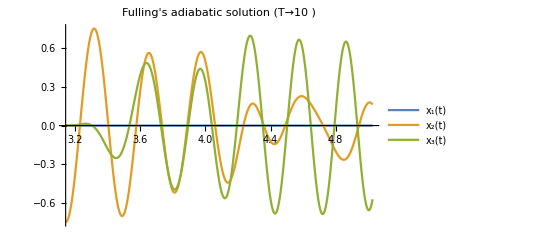

```mathematica
Plot[Evaluate@Re[vxPapFulling[T][t]/.T->10],relevantdomain,
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"Fulling's adiabatic solution (T"->10")"]
```

### Check of coefficients’ formulas with Fulling’s expressions

#### Rec: Fulling’s notation for initial constants

Note that Fulling uses a less systematic naming for the constants.
The translation is:

k=1	n=0	l=+1	ζ_1^+->ζ_(0,1,+1),
				l=+2	ζ_2^+->ζ_(0,1,+2),
		n=1	l=+1	η_1^+->ζ_(1,1,+1),
				l=+2	η_2^+->ζ_(1,1,+2),
k=2	n=0	l=+1	ζ_0^+->ζ_(0,2,+1),
		n=1	l=+1	η_0^+->ζ_(1,2,+1).

Furthermore, he omits the + sign in the individual-k results
(although not in the full expansion).

#### Formula for coefficient (a_0)^∥

```mathematica
vaP[0,1][a,b,T][t]/.j->ⅈ
```

{ζ_(0,1,1),(Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,2),(Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,2)}

In Fulling’s is eqn. (38):

```mathematica
Subscript[ζ, 0,1,1] e[1,1][a,b][t]+Subscript[ζ, 0,1,2] e[1,2][a,b][t]==vaP[0,1][a,b,T][t]/.j->ⅈ/.{a->1,b->1}//Simplify
```

True

#### Formula for coefficient (a_1)^⊥

```mathematica
vaN[1,1][a,b,T][t]/.j->ⅈ
```

{0,(2 b t Sin[b t] ζ_(0,1,2))/((-1+t) √(a t)),-(2 b t Cos[b t] ζ_(0,1,2))/((-1+t) √(a t))}

In Fulling’s is eqn. (40):

```mathematica
2 t^(1/2)(1-t)^-1 Subscript[ζ, 0,1,2] e[2,1][a,b][t]==vaN[1,1][a,b,T][t]/.j->ⅈ/.{a->1,b->1}//Simplify
```

True

#### Formula for coefficient (a_1)^∥

```mathematica
vaP[1,1][a,b,T][t]/.j->ⅈ
```

{-(5 (1/π^(3/2)-1/t^(3/2)) ζ_(0,1,1))/(48 √a)+ζ_(1,1,1),1/48 Cos[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,2))/(√a)+48 ζ_(1,1,2)),1/48 Sin[b t] (((-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) ζ_(0,1,2))/(√a)+48 ζ_(1,1,2))}

In Fulling’s are eqns. (42-44):

(43):

```mathematica
fullingF[t](*=1/2∫_π^t t1^(-1/2)(1-t1)^-1(1+3t1)ⅆt1*)
```

1/2 (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t])

(44):

```mathematica
Subscript[ζ, 1,1,1] e[1,1][a,b][t]+Subscript[ζ, 1,1,2] e[1,2][a,b][t]
```

{ζ_(1,1,1),Cos[b t] ζ_(1,1,2),Sin[b t] ζ_(1,1,2)}

(42):

```mathematica
(Subscript[ζ, 1,1,1] e[1,1][a,b][t]+Subscript[ζ, 1,1,2] e[1,2][a,b][t])+fullingF[t] Subscript[ζ, 0,1,2] e[1,2][a,b][t]+5/48(t^(-3/2)-π^(-3/2))va[0,1][a,b,T][t]
```

{5/48 (-1/π^(3/2)+1/t^(3/2)) ζ_(0,1,-ⅈ j)+ζ_(1,1,1),1/2 (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t]) Cos[b t] ζ_(0,1,2)+5/48 (-1/π^(3/2)+1/t^(3/2)) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)+Cos[b t] ζ_(1,1,2),1/2 (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t]) Sin[b t] ζ_(0,1,2)+5/48 (-1/π^(3/2)+1/t^(3/2)) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]) ζ_(0,1,-2 ⅈ j)+Sin[b t] ζ_(1,1,2)}

Altogether:

```mathematica
(Subscript[ζ, 1,1,1] e[1,1][a,b][t]+Subscript[ζ, 1,1,2] e[1,2][a,b][t])+fullingF[t] Subscript[ζ, 0,1,2] e[1,2][a,b][t]+5/48(t^(-3/2)-π^(-3/2))va[0,1][a,b,T][t]==vaP[1,1][a,b,T][t]/.j->ⅈ/.{a->1,b->1}//Simplify
```

True

### Fulling’s constants

```mathematica
constsFullingPaper={
Subscript[ζ, 0,1,1]->0,Subscript[ζ, 0,1,-1]->0,Subscript[ζ, 0,1,2]->1,Subscript[ζ, 0,1,-2]->0,Subscript[ζ, 0,2,1]->0,Subscript[ζ, 0,2,-1]->0,
Subscript[ζ, 1,1,1]->0,Subscript[ζ, 1,1,-1]->0,Subscript[ζ, 1,1,2]->1/8 π^(-3/2),Subscript[ζ, 1,1,-2]->1/8 π^(-3/2),Subscript[ζ, 1,2,1]->(1/2 π^(-1/4)(π+1)+π^(1/4))(π-1)^-1,Subscript[ζ, 1,2,-1]->(1/2 π^(-1/4)(π+1)-π^(1/4))(π-1)^-1,
Subscript[ζ, 2,1,1]->0,Subscript[ζ, 2,1,-1]->0,Subscript[ζ, 2,1,2]->0,Subscript[ζ, 2,1,-2]->0,Subscript[ζ, 2,2,1]->0,Subscript[ζ, 2,2,-1]->0};
```

And they make both solutions coincide!

```mathematica
TrueQ[vxPapFulling[T][t]==VecAdbGralExp[1][a,b,T][t]/.constsFullingPaper/.{a->1,b->1}//Simplify]
```

True

### Updated, exact Fulling’s initial conditions

```mathematica
(*icFullingSol=*)VecAdbGralExp[2][a,b,T][t]/.constsFullingPaper/.t->ti//Simplify
```

{0,Cos[b π]/(a^(1/4) π^(1/4))+(2 ⅈ (√a-b) π^(1/4) Sin[b π])/(a^(3/4) (-1+π) T),-(2 ⅈ (√a-b) π^(1/4) Cos[b π])/(a^(3/4) (-1+π) T)+Sin[b π]/(a^(1/4) π^(1/4))}

```mathematica
(*icFullingDeriv=*)VecAdbGralExp[2][a,b,T]'[t]/.constsFullingPaper/.t->ti//Simplify
```

{0,1/(128 a^(5/4) (-1+π)^2 π^(17/4) T^2)(Cos[b π] (30-60 π+2 (15-16 b^2) π^2-96 b^2 π^4+32 a (-1+π) π^3 T (8 ⅈ b π^(3/2)+T-π T)+32 a^(3/2) (-1+π)^2 π^3 T^2 (1+4 ⅈ π^(3/2) T)-ⅈ √a (-1+π)^2 (-5+16 b^2 π^2) (-ⅈ+4 π^(3/2) T)-40 b^2 π^(3/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])+80 b^2 π^(5/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])+8 b^2 (-5+16 b^2) π^(7/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])-256 b^4 π^(9/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])+128 b^4 π^(11/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))-64 √a π^(7/2) (-b^2 √π (-1+π^2)+2 a √π (-1+π^2) T^2-b T (ⅈ+3 ⅈ π-2 √a √π T+2 √a π^(5/2) T)) Sin[b π]),1/(128 a^(5/4) (-1+π)^2 π^(17/4) T^2)(64 √a π^(7/2) (-b^2 √π (-1+π^2)+2 a √π (-1+π^2) T^2-b T (ⅈ+3 ⅈ π-2 √a √π T+2 √a π^(5/2) T)) Cos[b π]+(30-60 π+2 (15-16 b^2) π^2-96 b^2 π^4+32 a (-1+π) π^3 T (8 ⅈ b π^(3/2)+T-π T)+32 a^(3/2) (-1+π)^2 π^3 T^2 (1+4 ⅈ π^(3/2) T)-ⅈ √a (-1+π)^2 (-5+16 b^2 π^2) (-ⅈ+4 π^(3/2) T)-40 b^2 π^(3/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])+80 b^2 π^(5/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])+8 b^2 (-5+16 b^2) π^(7/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])-256 b^4 π^(9/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])+128 b^4 π^(11/2) (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)])) Sin[b π])}

## Analytical adiabatic solution (for Fulling’s i.c.’s)

## Constants for Fulling’s initial conditions

### Rec: Fulling’s initial conditions

For the vector, x(t_i):

```mathematica
icFullingSol//MatrixForm
```

(0
Cos[b π]/π^(1/4)
Sin[b π]/π^(1/4))

For its derivative, x'(t_i):

```mathematica
icFullingDeriv//MatrixForm
```

(0
ⅈ π^(1/4) T Cos[b π]
ⅈ π^(1/4) T Sin[b π])

### Automatic solving at 0th order

```mathematica
constsFullingAuto=Solve[{
VecAdbGralExp[0][a,b,T][t]==icFullingSol,
VecAdbGralExp[0][a,b,T]'[t]==icFullingDeriv
}/.t->ti/.{a->1,b->1},
constsListUpto[0]]//Simplify//Normal//Flatten
```

{ζ_(0,1,1)→0,ζ_(0,1,-1)→0,ζ_(0,1,2)→1-ⅈ/(8 π^(3/2) T),ζ_(0,1,-2)→ⅈ/(8 π^(3/2) T),ζ_(0,2,1)→ⅈ/(2 π^(1/4) T),ζ_(0,2,-1)→-ⅈ/(2 π^(1/4) T)}

### Manual solving

Note: I didn’t fully match them but it doesn’t impact negatively.

#### I.c.’s for the solution

We have to find the corresponding ζ_(n,k,±l) to arrive to

```mathematica
icFullingSol//MatrixForm
```

(0
Cos[b π]/π^(1/4)
Sin[b π]/π^(1/4))

from

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti,T]//MatrixForm
```

((ζ_(0,1,-1))/(a^(1/4) π^(1/4))+(ζ_(0,1,1))/(a^(1/4) π^(1/4))+((ⅈ ζ_(1,1,-1))/(a^(1/4) π^(1/4))-(ⅈ ζ_(1,1,1))/(a^(1/4) π^(1/4)))/T
(Cos[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))-(Sin[b π] ζ_(0,2,-1))/a^(1/4)-(Sin[b π] ζ_(0,2,1))/a^(1/4)+((ⅈ ((2 b √π Sin[b π] ζ_(0,1,-2))/(√a (-1+π))+Cos[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ (-(2 b Cos[b π] ζ_(0,2,-1))/(√a (-1+π))-Sin[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(Sin[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+(Cos[b π] ζ_(0,2,-1))/a^(1/4)+(Cos[b π] ζ_(0,2,1))/a^(1/4)+((ⅈ (-(2 b √π Cos[b π] ζ_(0,1,-2))/(√a (-1+π))+Sin[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ (-(2 b Sin[b π] ζ_(0,2,-1))/(√a (-1+π))+Cos[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

#### First entry matching

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti/.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1]},T]//MatrixForm
```

(((ⅈ ζ_(1,1,-1))/(a^(1/4) π^(1/4))-(ⅈ ζ_(1,1,1))/(a^(1/4) π^(1/4)))/T
(Cos[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))-(Sin[b π] ζ_(0,2,-1))/a^(1/4)-(Sin[b π] ζ_(0,2,1))/a^(1/4)+((ⅈ ((2 b √π Sin[b π] ζ_(0,1,-2))/(√a (-1+π))+Cos[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ (-(2 b Cos[b π] ζ_(0,2,-1))/(√a (-1+π))-Sin[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(Sin[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+(Cos[b π] ζ_(0,2,-1))/a^(1/4)+(Cos[b π] ζ_(0,2,1))/a^(1/4)+((ⅈ (-(2 b √π Cos[b π] ζ_(0,1,-2))/(√a (-1+π))+Sin[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ (-(2 b Sin[b π] ζ_(0,2,-1))/(√a (-1+π))+Cos[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti/.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1]},T]//MatrixForm
```

(0
(Cos[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))-(Sin[b π] ζ_(0,2,-1))/a^(1/4)-(Sin[b π] ζ_(0,2,1))/a^(1/4)+((ⅈ ((2 b √π Sin[b π] ζ_(0,1,-2))/(√a (-1+π))+Cos[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ (-(2 b Cos[b π] ζ_(0,2,-1))/(√a (-1+π))-Sin[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(Sin[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+(Cos[b π] ζ_(0,2,-1))/a^(1/4)+(Cos[b π] ζ_(0,2,1))/a^(1/4)+((ⅈ (-(2 b √π Cos[b π] ζ_(0,1,-2))/(√a (-1+π))+Sin[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ (-(2 b Sin[b π] ζ_(0,2,-1))/(√a (-1+π))+Cos[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

#### Almost third entry matching

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti/.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1]},T]//MatrixForm
```

(0
(Cos[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+((ⅈ ((2 b √π Sin[b π] ζ_(0,1,-2))/(√a (-1+π))+Cos[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ ((2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(Sin[b π] ζ_(0,1,-2))/(a^(1/4) π^(1/4))+(Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+((ⅈ (-(2 b √π Cos[b π] ζ_(0,1,-2))/(√a (-1+π))+Sin[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ ((2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti/.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2]},T]//MatrixForm
```

(0
(2 Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+((ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ ((2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(2 Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+((ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))+(ⅈ ((2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,-1)))/a^(1/4)-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti/.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1]},T]//MatrixForm
```

(0
(2 Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+((ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ ((2 b √π Sin[b π] ζ_(0,1,2))/(√a (-1+π))+Cos[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4)+(ⅈ ((2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(2 Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+((ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,-2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b √π Cos[b π] ζ_(0,1,2))/(√a (-1+π))+Sin[b π] ζ_(1,1,2)))/(a^(1/4) π^(1/4))-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4)+(ⅈ ((2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti/.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2]},T]//MatrixForm
```

(0
(2 Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+(-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4)+(ⅈ ((2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(2 Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+(-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4)+(ⅈ ((2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

#### First ‘less natural’ choice

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti/.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2]},T]//MatrixForm
```

(0
(2 Cos[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+(-(ⅈ (-(2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4)+(ⅈ ((2 b Cos[b π] ζ_(0,2,1))/(√a (-1+π))-Sin[b π] ζ_(1,2,1)))/a^(1/4))/T
(2 Sin[b π] ζ_(0,1,2))/(a^(1/4) π^(1/4))+(-(ⅈ (-(2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4)+(ⅈ ((2 b Sin[b π] ζ_(0,2,1))/(√a (-1+π))+Cos[b π] ζ_(1,2,1)))/a^(1/4))/T)

```mathematica
Collect[VecAdbGralExp[1][a,b,T][t]/.t->ti//.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2], Subscript[ζ, 0,1,2]->1/2,Subscript[ζ, 0,2,1]->0},T]//MatrixForm
```

(0
Cos[b π]/(a^(1/4) π^(1/4))
Sin[b π]/(a^(1/4) π^(1/4)))

Note: Like before, we let this as is, even though they’re not exactly Fulling’s i.c.’s. (They would if Sin[b Pi] = 0.)

#### I.c.’s for the derivative

Now we need to arrive to

```mathematica
icFullingDeriv//MatrixForm
```

(0
ⅈ π^(1/4) T Cos[b π]
ⅈ π^(1/4) T Sin[b π])

from

```mathematica
Collect[VecAdbGralExp[1][a,b,T]'[t]/.t->ti//.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2], Subscript[ζ, 0,1,2]->1/2,Subscript[ζ, 0,2,1]->0},T]//MatrixForm
```

((5 ⅈ ζ_(0,1,1))/(16 a^(3/4) π^(11/4) T)+2 ⅈ a^(1/4) π^(1/4) T ζ_(0,1,1)+2 a^(1/4) π^(1/4) ζ_(1,1,1)
-Cos[b π]/(4 a^(1/4) π^(5/4))-(b Sin[b π])/(a^(1/4) π^(1/4))+2 a^(1/4) π^(1/4) ((b √π Sin[b π])/(√a (-1+π))+Cos[b π] ζ_(1,1,2))-2 a^(1/4) Sin[b π] ζ_(1,2,1)
(b Cos[b π])/(a^(1/4) π^(1/4))-Sin[b π]/(4 a^(1/4) π^(5/4))+2 a^(1/4) π^(1/4) (-(b √π Cos[b π])/(√a (-1+π))+Sin[b π] ζ_(1,1,2))+2 a^(1/4) Cos[b π] ζ_(1,2,1))

#### First entry matching

```mathematica
Collect[VecAdbGralExp[1][a,b,T]'[t]/.t->ti//.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2], Subscript[ζ, 0,1,2]->1/2,Subscript[ζ, 0,2,1]->0,Subscript[ζ, 0,1,1]->0,Subscript[ζ, 0,1,1]->0,Subscript[ζ, 1,1,1]->0},T]//MatrixForm
```

(0
-Cos[b π]/(4 a^(1/4) π^(5/4))-(b Sin[b π])/(a^(1/4) π^(1/4))+2 a^(1/4) π^(1/4) ((b √π Sin[b π])/(√a (-1+π))+Cos[b π] ζ_(1,1,2))-2 a^(1/4) Sin[b π] ζ_(1,2,1)
(b Cos[b π])/(a^(1/4) π^(1/4))-Sin[b π]/(4 a^(1/4) π^(5/4))+2 a^(1/4) π^(1/4) (-(b √π Cos[b π])/(√a (-1+π))+Sin[b π] ζ_(1,1,2))+2 a^(1/4) Cos[b π] ζ_(1,2,1))

```mathematica
(b Cos[b π])/(a^(1/4) π^(1/4))-Sin[b π]/(4 a^(1/4) π^(5/4))+2 a^(1/4) π^(1/4) (-(b √π Cos[b π])/(√a (-1+π))+Sin[b π] Subscript[ζ, 1,1,2])+2 a^(1/4) Cos[b π] Subscript[ζ, 1,2,1]/.b->1/.a->1
```

-1/π^(1/4)+(2 π^(3/4))/(-1+π)-2 ζ_(1,2,1)

#### Third entry matching

Rec:

```mathematica
icFullingDeriv//MatrixForm
```

(0
ⅈ π^(1/4) T Cos[b π]
ⅈ π^(1/4) T Sin[b π])

```mathematica
Solve[(b Cos[b π])/(a^(1/4) π^(1/4))-Sin[b π]/(4 a^(1/4) π^(5/4))+2 a^(1/4) π^(1/4) (-(b √π Cos[b π])/(√a (-1+π))+Sin[b π] Subscript[ζ, 1,1,2])+2 a^(1/4) Cos[b π] Subscript[ζ, 1,2,1]==ⅈ π^(1/4) T Sin[b π],Subscript[ζ, 1,2,1]]//Flatten
```

{ζ_(1,2,1)→((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) ζ_(1,1,2) Tan[b π]-8 √a π^(5/2) ζ_(1,1,2) Tan[b π])/(√a π^(5/4)))/(8 (-1+π))}

```mathematica
Collect[VecAdbGralExp[1][a,b,T]'[t]/.t->ti//.{Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2], Subscript[ζ, 0,1,2]->1/2,Subscript[ζ, 0,2,1]->0,Subscript[ζ, 0,1,1]->0,Subscript[ζ, 0,1,1]->0,Subscript[ζ, 1,1,1]->0,Subscript[ζ, 1,2,1]->1/(8 (-1+π))((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+1/(√a π^(5/4))(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) Subscript[ζ, 1,1,2] Tan[b π]-8 √a π^(5/2) Subscript[ζ, 1,1,2] Tan[b π]))},T]//Simplify//MatrixForm
```

(0
(Sec[b π] (-1-2 ⅈ a^(1/4) π^(3/2) T+2 ⅈ a^(1/4) π^(3/2) T Cos[2 b π]+8 √a π^(3/2) ζ_(1,1,2)))/(4 a^(1/4) π^(5/4))
ⅈ π^(1/4) T Sin[b π])

#### Second entry matching

```mathematica
Solve[(Sec[b π] (-1-2 ⅈ a^(1/4) π^(3/2) T+2 ⅈ a^(1/4) π^(3/2) T Cos[2 b π]+8 √a π^(3/2) Subscript[ζ, 1,1,2]))/(4 a^(1/4) π^(5/4))==ⅈ π^(1/4) T Cos[b π],Subscript[ζ, 1,1,2]]//Simplify//Flatten
```

{ζ_(1,1,2)→(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a)}

#### Final list: Fulling’s constants manually solved (up to 1st order)

```mathematica
constsFulling0thOrd={Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2], Subscript[ζ, 0,1,2]->1/2,Subscript[ζ, 0,2,1]->0,Subscript[ζ, 0,1,1]->0,Subscript[ζ, 0,1,1]->0}
```

{ζ_(0,1,-1)→-ζ_(0,1,1),ζ_(0,2,-1)→-ζ_(0,2,1),ζ_(0,1,-2)→ζ_(0,1,2),ζ_(0,1,2)→1/2,ζ_(0,2,1)→0,ζ_(0,1,1)→0,ζ_(0,1,1)→0}

```mathematica
constsFulling1stOrd[a_,b_,T_]={Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2],Subscript[ζ, 1,1,1]->0,Subscript[ζ, 1,2,1]->1/(8 (-1+π))((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+1/(√a π^(5/4))(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) Subscript[ζ, 1,1,2] Tan[b π]-8 √a π^(5/2) Subscript[ζ, 1,1,2] Tan[b π])),Subscript[ζ, 1,1,2]->(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a)}
```

{ζ_(1,1,-1)→ζ_(1,1,1),ζ_(1,2,-1)→ζ_(1,2,1),ζ_(1,1,-2)→ζ_(1,1,2),ζ_(1,1,1)→0,ζ_(1,2,1)→((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) ζ_(1,1,2) Tan[b π]-8 √a π^(5/2) ζ_(1,1,2) Tan[b π])/(√a π^(5/4)))/(8 (-1+π)),ζ_(1,1,2)→(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a)}

```mathematica
icFullingSol
VecAdbGralExp[1][a,b,T][t]/.t->ti//.constsFulling0thOrd//.constsFulling1stOrd[a,b,T]//Simplify
icFullingDeriv
VecAdbGralExp[1][a,b,T]'[t]/.t->ti//.constsFulling0thOrd//.constsFulling1stOrd[a,b,T]//Simplify
```

{0,Cos[b π]/π^(1/4),Sin[b π]/π^(1/4)}

{0,Cos[b π]/(a^(1/4) π^(1/4)),Sin[b π]/(a^(1/4) π^(1/4))}

{0,ⅈ π^(1/4) T Cos[b π],ⅈ π^(1/4) T Sin[b π]}

{0,ⅈ π^(1/4) T Cos[b π],ⅈ π^(1/4) T Sin[b π]}

```mathematica
icFullingSol==VecAdbGralExp[1][a,b,T][t]/.t->ti//.constsFulling0thOrd//.constsFulling1stOrd[a,b,T]//Simplify
icFullingDeriv==VecAdbGralExp[1][a,b,T]'[t]/.t->ti//.constsFulling0thOrd//.constsFulling1stOrd[a,b,T]//Simplify
```

{0,((-1+a^(1/4)) Cos[b π])/(a^(1/4) π^(1/4)),((-1+a^(1/4)) Sin[b π])/(a^(1/4) π^(1/4))}=={0,0,0}

True

### Second order constants

#### Rec: 1st order Fulling’s constants

Note: Until now we have only considered expressions up to first adiabatic order, so we have only settled the  ζ_(0,k,±l) and  ζ_(1,k,±l) constants:

```mathematica
constsFulling0thOrd
```

{ζ_(0,1,-1)→-ζ_(0,1,1),ζ_(0,2,-1)→-ζ_(0,2,1),ζ_(0,1,-2)→ζ_(0,1,2),ζ_(0,1,2)→1/2,ζ_(0,2,1)→0,ζ_(0,1,1)→0,ζ_(0,1,1)→0}

```mathematica
constsFulling1stOrd[a,b,T]
```

{ζ_(1,1,-1)→ζ_(1,1,1),ζ_(1,2,-1)→ζ_(1,2,1),ζ_(1,1,-2)→ζ_(1,1,2),ζ_(1,1,1)→0,ζ_(1,2,1)→((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) ζ_(1,1,2) Tan[b π]-8 √a π^(5/2) ζ_(1,1,2) Tan[b π])/(√a π^(5/4)))/(8 (-1+π)),ζ_(1,1,2)→(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a)}

Hence, we still need to specify the constants  ζ_(2,k,±l) for the second order.

#### Simplest option: all zero at 2nd order

Let’s choose the simplest option (all zero):

ζ_(2,1,-1)->ζ_(2,1,1),ζ_(2,1,-2)->ζ_(2,1,2),ζ_(2,2,-1)->ζ_(2,2,1),ζ_(2,2,-2)->ζ_(2,2,2),ζ_(2,1,1)->0,ζ_(2,1,2)->0,ζ_(2,2,1)->0,ζ_(2,2,2)->0

```mathematica
constsFullingHO0s={Subscript[ζ, 2,1,-1]->Subscript[ζ, 2,1,1],Subscript[ζ, 2,1,-2]->Subscript[ζ, 2,1,2],Subscript[ζ, 2,2,-1]->Subscript[ζ, 2,2,1],Subscript[ζ, 2,2,-2]->Subscript[ζ, 2,2,2],Subscript[ζ, 2,1,1]->0,Subscript[ζ, 2,1,2]->0,Subscript[ζ, 2,2,1]->0,Subscript[ζ, 2,2,2]->0}
```

{ζ_(2,1,-1)→ζ_(2,1,1),ζ_(2,1,-2)→ζ_(2,1,2),ζ_(2,2,-1)→ζ_(2,2,1),ζ_(2,2,-2)→ζ_(2,2,2),ζ_(2,1,1)→0,ζ_(2,1,2)→0,ζ_(2,2,1)→0,ζ_(2,2,2)→0}

```mathematica
constsFulling[a_,b_,T_]={constsFulling0thOrd,constsFulling1stOrd[a,b,T],constsFullingHO0s}//Flatten
```

{ζ_(0,1,-1)→-ζ_(0,1,1),ζ_(0,2,-1)→-ζ_(0,2,1),ζ_(0,1,-2)→ζ_(0,1,2),ζ_(0,1,2)→1/2,ζ_(0,2,1)→0,ζ_(0,1,1)→0,ζ_(0,1,1)→0,ζ_(1,1,-1)→ζ_(1,1,1),ζ_(1,2,-1)→ζ_(1,2,1),ζ_(1,1,-2)→ζ_(1,1,2),ζ_(1,1,1)→0,ζ_(1,2,1)→((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) ζ_(1,1,2) Tan[b π]-8 √a π^(5/2) ζ_(1,1,2) Tan[b π])/(√a π^(5/4)))/(8 (-1+π)),ζ_(1,1,2)→(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a),ζ_(2,1,-1)→ζ_(2,1,1),ζ_(2,1,-2)→ζ_(2,1,2),ζ_(2,2,-1)→ζ_(2,2,1),ζ_(2,2,-2)→ζ_(2,2,2),ζ_(2,1,1)→0,ζ_(2,1,2)→0,ζ_(2,2,1)→0,ζ_(2,2,2)→0}

#### Manipulable constants at 2nd order

```mathematica
1/(8 (-1+π))((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+1/(√a π^(5/4))(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) Subscript[ζ, 1,1,2] Tan[b π]-8 √a π^(5/2) Subscript[ζ, 1,1,2] Tan[b π]))/.{a->1,b->1}//N
(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a)/.{a->1,b->1,T->1}//N
```

0.726295

0.0224484+0.5 ⅈ

{ζ_(2,1,-1)→ζ_(2,1,1),ζ_(2,1,1)→0,
ζ_(2,2,-1)→ζ_(2,2,1),ζ_(2,2,1)→c1,
ζ_(2,1,-2)→ζ_(2,1,2),ζ_(2,1,2)→c2+c3 ⅈ}

```mathematica
constsFullingManip[a_,b_,T_,c1r_,c1i_,c2r_,c2i_]={
Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],Subscript[ζ, 0,1,1]->0,
Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],Subscript[ζ, 0,2,1]->0,
Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 0,1,2]->1/2,
Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],Subscript[ζ, 1,1,1]->0,
Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],Subscript[ζ, 1,2,1]->1/(8 (-1+π))((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+1/(√a π^(5/4))(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) Subscript[ζ, 1,1,2] Tan[b π]-8 √a π^(5/2) Subscript[ζ, 1,1,2] Tan[b π])),
Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2],Subscript[ζ, 1,1,2]->(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a),
Subscript[ζ, 2,1,-1]->Subscript[ζ, 2,1,1],Subscript[ζ, 2,1,1]->0,
Subscript[ζ, 2,2,-1]->Subscript[ζ, 2,2,1],Subscript[ζ, 2,2,1]->c1r+c1i ⅈ,
Subscript[ζ, 2,1,-2]->Subscript[ζ, 2,1,2],Subscript[ζ, 2,1,2]->c2r+c2i ⅈ};
```

```mathematica
vxAdbFullingManip[2][a_,b_,T_,c1r_,c1i_,c2r_,c2i_][t_]=VecAdbGralExp[2][a,b,T][t]//.constsFullingManip[a,b,T,c1r,c1i,c2r,c2i];
```

#### Structure of Fulling’s constants

```mathematica
constsFulling0thOrd
```

{ζ_(0,1,-1)→-ζ_(0,1,1),ζ_(0,2,-1)→-ζ_(0,2,1),ζ_(0,1,-2)→ζ_(0,1,2),ζ_(0,1,2)→1/2,ζ_(0,2,1)→0,ζ_(0,1,1)→0,ζ_(0,1,1)→0}

{ζ_(0,1,-1)→-ζ_(0,1,1),ζ_(0,1,1)→0,
ζ_(0,2,-1)→-ζ_(0,2,1),ζ_(0,2,1)→0,
ζ_(0,1,-2)→ζ_(0,1,2),ζ_(0,1,2)→1/2}

The movement starts with only one mode excited, the one corresponding to eigenvector e_1^(2)(t) (the initial condition). Then...

```mathematica
constsFulling1stOrd[a,b,T]
```

{ζ_(1,1,-1)→ζ_(1,1,1),ζ_(1,2,-1)→ζ_(1,2,1),ζ_(1,1,-2)→ζ_(1,1,2),ζ_(1,1,1)→0,ζ_(1,2,1)→((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) ζ_(1,1,2) Tan[b π]-8 √a π^(5/2) ζ_(1,1,2) Tan[b π])/(√a π^(5/4)))/(8 (-1+π)),ζ_(1,1,2)→(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a)}

{ζ_(1,1,-1)→ζ_(1,1,1),ζ_(1,1,1)→0,
ζ_(1,2,-1)→ζ_(1,2,1),ζ_(1,2,1)→1/(8 (-1+π))((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+1/(√a π^(5/4))(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) ζ_(1,1,2) Tan[b π]-8 √a π^(5/2) ζ_(1,1,2) Tan[b π])),
ζ_(1,1,-2)→ζ_(1,1,2),ζ_(1,1,2)→(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a)}

#### Attempt to solve i.c.’s at 2nd order

```mathematica
icFullingSol
```

{0,Cos[b π]/π^(1/4),Sin[b π]/π^(1/4)}

```mathematica
icFullingDeriv
```

{0,ⅈ π^(1/4) T Cos[b π],ⅈ π^(1/4) T Sin[b π]}

```mathematica
{Subscript[ζ, 0,1,1],Subscript[ζ, 0,1,-1],Subscript[ζ, 0,2,1],Subscript[ζ, 0,2,-1],Subscript[ζ, 1,1,1],Subscript[ζ, 1,1,-1],Subscript[ζ, 1,2,1],Subscript[ζ, 1,2,-1]}
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,2,1),ζ_(1,2,-1)}

```mathematica
constsList
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,1,2),ζ_(0,1,-2),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,1,2),ζ_(1,1,-2),ζ_(1,2,1),ζ_(1,2,-1),ζ_(2,1,1),ζ_(2,1,-1),ζ_(2,1,2),ζ_(2,1,-2),ζ_(2,2,1),ζ_(2,2,-1)}

```mathematica
switch1off={
Subscript[ζ, 0,1,1]->0,Subscript[ζ, 0,1,-1]->0,
Subscript[ζ, 1,1,1]->0,Subscript[ζ, 1,1,-1]->0,
Subscript[ζ, 2,1,1]->0,Subscript[ζ, 2,1,-1]->0};
```

```mathematica
constsFullingAutoHO[a_,b_,T_]=NSolve[{VecAdbGralExp[2][a,b,T][t]==icFullingSol,VecAdbGralExp[1][a,b,T]'[t]==icFullingDeriv}/.t->ti/.switch1off,constsList]//Flatten;
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
constsFull0th={
Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],Subscript[ζ, 0,1,2]->1/2};
```

```mathematica
constsFullingStructure={
Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],
Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2],
Subscript[ζ, 2,2,-1]->Subscript[ζ, 2,2,1],
Subscript[ζ, 2,1,-2]->Subscript[ζ, 2,1,2]};
```

```mathematica
constsFullingAutoHO[1,1,1]//.constsFull0th//.constsFullingStructure//Chop
```

{ζ_(1,2,1)→(1.39196-0.0298863 ⅈ)-(0.218035+0.716942 ⅈ) ζ_(0,2,-1)+(0.218035-1.21694 ⅈ) ζ_(0,2,1)+(0.+1.33134 ⅈ) ζ_(1,1,2),ζ_(1,2,1)→(0.0606273+0.0298863 ⅈ)+(0.218035+1.21694 ⅈ) ζ_(0,2,-1)-(0.218035-0.716942 ⅈ) ζ_(0,2,1)-(0.+1.33134 ⅈ) ζ_(1,1,2),ζ_(2,1,2)→(0.-1.24331 ⅈ) ζ_(0,2,-1)+(0.+1.24331 ⅈ) ζ_(0,2,1)-1. ζ_(2,1,2),ζ_(2,2,1)→(-0.0597727-1.33134 ⅈ)-(0.933884-0.43607 ⅈ) ζ_(0,2,-1)-(0.933884+0.43607 ⅈ) ζ_(0,2,1)+2.66267 ζ_(1,1,2)-1. ζ_(2,2,1)}

#### Inspecting the structure

switch1off={
ζ_(0,1,1)->0,ζ_(0,1,-1)->0,
ζ_(1,1,1)->0,ζ_(1,1,-1)->0,
ζ_(2,1,1)->0,ζ_(2,1,-1)->0};

constsFull0th={
ζ_(0,1,-2)→ζ_(0,1,2),ζ_(0,1,2)→1/2};

constsFullingStructure={
ζ_(1,2,-1)→ζ_(1,2,1),
ζ_(1,1,-2)→ζ_(1,1,2),
ζ_(2,2,-1)→ζ_(2,2,1),
ζ_(2,1,-2)→ζ_(2,1,2)};

```mathematica
{Subscript[ζ, 1,2,1]->(1.3919626735423127-0.02988633582104673 ⅈ)-(0.21803502460729834+0.7169422069242599 ⅈ) Subscript[ζ, 0,2,-1]+(0.21803502460729834-1.21694220692426 ⅈ) Subscript[ζ, 0,2,1]+(0.+1.33133536380039 ⅈ) Subscript[ζ, 1,1,2],
Subscript[ζ, 1,2,1]->(0.06062730974192283+0.029886335821046703 ⅈ)+(0.21803502460729834+1.21694220692426 ⅈ) Subscript[ζ, 0,2,-1]-(0.21803502460729834-0.7169422069242599 ⅈ) Subscript[ζ, 0,2,1]-(0.+1.33133536380039 ⅈ) Subscript[ζ, 1,1,2],
Subscript[ζ, 2,1,2]->(0.-1.2433133458585326 ⅈ) Subscript[ζ, 0,2,-1]+(0.+1.2433133458585326 ⅈ) Subscript[ζ, 0,2,1]-1. Subscript[ζ, 2,1,2],
Subscript[ζ, 2,2,1]->(-0.059772671642093406-1.3313353638003897 ⅈ)-(0.9338844138485198-0.4360700492145967 ⅈ) Subscript[ζ, 0,2,-1]-(0.9338844138485197+0.4360700492145967 ⅈ) Subscript[ζ, 0,2,1]+2.6626707276007795 Subscript[ζ, 1,1,2]-1. Subscript[ζ, 2,2,1]}
```

{ζ_(1,2,1)→(1.39196-0.0298863 ⅈ)-(0.218035+0.716942 ⅈ) ζ_(0,2,-1)+(0.218035-1.21694 ⅈ) ζ_(0,2,1)+(0.+1.33134 ⅈ) ζ_(1,1,2),ζ_(1,2,1)→(0.0606273+0.0298863 ⅈ)+(0.218035+1.21694 ⅈ) ζ_(0,2,-1)-(0.218035-0.716942 ⅈ) ζ_(0,2,1)-(0.+1.33134 ⅈ) ζ_(1,1,2),ζ_(2,1,2)→(0.-1.24331 ⅈ) ζ_(0,2,-1)+(0.+1.24331 ⅈ) ζ_(0,2,1)-1. ζ_(2,1,2),ζ_(2,2,1)→(-0.0597727-1.33134 ⅈ)-(0.933884-0.43607 ⅈ) ζ_(0,2,-1)-(0.933884+0.43607 ⅈ) ζ_(0,2,1)+2.66267 ζ_(1,1,2)-1. ζ_(2,2,1)}

### Terms of the T-series expansion at initial time

#### In the solution

```mathematica
Collect[Coefficient[VecAdbGralExp[2][1,1,T][t]/.t->ti,T,0],Subscript[ζ, _,_,_]]//MatrixForm
```

((ζ_(0,1,-1))/π^(1/4)+(ζ_(0,1,1))/π^(1/4)
-(ζ_(0,1,-2))/π^(1/4)-(ζ_(0,1,2))/π^(1/4)
-ζ_(0,2,-1)-ζ_(0,2,1))

```mathematica
Collect[Coefficient[VecAdbGralExp[2][1,1,T][t]/.t->ti,T,-1],Subscript[ζ, _,_,_]]//MatrixForm
```

((ⅈ ζ_(1,1,-1))/π^(1/4)-(ⅈ ζ_(1,1,1))/π^(1/4)
(2 ⅈ ζ_(0,2,-1))/(-1+π)-(2 ⅈ ζ_(0,2,1))/(-1+π)-(ⅈ ζ_(1,1,-2))/π^(1/4)+(ⅈ ζ_(1,1,2))/π^(1/4)
(2 ⅈ π^(1/4) ζ_(0,1,-2))/(-1+π)-(2 ⅈ π^(1/4) ζ_(0,1,2))/(-1+π)-ⅈ ζ_(1,2,-1)+ⅈ ζ_(1,2,1))

```mathematica
Collect[Coefficient[VecAdbGralExp[2][1,1,T][t]/.t->ti,T,-2],Subscript[ζ, _,_,_]]//MatrixForm
```

(-(ζ_(2,1,-1))/π^(1/4)-(ζ_(2,1,1))/π^(1/4)
(ζ_(2,1,-2))/π^(1/4)+(ζ_(2,1,2))/π^(1/4)
ζ_(2,2,-1)+ζ_(2,2,1))

#### In the derivative

```mathematica
Collect[Coefficient[VecAdbGralExp[2][1,1,T]'[t]/.t->ti,T,0],Subscript[ζ, _,_,_]]//MatrixForm
```

(-(ζ_(0,1,-1))/(4 π^(5/4))-(ζ_(0,1,1))/(4 π^(5/4))+π^(1/4) ζ_(1,1,-1)+π^(1/4) ζ_(1,1,1)
(ζ_(0,1,-2))/(4 π^(5/4))+(ζ_(0,1,2))/(4 π^(5/4))+(1+2/(-1+π)) ζ_(0,2,-1)+(1+2/(-1+π)) ζ_(0,2,1)-π^(1/4) ζ_(1,1,-2)-π^(1/4) ζ_(1,1,2)
(-1/π^(1/4)+(2 π^(3/4))/(-1+π)) ζ_(0,1,-2)+(-1/π^(1/4)+(2 π^(3/4))/(-1+π)) ζ_(0,1,2)-ζ_(1,2,-1)-ζ_(1,2,1))

```mathematica
Collect[Coefficient[VecAdbGralExp[2][1,1,T]'[t]/.t->ti,T,-1],Subscript[ζ, _,_,_]]//MatrixForm
```

(-(5 ⅈ ζ_(0,1,-1))/(32 π^(11/4))+(5 ⅈ ζ_(0,1,1))/(32 π^(11/4))-(ⅈ ζ_(1,1,-1))/(4 π^(5/4))+(ⅈ ζ_(1,1,1))/(4 π^(5/4))+ⅈ π^(1/4) ζ_(2,1,-1)-ⅈ π^(1/4) ζ_(2,1,1)
((5 ⅈ)/(32 π^(11/4))+(3 ⅈ)/(2 π^(3/4))-(2 ⅈ)/((1-π) π^(3/4))-(2 ⅈ π^(1/4))/(-1+π)) ζ_(0,1,-2)+(-(5 ⅈ)/(32 π^(11/4))-(3 ⅈ)/(2 π^(3/4))+(2 ⅈ)/((1-π) π^(3/4))+(2 ⅈ π^(1/4))/(-1+π)) ζ_(0,1,2)-(2 ⅈ ζ_(0,2,-1))/(-1+π)^2+(2 ⅈ ζ_(0,2,1))/(-1+π)^2+(ⅈ ζ_(1,1,-2))/(4 π^(5/4))-(ⅈ ζ_(1,1,2))/(4 π^(5/4))+ⅈ ζ_(1,2,-1)-ⅈ ζ_(1,2,1)-ⅈ π^(1/4) ζ_(2,1,-2)+ⅈ π^(1/4) ζ_(2,1,2)
(ⅈ/(2 (-1+π) π^(3/4))-(2 ⅈ π^(1/4))/(-1+π)^2) ζ_(0,1,-2)+(-ⅈ/(2 (-1+π) π^(3/4))+(2 ⅈ π^(1/4))/(-1+π)^2) ζ_(0,1,2)-1/2 ⅈ ζ_(0,2,-1)+1/2 ⅈ ζ_(0,2,1)-(ⅈ ζ_(1,1,-2))/π^(1/4)+(ⅈ ζ_(1,1,2))/π^(1/4)-ⅈ ζ_(2,2,-1)+ⅈ ζ_(2,2,1))

```mathematica
Collect[Coefficient[VecAdbGralExp[2][1,1,T]'[t]/.t->ti,T,-2]//FullSimplify//Expand,Subscript[ζ, _,_,_]]//MatrixForm
```

((15 ζ_(0,1,-1))/(64 π^(17/4))+(15 ζ_(0,1,1))/(64 π^(17/4))+(5 ζ_(1,1,-1))/(32 π^(11/4))+(5 ζ_(1,1,1))/(32 π^(11/4))+(ζ_(2,1,-1))/(4 π^(5/4))+(ζ_(2,1,1))/(4 π^(5/4))
(-15/(64 (-1+π)^2 π^(17/4))+15/(32 (-1+π)^2 π^(13/4))+1/(64 (-1+π)^2 π^(9/4))+3/(4 (-1+π)^2 π^(1/4))) ζ_(0,1,-2)+(-15/(64 (-1+π)^2 π^(17/4))+15/(32 (-1+π)^2 π^(13/4))+1/(64 (-1+π)^2 π^(9/4))+3/(4 (-1+π)^2 π^(1/4))) ζ_(0,1,2)+(-5/(32 (-1+π)^2 π^(11/4))+5/(16 (-1+π)^2 π^(7/4))+11/(32 (-1+π)^2 π^(3/4))-π^(1/4)/(-1+π)^2+π^(5/4)/(2 (-1+π)^2)) ζ_(1,1,-2)+(-5/(32 (-1+π)^2 π^(11/4))+5/(16 (-1+π)^2 π^(7/4))+11/(32 (-1+π)^2 π^(3/4))-π^(1/4)/(-1+π)^2+π^(5/4)/(2 (-1+π)^2)) ζ_(1,1,2)+(-1/(4 (-1+π)^2 π^(5/4))+1/(2 (-1+π)^2 π^(1/4))-π^(3/4)/(4 (-1+π)^2)) ζ_(2,1,-2)+(-1/(4 (-1+π)^2 π^(5/4))+1/(2 (-1+π)^2 π^(1/4))-π^(3/4)/(4 (-1+π)^2)) ζ_(2,1,2)+(-1/(-1+π)^2+(2 π)/(-1+π)^2-π^2/(-1+π)^2) ζ_(2,2,-1)+(-1/(-1+π)^2+(2 π)/(-1+π)^2-π^2/(-1+π)^2) ζ_(2,2,1)
-(ζ_(0,2,-1))/(-1+π)^2-(ζ_(0,2,1))/(-1+π)^2+1/2 ζ_(1,2,-1)+1/2 ζ_(1,2,1)+(ζ_(2,1,-2))/π^(1/4)+(ζ_(2,1,2))/π^(1/4))

### Result for the full expansion (not just initial conditions) ↪︎ Uses Fulling’s paper solution, so it should go after that, not here

We stay at 1st order.

#### First entry (1st order)

```mathematica
vxPapFulling[T][t]
```

{0,(ⅈ ⅇ^(-2/3 ⅈ (-π^(3/2)+t^(3/2)) T) Cos[t])/(8 π^(3/2) t^(1/4) T)-(ⅈ ⅇ^(-ⅈ (-π+t) T) (-π^(1/4)+(1+π)/(2 π^(1/4))) Sin[t])/((-1+π) T)+(ⅈ ⅇ^(ⅈ (-π+t) T) (π^(1/4)+(1+π)/(2 π^(1/4))) Sin[t])/((-1+π) T)+(ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T) (Cos[t]-(ⅈ (Cos[t]/(8 π^(3/2))+5/48 (-1/π^(3/2)+1/t^(3/2)) Cos[t]+1/2 (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t]) Cos[t]-(2 √t Sin[t])/(1-t)))/T))/t^(1/4),(ⅈ ⅇ^(-ⅈ (-π+t) T) (-π^(1/4)+(1+π)/(2 π^(1/4))) Cos[t])/((-1+π) T)-(ⅈ ⅇ^(ⅈ (-π+t) T) (π^(1/4)+(1+π)/(2 π^(1/4))) Cos[t])/((-1+π) T)+(ⅈ ⅇ^(-2/3 ⅈ (-π^(3/2)+t^(3/2)) T) Sin[t])/(8 π^(3/2) t^(1/4) T)+(ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T) (Sin[t]-(ⅈ ((2 √t Cos[t])/(1-t)+Sin[t]/(8 π^(3/2))+5/48 (-1/π^(3/2)+1/t^(3/2)) Sin[t]+1/2 (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t]) Sin[t]))/T))/t^(1/4)}

```mathematica
vxPapFulling[T][t][[1]]
VecAdbGralExp[1][a,b,T][t][[1]]//.constsFulling[a,b,T]
```

0

0

#### Second entry (1st order)

```mathematica
vxPapFulling[T][t][[2]]//Simplify
VecAdbGralExp[1][a,b,T][t][[2]]//.constsFulling[a,b,T]//Simplify
```

(ⅈ ⅇ^(2/3 ⅈ (π^(3/2)-t^(3/2)) T) Cos[t])/(8 π^(3/2) t^(1/4) T)-(ⅈ ⅇ^(ⅈ (π-t) T) (-1+√π) Sin[t])/(2 (1+√π) π^(1/4) T)+(ⅈ ⅇ^(ⅈ (-π+t) T) (1+√π) Sin[t])/(2 (-1+√π) π^(1/4) T)+(ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T) (Cos[t]-(ⅈ ((1/(48 π^(3/2))+3 √π+5/(48 t^(3/2))-3 √t-4 ArcCoth[√π]) Cos[t]+4 ArcCoth[√t] Cos[t]+(2 √t Sin[t])/(-1+t)))/T))/t^(1/4)

1/2 ((ⅈ b ⅇ^(-ⅈ √a (π-t) T) (1+π) Sin[b t])/(a^(3/4) (-1+π) π^(1/4) T)-(ⅈ b ⅇ^(ⅈ √a (π-t) T) (1+π) Sin[b t])/(a^(3/4) (-1+π) π^(1/4) T)+1/(a t)^(1/4)ⅇ^(-2/3 ⅈ (√a π^(3/2)-t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]-(2 ⅈ (((7/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t+48 ⅈ a^(1/4) T-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) Cos[b t])/(96 √a)+(b t Sin[b t])/((-1+t) √(a t))))/T)+1/(a t)^(1/4)ⅇ^(2/3 ⅈ (√a π^(3/2)-t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]+(2 ⅈ (((7/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t+48 ⅈ a^(1/4) T-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t]) Cos[b t])/(96 √a)+(b t Sin[b t])/((-1+t) √(a t))))/T))

#### Third entry (1st order)

```mathematica
vxPapFulling[T][t][[3]]
VecAdbGralExp[1][a,b,T][t][[3]]//.constsFulling[a,b,T]
```

(ⅈ ⅇ^(-ⅈ (-π+t) T) (-π^(1/4)+(1+π)/(2 π^(1/4))) Cos[t])/((-1+π) T)-(ⅈ ⅇ^(ⅈ (-π+t) T) (π^(1/4)+(1+π)/(2 π^(1/4))) Cos[t])/((-1+π) T)+(ⅈ ⅇ^(-2/3 ⅈ (-π^(3/2)+t^(3/2)) T) Sin[t])/(8 π^(3/2) t^(1/4) T)+(ⅇ^(2/3 ⅈ (-π^(3/2)+t^(3/2)) T) (Sin[t]-(ⅈ ((2 √t Cos[t])/(1-t)+Sin[t]/(8 π^(3/2))+5/48 (-1/π^(3/2)+1/t^(3/2)) Sin[t]+1/2 (6 √π-6 √t-8 ArcCoth[√π]+8 ArcCoth[√t]) Sin[t]))/T))/t^(1/4)

1/(a t)^(1/4)ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (1/2 (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)])-(ⅈ (-(b t Cos[b t])/((-1+t) √(a t))+1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t])/(2 √a)) Sin[b t]))/T)+1/(a t)^(1/4)ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (1/2 (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)])+(ⅈ (-(b t Cos[b t])/((-1+t) √(a t))+1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t])/(2 √a)) Sin[b t]))/T)+1/(8 a^(1/4) (-1+π) T)ⅈ ⅇ^(-ⅈ (-√a π+√a t) T) Cos[b t] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4)))-1/(8 a^(1/4) (-1+π) T)ⅈ ⅇ^(ⅈ (-√a π+√a t) T) Cos[b t] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4)))

### Comparison with the paper’s constants

```mathematica
constsFullingPaper
```

{ζ_(0,1,1)→0,ζ_(0,1,-1)→0,ζ_(0,1,2)→1,ζ_(0,1,-2)→0,ζ_(0,2,1)→0,ζ_(0,2,-1)→0,ζ_(1,1,1)→0,ζ_(1,1,-1)→0,ζ_(1,1,2)→1/(8 π^(3/2)),ζ_(1,1,-2)→1/(8 π^(3/2)),ζ_(1,2,1)→(π^(1/4)+(1+π)/(2 π^(1/4)))/(-1+π),ζ_(1,2,-1)→(-π^(1/4)+(1+π)/(2 π^(1/4)))/(-1+π),ζ_(2,1,1)→0,ζ_(2,1,-1)→0,ζ_(2,1,2)→0,ζ_(2,1,-2)→0,ζ_(2,2,1)→0,ζ_(2,2,-1)→0}

Computed constants ordered:

```mathematica
constsFulling[a_,b_,T_]={
(*
0th order:*)
Subscript[ζ, 0,1,1]->0,Subscript[ζ, 0,1,-1]->-Subscript[ζ, 0,1,1],
Subscript[ζ, 0,1,2]->1/2,Subscript[ζ, 0,1,-2]->Subscript[ζ, 0,1,2],
Subscript[ζ, 0,2,1]->0,Subscript[ζ, 0,2,-1]->-Subscript[ζ, 0,2,1],
(*
1st order:*)
Subscript[ζ, 1,1,1]->0,Subscript[ζ, 1,1,-1]->Subscript[ζ, 1,1,1],
Subscript[ζ, 1,1,2]->(1/π^(3/2)+4 ⅈ a^(1/4) T)/(8 √a),Subscript[ζ, 1,1,-2]->Subscript[ζ, 1,1,2],
Subscript[ζ, 1,2,1]->1/(8 (-1+π))((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+1/(√a π^(5/4))(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+8 √a π^(3/2) Subscript[ζ, 1,1,2] Tan[b π]-8 √a π^(5/2) Subscript[ζ, 1,1,2] Tan[b π])),Subscript[ζ, 1,2,-1]->Subscript[ζ, 1,2,1],
(*
2nd order:*)
Subscript[ζ, 2,1,1]->0,Subscript[ζ, 2,1,-1]->Subscript[ζ, 2,1,1],Subscript[ζ, 2,1,2]->0,Subscript[ζ, 2,1,-2]->Subscript[ζ, 2,1,2],Subscript[ζ, 2,2,1]->0,Subscript[ζ, 2,2,-1]->Subscript[ζ, 2,2,1],Subscript[ζ, 2,2,2]->0,Subscript[ζ, 2,2,-2]->Subscript[ζ, 2,2,2]};
```

## Adiabatic solution (for Fulling’s i.c.’s)

### Definition of the solution for Fulling’s choice of constants

```mathematica
For[n=0,n<=adbOrd,n++,
vxAdbFulling[n][a_,b_,T_][t_]=VecAdbGralExp[n][a,b,T][t]//.constsFulling[a,b,T]]
ClearAll[n];
```

```mathematica
(*Before:
vxAdbFulling[o_][T_][t_]=VecAdbGralExp[o][a,b,T][t]//.constsFulling[a,b,T]

But I don't know why this doesn't work at 2nd order, i.e. for
vxAdbFulling[2][T][t], and we need to update them through a loop.
*)
```

### Expression at 0th order

```mathematica
vxAdbFulling[0][a,b,T][t]
```

{0,(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4)),(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))}

### Expression at 1st order

```mathematica
vxAdbFulling[1][a,b,T][t]
```

{0,1/(a t)^(1/4)ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (1/2 (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)])-(ⅈ (1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t])/(2 √a)) Cos[b t]+(b t Sin[b t])/((-1+t) √(a t))))/T)+1/(a t)^(1/4)ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (1/2 (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)])+(ⅈ (1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t])/(2 √a)) Cos[b t]+(b t Sin[b t])/((-1+t) √(a t))))/T)-1/(8 a^(1/4) (-1+π) T)ⅈ ⅇ^(-ⅈ (-√a π+√a t) T) Sin[b t] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4)))+1/(8 a^(1/4) (-1+π) T)ⅈ ⅇ^(ⅈ (-√a π+√a t) T) Sin[b t] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))),1/(a t)^(1/4)ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (1/2 (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)])-(ⅈ (-(b t Cos[b t])/((-1+t) √(a t))+1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t])/(2 √a)) Sin[b t]))/T)+1/(a t)^(1/4)ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (1/2 (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)])+(ⅈ (-(b t Cos[b t])/((-1+t) √(a t))+1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5/π^(3/2)+144 b^2 √π+5/t^(3/2)-144 b^2 √t-192 b^2 ArcCoth[√π]+192 b^2 ArcCoth[√t])/(2 √a)) Sin[b t]))/T)+1/(8 a^(1/4) (-1+π) T)ⅈ ⅇ^(-ⅈ (-√a π+√a t) T) Cos[b t] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4)))-1/(8 a^(1/4) (-1+π) T)ⅈ ⅇ^(ⅈ (-√a π+√a t) T) Cos[b t] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4)))}

### Expression at 2nd order

```mathematica
vxAdbFulling[2][a,b,T][t]
```

### Check of matching with the initial conditions

```mathematica
TrueQ[vxAdbFulling[0][a,b,T][ti][[1]]==icFullingSol[[1]]/.{a->1,b->1}//Simplify]
TrueQ[vxAdbFulling[1][a,b,T][ti][[1]]==icFullingSol[[1]]/.{a->1,b->1}//Simplify]
```

True

True

```mathematica
TrueQ[vxAdbFulling[0][a,b,T][ti][[2]]==icFullingSol[[2]]/.{a->1,b->1}//Simplify]
TrueQ[vxAdbFulling[1][a,b,T][ti][[2]]==icFullingSol[[2]]/.{a->1,b->1}//Simplify]
```

True

True

```mathematica
TrueQ[vxAdbFulling[0][a,b,T][ti][[3]]==icFullingSol[[3]]/.{a->1,b->1}//Simplify]
TrueQ[vxAdbFulling[1][a,b,T][ti][[3]]==icFullingSol[[3]]/.{a->1,b->1}//Simplify]
```

True

True

## Numerics (for Fulling’s i.c.’s)

#### Parameters for numerics

```mathematica
Tmax=100;
```

```mathematica
tmin=ti;
```

```mathematica
tmax=100;
```

## Numerical solution (T-manipulative)

### Recall the EOM

```mathematica
Eom[mM[a,b][t],vx[t]]//MatrixForm
```

(a t T^2 x[1][t]+x[1]''[t]
T^2 (a (t Cos[b t]^2+Sin[b t]^2) x[2][t]+a (-1+t) Cos[b t] Sin[b t] x[3][t])+x[2]''[t]
T^2 (a (-1+t) Cos[b t] Sin[b t] x[2][t]+a (Cos[b t]^2+t Sin[b t]^2) x[3][t])+x[3]''[t])

```mathematica
Eom[mM[a,b][t],vx[t]][[2]]
```

T^2 (a (t Cos[b t]^2+Sin[b t]^2) x[2][t]+a (-1+t) Cos[b t] Sin[b t] x[3][t])+x[2]''[t]

### Computation

```mathematica
solFullNumFulling=ParametricNDSolve[{
Eom[mM[a,b][t],vx[t]][[1]]==0,
Eom[mM[a,b][t],vx[t]][[2]]==0,
Eom[mM[a,b][t],vx[t]][[3]]==0,
x[1][ti]==icFullingSol[[1]],x[1]'[ti]==icFullingDeriv[[1]],
x[2][ti]==icFullingSol[[2]],x[2]'[ti]==icFullingDeriv[[2]],
x[3][ti]==icFullingSol[[3]],x[3]'[ti]==icFullingDeriv[[3]]},
{x[1],x[2],x[3]},{t,tmin,tmax},{a,b,T}]
```

{x[1]→ParametricFunction[<>],x[2]→ParametricFunction[<>],x[3]→ParametricFunction[<>]}

```mathematica
vxFullNumFulling[a_,b_,T_][s_]=Evaluate[{x[1][t],x[2][t],x[3][t]}/.solFullNumFulling]/.t->s;
vxFullNumFulling[a,b,T][t]
```

{ParametricFunction[<>][t],ParametricFunction[<>][t],ParametricFunction[<>][t]}

## Semi-analytic adiabatic solution (T-manipulative)

### Intro, assumptions, and ParametricNPrimitiveValue recall

#### Intro

In this section we compute numerically not the final solution to the EOMs, but each step of the adiabatic expansion. It is aimed to check the suitability of the approximation for models complicated enough to feature integrals without a closed form solution.

The problematic integrals are those of the eigenvalues’ roots, ∫(p[k][t])^(1/2)ⅆt, and those in the higher order parallel recurrence relation  HOvaP, needed as well to compute their normal counterparts HOvaN.

All the section is based on the custom  ParametricNPrimitive functions.

#### Assumptions

```mathematica
$Assumptions={t∈Reals,t>π,T∈Reals,a∈Reals,a>0,b∈Reals,b>0}
```

{t∈ℝ,t>π,T∈ℝ,a∈ℝ,a>0,b∈ℝ,b>0}

#### Recall: ParametricNPrimitiveValue definition and brief summary

```mathematica
Definition[ParametricNPrimitiveValue]
```

ParametricNPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]

Brief summary
- The ParametricNPrimitive custom functions compute parametric versions of primitives. This corresponds with the integral when the integration constant is set right.
- Their ‘ Value’ versions (e.g. ParametricNPrimitiveValue) gives the evaluated version, without needing make the usual primitiveName/.paramsol substitution.
- ParametricNPrimitiveValue gives the integral for zero integration constant.
- ParametricNPrimitiveICValue gives the integral with the integration constant IC as an output parameter.
- To evaluate the outcome of a ParametricNPrimitiveValue solution, just add the parameters and variable, i.e. paramsol[params][var].

### Integrals of the eigenvectors’ roots

Not needed here because these integrals give closed form results.
Let’s do it, however, to lay the ground for other models.

The integrals needed are:

∫(p[k][a,b][t])^(1/2)ⅆt

#### Analytical solutions

```mathematica
For[k=1,k<=nk,k++,
primitiveEigRtAnalyt[k][a_,b_][t_]=∫(p[k][a,b][t])^(1/2)ⅆt+iph[k][a,b];
Print["∫p[",k,"][a,b][t]^(1/2)ⅆt = ",primitiveEigRtAnalyt[k][a,b][t]]]
ClearAll[k];
```

∫p[1][a,b][t]^(1/2)ⅆt = -2/3 √a π^(3/2)+2/3 t √(a t)

∫p[2][a,b][t]^(1/2)ⅆt = -√a π+√a t

#### Semi-analytic solutions

```mathematica
For[k=1,k<=nk,k++,
primitiveEigRtNum[k]=ParametricNPrimitiveValue[{(p[k][a,b][t])^(1/2),ti},intN,{t,tmin,tmax},{a,b}]]
ClearAll[k];
```

#### Checks

Evaluations:

```mathematica
primitiveEigRtAnalyt[1][1,1][ti]
```

0

```mathematica
primitiveEigRtNum[1]
primitiveEigRtNum[1][1,1]
primitiveEigRtNum[1][1,1][ti]
```

ParametricFunction[<>]

InterpolatingFunction[…]

0.

Plots:

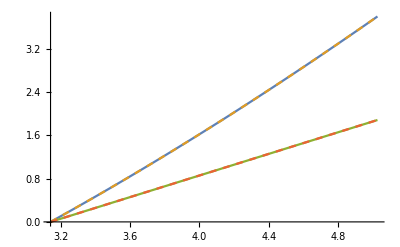

```mathematica
Plot[Evaluate[{
primitiveEigRtAnalyt[1][a,b][t],
primitiveEigRtNum[1][a,b][t],
primitiveEigRtAnalyt[2][a,b][t],
primitiveEigRtNum[2][a,b][t]
}/.{a->1,b->1}
],relevantdomain,PlotStyle->stylecompare]
```

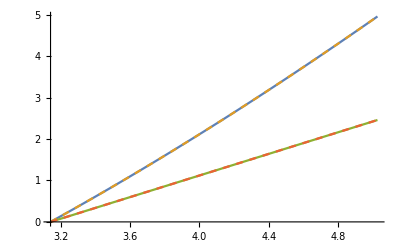

```mathematica
Plot[Evaluate[{
primitiveEigRtAnalyt[1][a,b][t],
primitiveEigRtNum[1][a,b][t],
primitiveEigRtAnalyt[2][a,b][t],
primitiveEigRtNum[2][a,b][t]
}/.{a->1.7,b->2.1}
],relevantdomain,PlotStyle->stylecompare]
```

### Integrals in the higher order parallel (∥) recurrence relation (HOvaP)

#### Semi-analytic parallel (∥) / normal (⊥) decomposition

```mathematica
Definition[va]
```

va[n_,k_][a_,b_,T_][t_]=vaN[n,k][a,b,T][t]+vaP[n,k][a,b,T][t]

```mathematica
vaNumFulling[n_,k_][a_,b_,T_][t_]:=vaNNumFulling[n,k][a,b,T][t]+vaPNumFulling[n,k][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T]
```

#### Problematic integrands

```mathematica
IntegrandinHOvaP[n_,k_][a_,b_,T_][t1_]:=mUinv[a,b][t1].(-1/2(p[k][a,b][t1])^(-1/2)mP[k][a,b][t1].va[n-1,k][a,b,T]''[t1]+1/4(p[k][a,b][t1])^(-3/2)p[k][a,b]'[t1]mP[k][a,b][t1].va[n-1,k][a,b,T]'[t1]+1/2(p[k][a,b][t1])^(1/2)((p[k][a,b]''[t1])/(4p[k][a,b][t1]^2)-(5p[k][a,b]'[t1]^2)/(16p[k][a,b][t1]^3))mP[k][a,b][t1].va[n-1,k][a,b,T][t1]-mP[k][a,b][t1].vaN[n,k][a,b,T]'[t1])
```

#### Semi-analytic higher order parallel (∥) recurrence relation (ζ-dependent)

Recall of HOvaP:

```mathematica
Definition[HOvaP]
```

HOvaP[n_,k_][a_,b_,T_][t_]:=Simplify[mU[a,b][t].∑_(l=1)^nl[k] Subscript[ζ,n,k,(+l j)/ⅈ] e[k,l][a,b][ti]+mU[a,b][t].∫_ti^t mUinv[a,b][t1].(-1/2 1/(√(p[k][a,b][t1])) mP[k][a,b][t1].va[n-1,k][a,b,T]''[t1]+1/4 (p[k][a,b][t1])^(-3/2) p[k][a,b]'[t1] mP[k][a,b][t1].va[n-1,k][a,b,T]'[t1]+1/2 √(p[k][a,b][t1]) ((p[k][a,b]''[t1])/(4 (p[k][a,b][t1])^2)-(5 (p[k][a,b]'[t1])^2)/(16 (p[k][a,b][t1])^3)) mP[k][a,b][t1].va[n-1,k][a,b,T][t1]-mP[k][a,b][t1].vaN[n,k][a,b,T]'[t1])ⅆt1]

Semi-analytic version of HOvaP for all-1s ζ-constants:

```mathematica
NHOvaPAll1s[n_,k_][c_,d_,S_][t_]:=mU[c,d][t].∑_(l=1)^nl[k] Subscript[ζ, n,k,+l j/ⅈ] e[k,l][c,d][ti]+mU[c,d][t].Array[ParametricNPrimitiveValue[{(IntegrandinHOvaP[n,k][c,d,S][t]/.Subscript[ζ, _,_,_]->1)[[#]],ti},
intN,{t,tmin,tmax},{a,b,T}][c,d,S][t]&,dim]/.Subscript[ζ, _,_,_]->1
```

Semi-analytic version of HOvaP for my own old i.c.’s:

```mathematica
constsOwn[T_]={Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0,Subscript[ζ, 0,1,1]->0,Subscript[ζ, 1,1,1]->0,Subscript[ζ, 0,1,2]->-1,Subscript[ζ, 1,1,2]->0,Subscript[ζ, 1,2,1]->-2/(-1+π^(1/4)-√π+π^(3/4))-ⅈ T Subscript[ζ, 0,2,1],Subscript[ζ, 0,2,1]->((1+3 π)/π^(3/4)-(2 ⅈ (-T+2 √π T-2 π^(3/2) T+π^2 T))/π^(1/4))/(-1+π)^2,Subscript[ζ, 2,1,1]->0,Subscript[ζ, 2,1,2]->0,Subscript[ζ, 2,2,1]->0,Subscript[ζ, 2,2,2]->0};
```

```mathematica
NHOvaPOwn[n_,k_][c_,d_,S_][t_]:=mU[c,d][t].∑_(l=1)^nl[k] Subscript[ζ, n,k,+l j/ⅈ] e[k,l][c,d][ti]+mU[c,d][t].Array[ParametricNPrimitiveValue[{(IntegrandinHOvaP[n,k][c,d,S][t]/.j->ⅈ//.constsOwn[S])[[#]],ti},
intN,{t,tmin,tmax},{a,b,T}][c,d,S][t]&,dim]/.j->ⅈ//.constsOwn[S]
```

Semi-analytic version of HOvaP for Fulling’s i.c.’s:

```mathematica
NHOvaPFulling[n_,k_][c_,d_,S_][t_]:=mU[c,d][t].∑_(l=1)^nl[k] Subscript[ζ, n,k,+l j/ⅈ] e[k,l][c,d][ti]+mU[c,d][t].Array[ParametricNPrimitiveValue[{(IntegrandinHOvaP[n,k][c,d,S][t]/.j->ⅈ//.constsFulling[c,d,S])[[#]],ti},
intN,{t,tmin,tmax},{a,b,T}][c,d,S][t]&,dim]/.j->ⅈ//.constsFulling[c,d,S]
```

#### Semi-analytic higher order normal (⊥) recurrence relation (ζ-dependent)

```mathematica
Definition[HOvaN]
```

HOvaN[n_,k_][a_,b_,T_][t_]:=Simplify[1/(∑_(kp=1)^nk (p[kp][a,b][t]-p[k][a,b][t]))(2 √(p[k][a,b][t]) (II.mP[k][a,b][t]).va[n-1,k][a,b,T]'[t]-(p[k][a,b]'[t] (II.mP[k][a,b][t]).va[n-2,k][a,b,T]'[t])/(2 p[k][a,b][t])+(II.mP[k][a,b][t]).va[n-2,k][a,b,T]''[t]-p[k][a,b][t] ((p[k][a,b]''[t])/(4 (p[k][a,b][t])^2)-(5 (p[k][a,b]'[t])^2)/(16 (p[k][a,b][t])^3)) (II.mP[k][a,b][t]).va[n-2,k][a,b,T][t])]

I only define this normal one for the relevant Fulling’s i.c.’s:

```mathematica
NHOvaNFulling[n_,k_][a_,b_,T_][t_]:=(2 √(p[k][a,b][t]) (II.mP[k][a,b][t]).vaNumFulling[n-1,k][a,b,T]'[t]-1/(2 p[k][a,b][t])p[k][a,b]'[t] (II.mP[k][a,b][t]).vaNumFulling[n-2,k][a,b,T]'[t]+(II.mP[k][a,b][t]).vaNumFulling[n-2,k][a,b,T]''[t]-p[k][a,b][t] ((p[k][a,b]''[t])/(4 (p[k][a,b][t])^2)-(5 (p[k][a,b]'[t])^2)/(16 (p[k][a,b][t])^3)) (II.mP[k][a,b][t]).vaNumFulling[n-2,k][a,b,T][t])/(∑_(kp=1)^nk (p[kp][a,b][t]-p[k][a,b][t]))//Simplify
```

#### Semi-analytic parallel (∥) coefficients

Zeroth order: the analytical  ^k a_0^∥

```mathematica
For[k=1,k<=nk,k++,{
vaPNumFulling[0,k][a_,b_,T_][t_]=vaP[0,k][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T]
}]
ClearAll[k]
```

First and higher orders:  ^k a_n^∥

```mathematica
For[n=1,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
vaPNumFulling[n,k][a_,b_,T_][t_]=NHOvaPFulling[n,k][a,b,T][t]
}]
}]
ClearAll[n,k]
```

#### Semi-analytic normal (⊥) coefficients

Zeroth order: the analytical  ^k a_0^⊥ (which are zero)

```mathematica
For[k=1,k<=nk,k++,{
vaNNumFulling[0,k][a_,b_,T_][t_]=vaN[0,k][a,b,T][t]
}]
ClearAll[k]
```

First order: the analytical  ^k a_1^⊥ (which involve  ^k a_0^∥ ~ ^k e, analytical)

```mathematica
For[k=1,k<=nk,k++,{
vaNNumFulling[1,k][a_,b_,T_][t_]=vaN[1,k][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T]
}]
ClearAll[k]
```

Higher orders:  ^k a_n^∥

```mathematica
For[n=2,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
vaNNumFulling[n,k][a_,b_,T_][t_]=NHOvaNFulling[n,k][a,b,T][t]
}]
}]
ClearAll[n,k]
```

### Semi-analytic solutions

Semi-analytic vector adiabatic ansatz function:

```mathematica
VecAdbAnsatzNumFulling[o_,k_][c_,d_,S_][s_]:=(p[k][c,d][s])^(-1/4) Exp[j S primitiveEigRtNum[k][c,d][s]] ∑_(n=0)^o (j S)^-n vaNumFulling[n,k][c,d,S][s]
```

Semi-analytic vector adiabatic general expansion function:

```mathematica
VecAdbGralExpNumFulling[o_][a_,b_,T_][t_]:=(∑_(k=1)^nk VecAdbAnsatzNumFulling[o,k][a,b,T][t]/.j->+ⅈ)+(∑_(k=1)^nk VecAdbAnsatzNumFulling[o,k][a,b,T][t]/.j->-ⅈ)
```

Semi-analytic adiabatic solution:

```mathematica
For[n=0,n<=adbOrd,n++,
vxAdbNumFulling[n][a_,b_,T_][t_]=VecAdbGralExpNumFulling[n][a,b,T][t]//.constsFulling[a,b,T]]
ClearAll[n]
```

## Plots of results (for Fulling’s i.c.’s)

#### Parameter values for static plots and initial data

{a->1,b->1,T->10}

## Fully-analytic solution plots (T-manipulative)

#### Static plot for {a → 1, b → 1, T → 10}

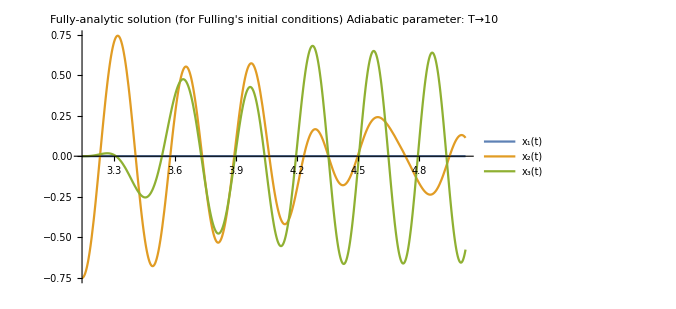

```mathematica
Plot[Evaluate[{
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]
}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"Fully-analytic solution (for Fulling's initial conditions)
Adiabatic parameter: T"->10,
ImageSize->500]
```

#### Manipulable plot

```mathematica
tf//N
```

5.02655

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"Fully-analytic solution (for Fulling's initial conditions)",
ImageSize->500],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Adiabatic solution plots (T-manipulative)

### 0th order

#### Static plot for {a → 1, b → 1, T → 10}

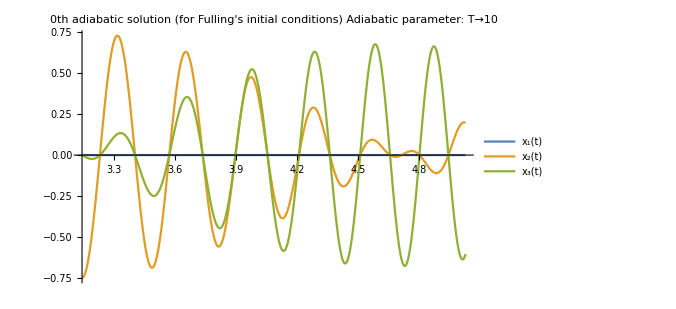

```mathematica
Plot[Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],
Re[vxAdbFulling[0][a,b,T][t][[2]]],
Re[vxAdbFulling[0][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"0th adiabatic solution (for Fulling's initial conditions)
Adiabatic parameter: T"->10,ImageSize->500]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],
Re[vxAdbFulling[0][a,b,T][t][[2]]],
Re[vxAdbFulling[0][a,b,T][t][[3]]]},{t,Start,Start+WindowSize},
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"Adiabatic solution (for Fulling's initial conditions)",
ImageSize->500],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 1st order

#### Static plot for {a → 1, b → 1, T → 10}

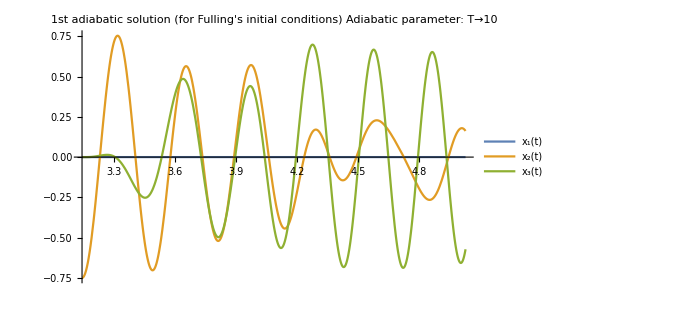

```mathematica
Plot[Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],
Re[vxAdbFulling[1][a,b,T][t][[2]]],
Re[vxAdbFulling[1][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"1st adiabatic solution (for Fulling's initial conditions)
Adiabatic parameter: T"->10,ImageSize->500]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],
Re[vxAdbFulling[1][a,b,T][t][[2]]],
Re[vxAdbFulling[1][a,b,T][t][[3]]]},{t,Start,Start+WindowSize},
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"Adiabatic solution (for my own initial conditions)",
ImageSize->500],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 2nd order

#### Static plot for {a → 1, b → 1, T → 10}

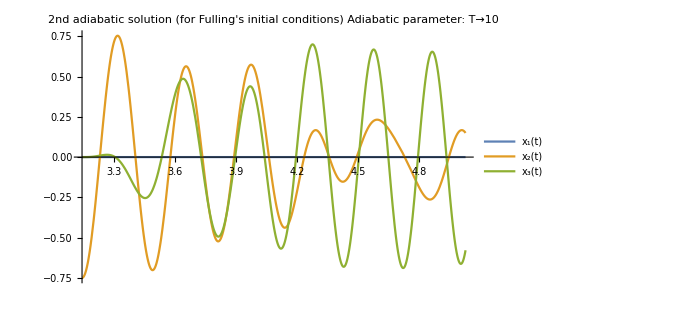

```mathematica
Plot[Evaluate[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],
Re[vxAdbFulling[2][a,b,T][t][[2]]],
Re[vxAdbFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"2nd adiabatic solution (for Fulling's initial conditions)
Adiabatic parameter: T"->10,ImageSize->500]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],
Re[vxAdbFulling[2][a,b,T][t][[2]]],
Re[vxAdbFulling[2][a,b,T][t][[3]]]},{t,Start,Start+WindowSize},
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","x_3(t)"},
PlotLabel->"Adiabatic solution (for Fulling's initial conditions)",
ImageSize->500],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Semi-analytic solution plots (T-manipulative)

### 0th order semi-analytic adiabatic solution

#### Static plot for {a → 1, b → 1, T → 10}

```mathematica
vxAdbNumFulling[0][a,b,T][t]
```

{0,(ⅇ^(-ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4)),(ⅇ^(-ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))}

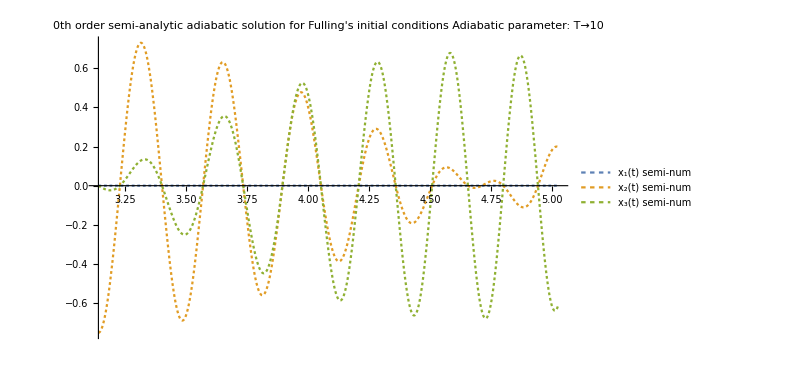

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->style0th,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->style0th,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 1st order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

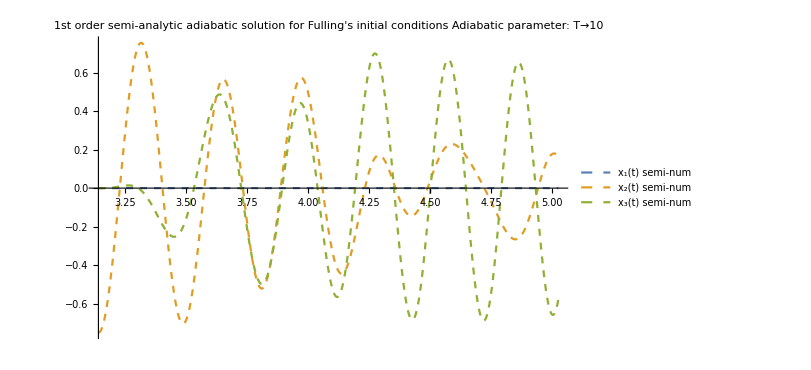

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->style1st,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->style1st,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 2nd order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

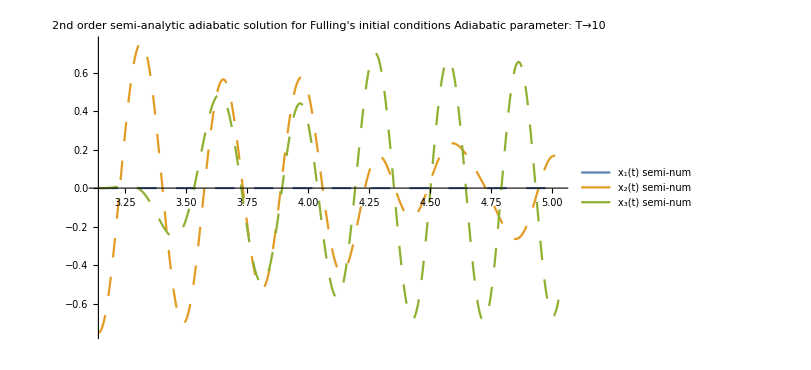

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->style2nd,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->style2nd,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Altogether (0th, 1st and 2nd order, semi-analytic adiabatic solutions)

#### Static plot for {a → 1, b → 1, T → 10}

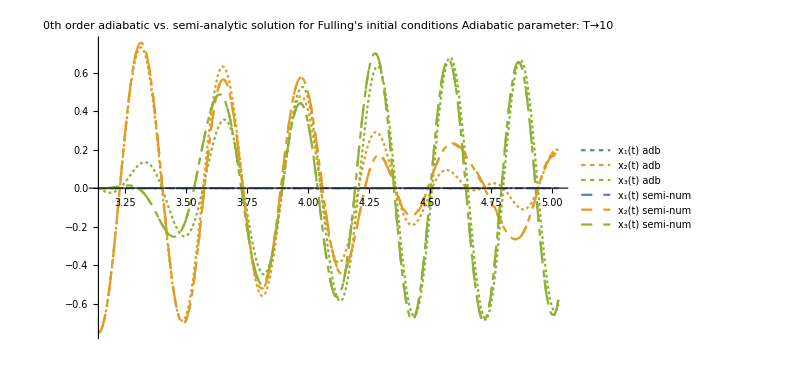

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order adiabatic vs. semi-analytic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order adiabatic vs. semi-analytic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Manipulable higher-order integration constants

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFullingManip[2][a,b,T,c1r,c1i,c2r,c2i][t][[1]]],Re[vxAdbFullingManip[2][a,b,T,c1r,c1i,c2r,c2i][t][[2]]],Re[vxAdbFullingManip[2][a,b,T,c1r,c1i,c2r,c2i][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1}
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"2nd order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,5},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,3.5,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01},
Style["
2nd order i.c.'s",12],{{c1r,0},0,2},{{c1i,0},0,2},{{c2r,0},0,2},{{c2i,0},0,2}]
```

## Comparison of results (for Fulling’s i.c.’s)

## Adiabatic vs. fully numerical solutions

### 0th order adiabatic solution vs. numerical

#### Static plot for {a → 1, b → 1, T → 10}

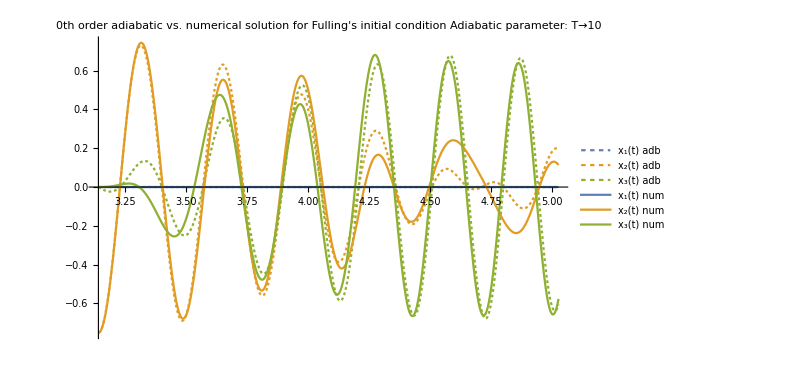

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],
Re[vxAdbFulling[0][a,b,T][t][[2]]],
Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"0th order adiabatic vs. numerical solution for Fulling's initial condition
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],
Re[vxAdbFulling[0][a,b,T][t][[2]]],
Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"0th order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 1st order adiabatic solution vs. numerical

#### Static plot for {a → 1, b → 1, T → 10}

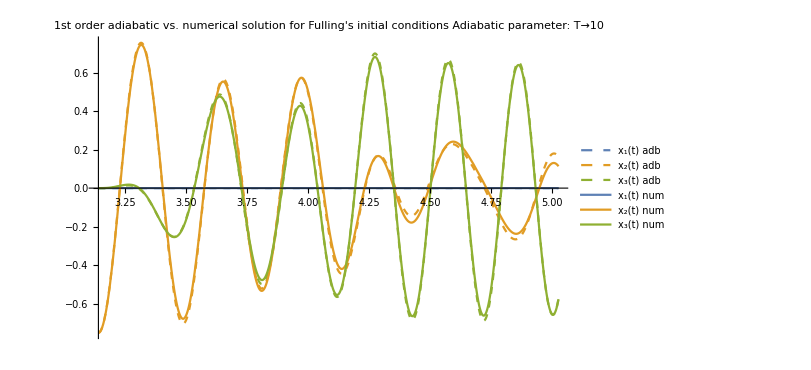

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],
Re[vxAdbFulling[1][a,b,T][t][[2]]],
Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st order adiabatic vs. numerical solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],
Re[vxAdbFulling[1][a,b,T][t][[2]]],
Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 2nd order adiabatic solution vs. numerical

#### Static plot for {a → 1, b → 1, T → 10}

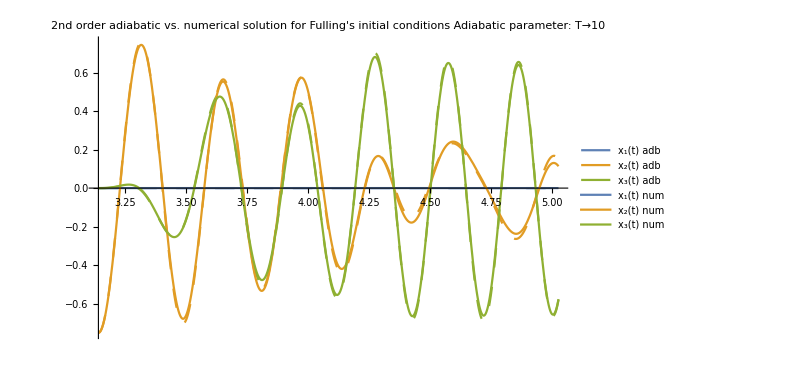

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],
Re[vxAdbFulling[2][a,b,T][t][[2]]],
Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style2nd,stylenum},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"2nd order adiabatic vs. numerical solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],
Re[vxAdbFulling[2][a,b,T][t][[2]]],
Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style2nd,stylenum},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"2nd order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Adiabatic comparisons

#### 0th vs. 1st vs. 2nd adiabatic orders (static, for {a → 1, b → 1, T → 10})

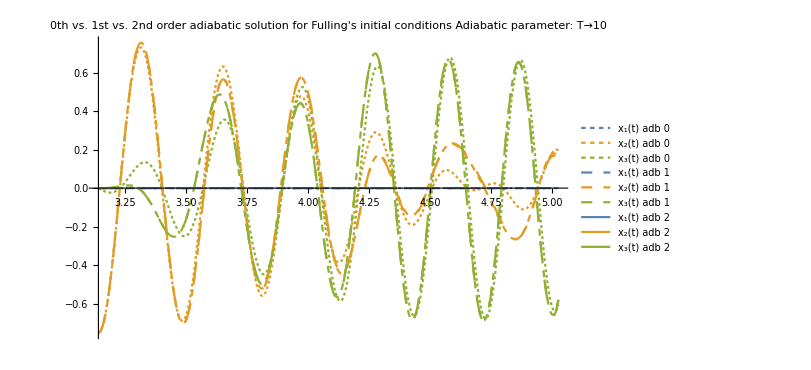

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0","x_3(t) adb 0",
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2"},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### 0th vs. 1st vs. 2nd adiabatic orders (manipulative)

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]]}
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0","x_3(t) adb 0",
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2"},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

#### 1st vs. 2nd adiabatic orders (static, for {a → 1, b → 1, T → 10})

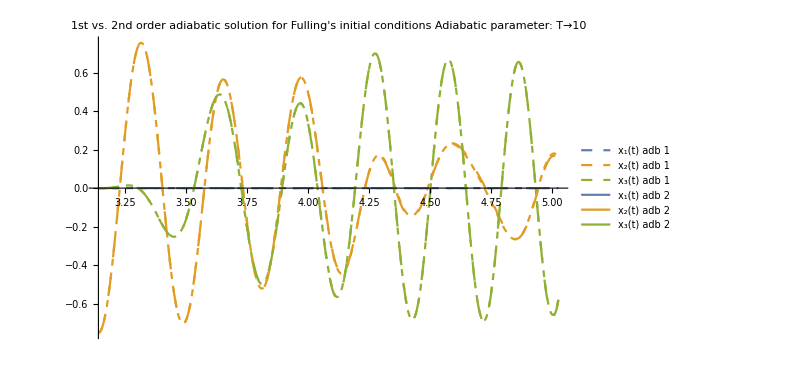

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2"},
PlotLabel->"1st vs. 2nd order adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### 1st vs. 2nd adiabatic orders (manipulative)

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]]}
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2"},
PlotLabel->"1st vs. 2nd order adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Full comparison: 0th vs. 1st vs. 2nd adiabatic orders vs. numerical solution

#### Static plot for {a → 1, b → 1, T → 10}

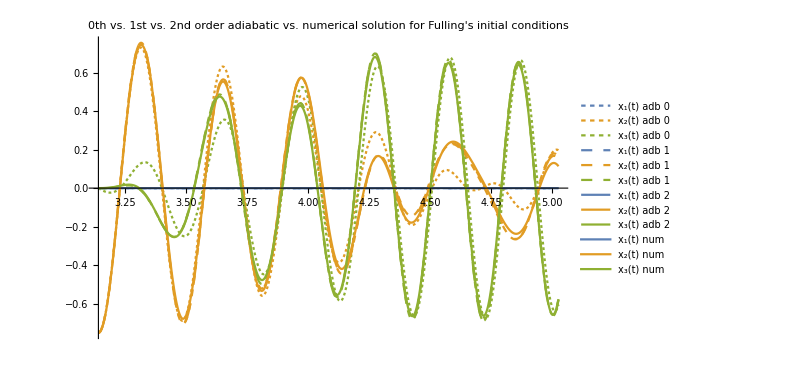

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0","x_3(t) adb 0",
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0","x_3(t) adb 0",
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

```mathematica
Flatten[{style0th,style1st,style2nd,stylenum},1]
```

{{Dashing[Tiny],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Tiny],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[Tiny],RGBColor[0.560181, 0.691569, 0.194885]},{Dashing[Small],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Small],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[Small],RGBColor[0.560181, 0.691569, 0.194885]},{Dashing[Large],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Large],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[Large],RGBColor[0.560181, 0.691569, 0.194885]},{SolidData,RGBColor[0.368417, 0.506779, 0.709798]},{SolidData,RGBColor[0.880722, 0.611041, 0.142051]},{SolidData,RGBColor[0.560181, 0.691569, 0.194885]}}

### Partial comparison: 1st vs. 2nd adiabatic orders vs. numerical solution

#### Static plot for {a → 1, b → 1, T → 10}

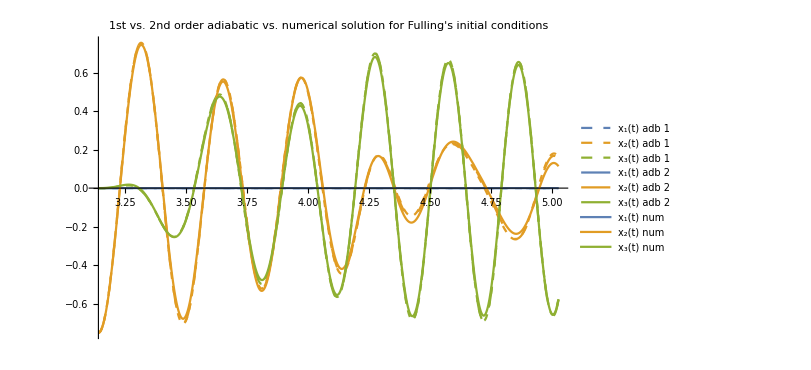

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st vs. 2nd order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st vs. 2nd order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Adiabatic vs. semi-analytic solutions

### 0th order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

```mathematica
vxAdbNumFulling[0][a,b,T][t]
```

{0,(ⅇ^(-ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4)),(ⅇ^(-ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ T ParametricFunction[<>][a,b][t]) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))}

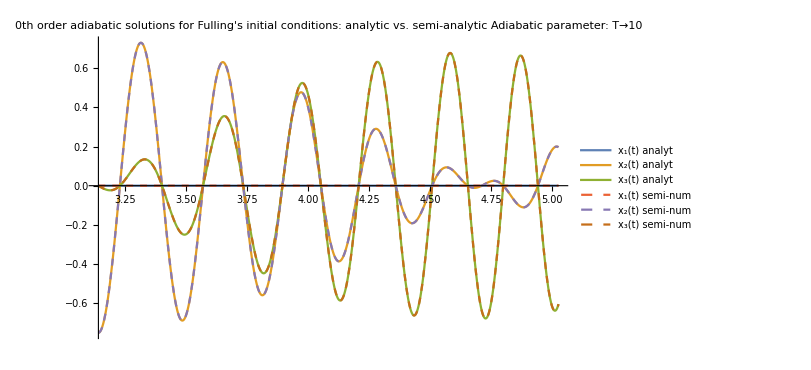

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]]}/.T->10
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{
"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt",
"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order analytic vs. semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 1st order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

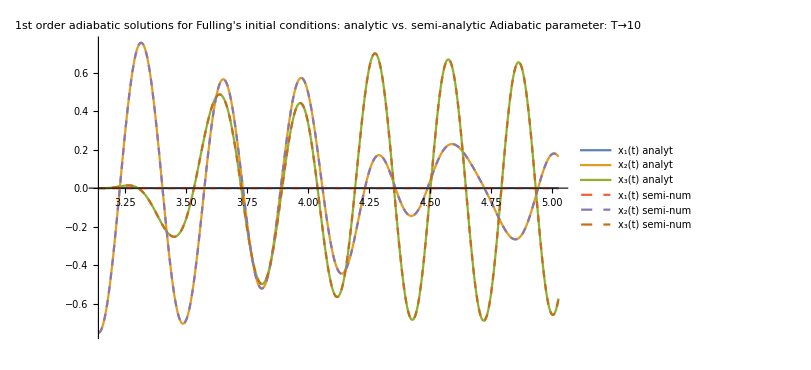

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]]}/.T->10
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{
"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt",
"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order analytic vs. semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 2nd order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

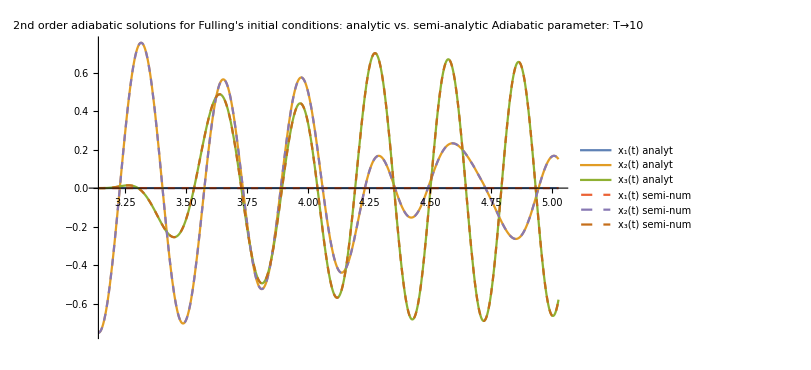

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.T->10
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{
"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt",
"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order analytic vs. semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Altogether (0th, 1st and 2nd order solutions, adiabatic vs. semi-analytic)

#### Static plot for {a → 1, b → 1, T → 10}

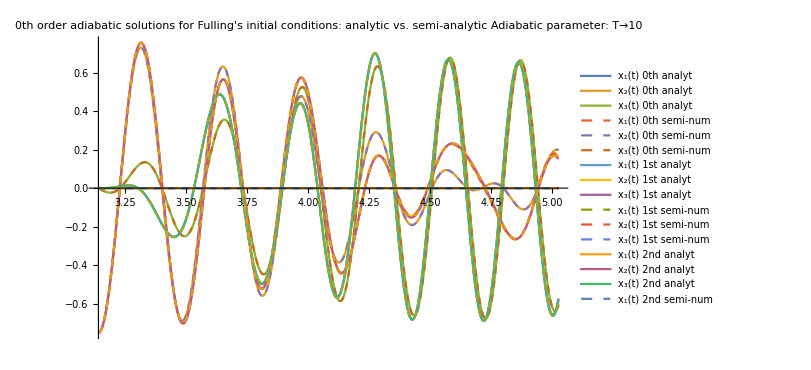

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) 0th analyt","x_2(t) 0th analyt","x_3(t) 0th analyt",
"x_1(t) 0th semi-num","x_2(t) 0th semi-num","x_3(t) 0th semi-num",
"x_1(t) 1st analyt","x_2(t) 1st analyt","x_3(t) 1st analyt",
"x_1(t) 1st semi-num","x_2(t) 1st semi-num","x_3(t) 1st semi-num",
"x_1(t) 2nd analyt","x_2(t) 2nd analyt","x_3(t) 2nd analyt",
"x_1(t) 2nd semi-num","x_2(t) 2nd semi-num","x_3(t) 2nd semi-num"
},
PlotLabel->"0th order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

I plot this because they seemed too similar, but that’s because for T → 10 they are similar (although not exactly the same, as we can see here).

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]]}/.T->10
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) 0th analyt","x_2(t) 0th analyt","x_3(t) 0th analyt",
"x_1(t) 0th semi-num","x_2(t) 0th semi-num","x_3(t) 0th semi-num",
"x_1(t) 1st analyt","x_2(t) 1st analyt","x_3(t) 1st analyt",
"x_1(t) 1st semi-num","x_2(t) 1st semi-num","x_3(t) 1st semi-num",
"x_1(t) 2nd analyt","x_2(t) 2nd analyt","x_3(t) 2nd analyt",
"x_1(t) 2nd semi-num","x_2(t) 2nd semi-num","x_3(t) 2nd semi-num"
},
PlotLabel->"All orders adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Adiabatic semi-analytic vs. fully numerical solutions

### 0th order adiabatic semi-analytic solution vs. fully numerical

#### Static plot for {a → 1, b → 1, T → 10}

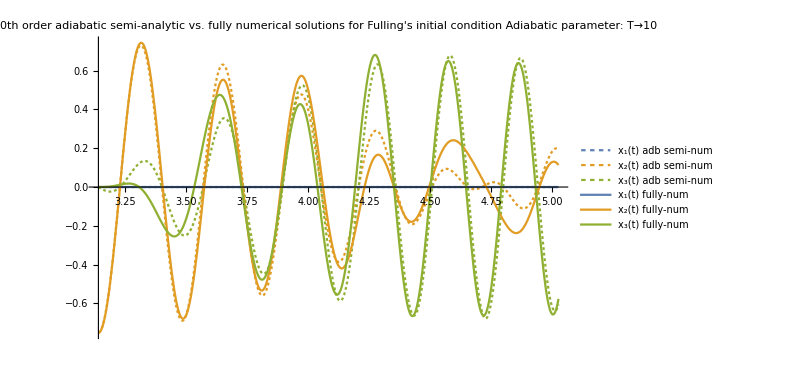

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],
Re[vxAdbNumFulling[0][a,b,T][t][[2]]],
Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num","x_3(t) adb semi-num","x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"0th order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial condition
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],
Re[vxAdbNumFulling[0][a,b,T][t][[2]]],
Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num","x_3(t) adb semi-num","x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"0th order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 1st order adiabatic semi-analytic solution vs. fully numerical

#### Static plot for {a → 1, b → 1, T → 10}

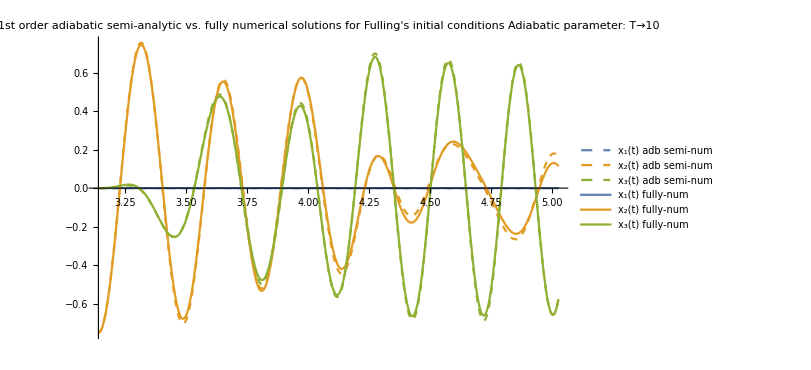

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],
Re[vxAdbNumFulling[1][a,b,T][t][[2]]],
Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num","x_3(t) adb semi-num","x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"1st order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],
Re[vxAdbNumFulling[1][a,b,T][t][[2]]],
Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num","x_3(t) adb semi-num","x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"1st order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 2nd order adiabatic semi-analytic solution vs. fully numerical

#### Static plot for {a → 1, b → 1, T → 10}

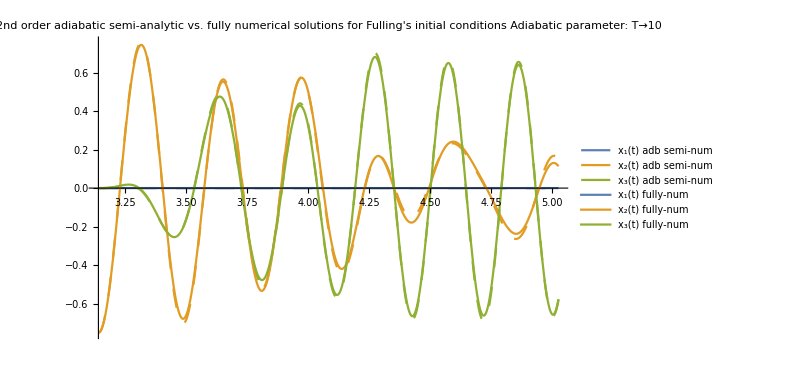

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],
Re[vxAdbNumFulling[2][a,b,T][t][[2]]],
Re[vxAdbNumFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style2nd,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num","x_3(t) adb semi-num","x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"2nd order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],
Re[vxAdbNumFulling[2][a,b,T][t][[2]]],
Re[vxAdbNumFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],
Re[x[2][a,b,T][t]],
Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style2nd,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num","x_3(t) adb semi-num","x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"2nd order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Full comparison: 0th vs. 1st vs. 2nd orders adiabatic semi-analytic solution vs. fully numerical solution

#### Static plot for {a → 1, b → 1, T → 10}

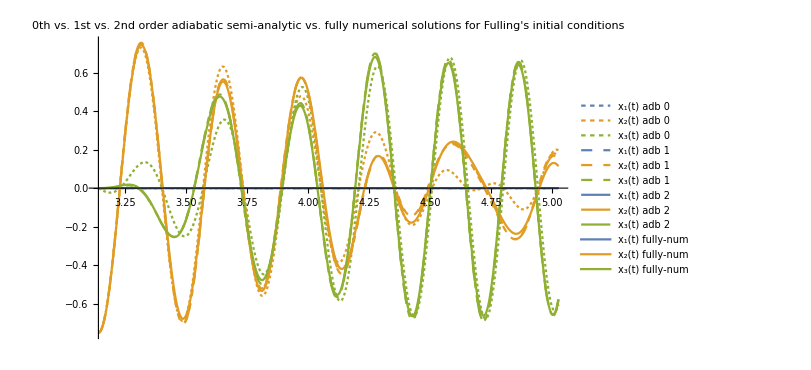

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0","x_3(t) adb 0",
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbNumFulling[0][a,b,T][t][[1]]],Re[vxAdbNumFulling[0][a,b,T][t][[2]]],Re[vxAdbNumFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0","x_3(t) adb 0",
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

```mathematica
Flatten[{style0th,style1st,style2nd,stylenum},1]
```

{{Dashing[Tiny],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Tiny],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[Tiny],RGBColor[0.560181, 0.691569, 0.194885]},{Dashing[Small],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Small],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[Small],RGBColor[0.560181, 0.691569, 0.194885]},{Dashing[Large],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Large],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[Large],RGBColor[0.560181, 0.691569, 0.194885]},{SolidData,RGBColor[0.368417, 0.506779, 0.709798]},{SolidData,RGBColor[0.880722, 0.611041, 0.142051]},{SolidData,RGBColor[0.560181, 0.691569, 0.194885]}}

### Partial comparison: 1st vs. 2nd orders adiabatic semi-analytic solution vs. fully numerical solution

#### Static plot for {a → 1, b → 1, T → 10}

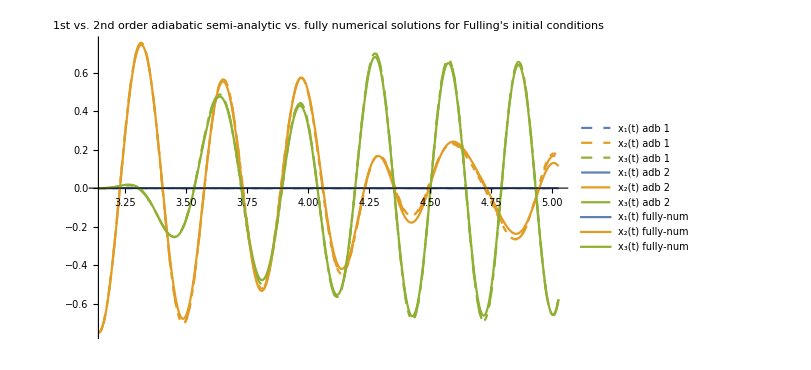

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"1st vs. 2nd order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbNumFulling[1][a,b,T][t][[1]]],Re[vxAdbNumFulling[1][a,b,T][t][[2]]],Re[vxAdbNumFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumFulling[2][a,b,T][t][[1]]],Re[vxAdbNumFulling[2][a,b,T][t][[2]]],Re[vxAdbNumFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) fully-num","x_2(t) fully-num","x_3(t) fully-num"},
PlotLabel->"1st vs. 2nd order adiabatic semi-analytic vs. fully numerical solutions for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Fulling’s constants, paper vs. computation

The differences are the a, b constants and the imaginary parts, so plotting the real part for {a->1,b->1} doesn’t show any difference.  ✔

#### Static plot

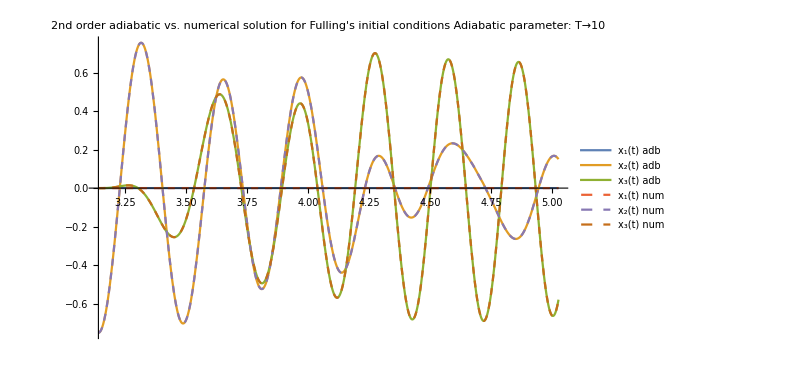

```mathematica
Plot[
Evaluate@Re[{
VecAdbGralExp[2][a,b,T][t]/.constsFullingPaper,
VecAdbGralExp[2][a,b,T][t]//.constsFulling[a,b,T]
}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"2nd order adiabatic vs. numerical solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

## Manipulable integration constants

```mathematica
constsTest[
c011p_,c011m_,c012p_,c012m_,c02p_,c02m_,
c111p_,c111m_,c112p_,c112m_,c12p_,c12m_,
c211p_,c211m_,c212p_,c212m_,c22p_,c22m_]={
Subscript[ζ, 0,1,1]->c011p,Subscript[ζ, 0,1,-1]->c011m,Subscript[ζ, 0,1,2]->c012p,Subscript[ζ, 0,1,-2]->c012m,Subscript[ζ, 0,2,1]->c02p,Subscript[ζ, 0,2,-1]->c02m,
Subscript[ζ, 1,1,1]->c111p,Subscript[ζ, 1,1,-1]->c111m,Subscript[ζ, 1,1,2]->c112p,Subscript[ζ, 1,1,-2]->c112m,Subscript[ζ, 1,2,1]->c12p,Subscript[ζ, 1,2,-1]->c12m,
Subscript[ζ, 2,1,1]->c211p,Subscript[ζ, 2,1,-1]->c211m,Subscript[ζ, 2,1,2]->c212p,Subscript[ζ, 2,1,-2]->c212m,Subscript[ζ, 2,2,1]->c22p,Subscript[ζ, 2,2,-1]->c22m};
```

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
VecAdbGralExp[1][a,b,T][t],VecAdbGralExp[2][a,b,T][t],
(*x[1][a,b,T][t],x[2][a,b,T][t],x[3][a,b,T][t]}/.solFullNumFulling*)}
/.{a->1,b->1}/.constsTest[c011p,c011m,c012p,c012m,c02p,c02m,c111p,c111m,c112p,c112m,c12p,c12m,c211p,c211m,c212p,c212m,c22p,c22m]
],{t,Start,Start+WindowSize},
PlotRange->All,PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1","x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st vs. 2nd order adiabatic vs. numerical solution for Fulling's initial conditions",ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01},Style["
Integration constants",12],{{c011p,0},-2,2},{{c011m,0},-2,2},{{c012p,1},-2,2},{{c012m,1},-2,2},{{c02p,1},-2,2},{{c02m,1},-2,2},{{c111p,0},-2,2},{{c111m,0},-2,2},{{c112p,1},-2,2},{{c112m,1},-2,2},{{c12p,1},-2,2},{{c12m,1},-2,2},{{c211p,0},-2,2},{{c211m,0},-2,2},{{c212p,1},-2,2},{{c212m,1},-2,2},{{c22p,1},-2,2},{{c22m,1},-2,2}]
```

## Attempt to obtain the old results (summer ‘23’s plot)

I think that result was wrong, but I still don’t know why it appeared (and why the 2nd order looked so much better than the 1st one).

### Constants and i.c.’s

#### Old own i.c.’s

```mathematica
(*icOwnSol=AdbVecExpGral[t]//.constsOwn/.t->ti//Simplify*)
icOwnSol={0,1/π^(1/4),0}
```

{0,1/π^(1/4),0}

```mathematica
(*icOwnDeriv=AdbVecExpGral'[t]//.constsOwn/.t->ti//Simplify*)
icOwnDeriv={0,(ⅈ (-5+5 π+16 π^2-8 ⅈ π^(3/2) T+8 ⅈ π^(5/2) T+32 π^4 T^2+π^3 (48-32 T^2)))/(32 (-1+π) π^(11/4) T),0}
```

{0,(ⅈ (-5+5 π+16 π^2-8 ⅈ π^(3/2) T+8 ⅈ π^(5/2) T+32 π^4 T^2+π^3 (48-32 T^2)))/(32 (-1+π) π^(11/4) T),0}

#### Own constants

```mathematica
constsOwn[T_]={Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0,Subscript[ζ, 0,1,1]->0,Subscript[ζ, 1,1,1]->0,Subscript[ζ, 0,1,2]->-1,Subscript[ζ, 1,1,2]->0,Subscript[ζ, 1,2,1]->-2/(-1+π^(1/4)-√π+π^(3/4))-ⅈ T Subscript[ζ, 0,2,1],Subscript[ζ, 0,2,1]->((1+3 π)/π^(3/4)-(2 ⅈ (-T+2 √π T-2 π^(3/2) T+π^2 T))/π^(1/4))/(-1+π)^2,Subscript[ζ, 2,1,1]->0,Subscript[ζ, 2,1,2]->0,Subscript[ζ, 2,2,1]->0,Subscript[ζ, 2,2,2]->0};
```

#### Correct own i.c.’s

```mathematica
icOwnSol=VecAdbGralExp[2][a,b,T][t]/.t->ti//.constsOwn[T]//Simplify;
icOwnDeriv=VecAdbGralExp[2][a,b,T]'[t]/.t->ti//.constsOwn[T]//Simplify;
```

```mathematica
icOwnSol/.{a->1,b->1}
icOwnDeriv/.{a->1,b->1}
```

{0,(-2 ⅈ+4 √π T+(-1+π)^3 √π T+8 π^2 T-4 π^(5/2) T-π (6 ⅈ+8 T))/((-1+π)^3 π^(3/4) T),-(2 ⅈ)/((-1+π) T)}

{0,1/(64 (-1+π)^4 π^(17/4) T^2)(15-60 π+74 π^2-128 ⅈ π^(17/4) T+384 ⅈ π^(21/4) T-384 ⅈ π^(25/4) T+128 ⅈ π^(29/4) T-16 π^7 (1+16 ⅈ T) T^2+64 ⅈ π^(17/2) T^3-4 π^3 (7+4 T^2)+32 π^5 (3-3 T^2+8 ⅈ T^3)-16 π^6 (3-20 T^2-16 ⅈ T^3)-π^4 (49-64 T^2+256 (T^2+ⅈ T^3))-2 π^(11/2) (128 ⅈ T^3+T (91 ⅈ+256 T)+64 ⅈ T (-3+3 ⅈ T+8 T^2)-182 (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))-40 ⅈ π^(5/2) (T+2 ⅈ (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))-32 ⅈ π^(15/2) (-3 T+8 T^3+2 ⅈ (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))+128 ⅈ π^(13/2) (T+3 T^3+T (-3+4 T^2)+2 ⅈ (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))-10 π^(3/2) (-ⅈ T+2 (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))-4 π^(7/2) (-39 ⅈ T+32 T^2+14 (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))-8 π^(9/2) (-8 ⅈ T^3-T (59 ⅈ+64 T)+16 T (ⅈ+2 T-4 ⅈ T^2)+22 (2 ArcCoth[√π]+Log[(-1+√π)/(1+√π)]))),-1/(2 (-1+π)^4 π^(3/4) T^2)(-4 (1+π^(1/4))^4 (-1+π^(1/4)-√π+π^(3/4))^3 π^(3/4) T^2+2 (1+(1+π^(1/4))^4 (-1+π^(1/4)-√π+π^(3/4))^3 π^(3/4)+π (3-4 ⅈ T)+2 ⅈ √π T+4 ⅈ π^2 T-2 ⅈ π^(5/2) T)+(-1+π)^2 T (ⅈ+3 ⅈ π-2 √π T+2 π^(5/2) T))}

### Fully numerical solution for my own i.c.’s

```mathematica
solFullNumOwn=ParametricNDSolve[{
Eom[mM[a,b][t],vx[t]][[1]]==0,
Eom[mM[a,b][t],vx[t]][[2]]==0,
Eom[mM[a,b][t],vx[t]][[3]]==0,
x[1][ti]==icOwnSol[[1]],x[1]'[ti]==icOwnDeriv[[1]],
x[2][ti]==icOwnSol[[2]],x[2]'[ti]==icOwnDeriv[[2]],
x[3][ti]==icOwnSol[[3]],x[3]'[ti]==icOwnDeriv[[3]]},
{x[1],x[2],x[3]},{t,tmin,tmax},{a,b,T}]
```

{x[1]→ParametricFunction[<>],x[2]→ParametricFunction[<>],x[3]→ParametricFunction[<>]}

```mathematica
vxFullNumOwn[a_,b_,T_][s_]=Evaluate[{x[1][t],x[2][t],x[3][t]}/.solFullNumOwn]/.t->s;
vxFullNumOwn[a,b,T][t]
```

{ParametricFunction[<>][t],ParametricFunction[<>][t],ParametricFunction[<>][t]}

### Adiabatic solution for my own i.c.’s

```mathematica
For[n=0,n<=adbOrd,n++,
vxAdbOwn[n][a_,b_,T_][t_]=VecAdbGralExp[n][a,b,T][t]//.constsOwn[T]]
ClearAll[n];
```

### Partial comparison: 1st vs. 2nd adiabatic orders vs. numerical solution

#### Static plot for {a → 1, b → 1, T → 10}

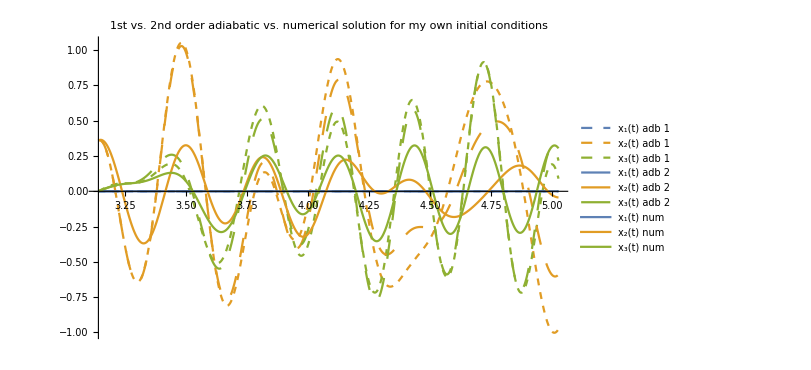

```mathematica
Plot[
Evaluate[{
Re[vxAdbOwn[1][a,b,T][t][[1]]],Re[vxAdbOwn[1][a,b,T][t][[2]]],Re[vxAdbOwn[1][a,b,T][t][[3]]],
Re[vxAdbOwn[2][a,b,T][t][[1]]],Re[vxAdbOwn[2][a,b,T][t][[2]]],Re[vxAdbOwn[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumOwn/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st vs. 2nd order adiabatic vs. numerical solution for my own initial conditions",
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbOwn[1][a,b,T][t][[1]]],Re[vxAdbOwn[1][a,b,T][t][[2]]],Re[vxAdbOwn[1][a,b,T][t][[3]]],
Re[vxAdbOwn[2][a,b,T][t][[1]]],Re[vxAdbOwn[2][a,b,T][t][[2]]],Re[vxAdbOwn[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumOwn
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st vs. 2nd order adiabatic vs. numerical solution for my own initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Klein-Gordon norm

↪︎ Plots here take long time to draw.

### Numerical solution

```mathematica
kgNormFullNumFulling[a_,b_,T_]=KleinGordonNorm[{x[1][a,b,T][t],x[2][a,b,T][t],x[3][a,b,T][t]}/.solFullNumFulling];
```

We see that, even though it is not normalized, it is pretty much conserved upon evolution:

#### Static plot for {a, b, T } → {1, 1, 10}

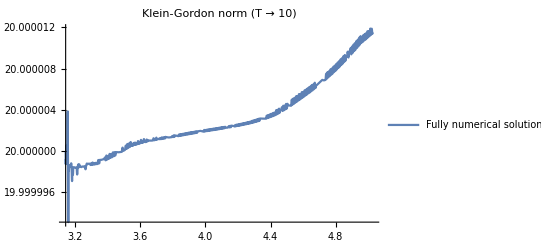

```mathematica
Plot[Evaluate[
kgNormFullNumFulling[a,b,T]/.{a->1,b->1,T->10}
],relevantdomain,
PlotLabel->"Klein-Gordon norm (T → 10)",
PlotLegends->{"Fully numerical solution"}]
```

#### Manipulable plot

(Since it takes a bit in computing every time we change T, we keep it unevaluated.)

```mathematica
(*Manipulate[
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T]}
],{t,Start,Start+WindowSize},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution"}],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]*)
```

### Adiabatic solutions

↪︎ They take a bit to plot.

#### Computation

```mathematica
kgNormAdbFulling[0][a_,b_,T_]=KleinGordonNorm[vxAdbFulling[0][a,b,T][t]];kgNormAdbFulling[1][a_,b_,T_]=KleinGordonNorm[vxAdbFulling[1][a,b,T][t]];
kgNormAdbFulling[2][a_,b_,T_]=KleinGordonNorm[vxAdbFulling[2][a,b,T][t]];
```

#### Static plot for {a → 1, b → 1, T → 10} (1st and 2nd orders)

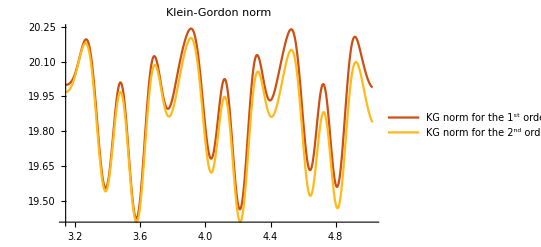

```mathematica
Plot[Evaluate[
{kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution"}]
```

#### Manipulable plot (1st and 2nd orders)

```mathematica
Manipulate[
Plot[{kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]},{t,Start,Start+WindowSize},
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution"}],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

#### All plots with the 0th order

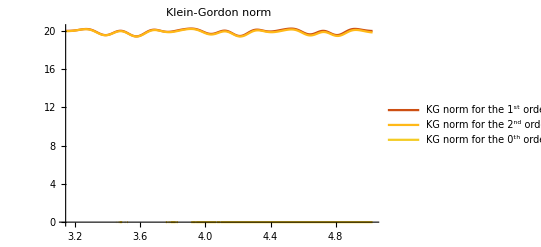

```mathematica
Plot[Evaluate[
{kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T],kgNormAdbFulling[0][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution","KG norm for the
0^th order solution"}]
```

```mathematica
Manipulate[
Plot[{kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T],kgNormAdbFulling[0][a,b,T]},{t,Start,Start+WindowSize},
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
0^th order solution","KG norm for the
1^st order solution","KG norm for the
2^nd order solution"}],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Semi-analytic solutions

#### Computation

```mathematica
kgNormAdbNumFulling[0][a_,b_,T_]=KleinGordonNorm[vxAdbNumFulling[0][a,b,T][t]];
kgNormAdbNumFulling[1][a_,b_,T_]=KleinGordonNorm[vxAdbNumFulling[1][a,b,T][t]];
kgNormAdbNumFulling[2][a_,b_,T_]=KleinGordonNorm[vxAdbNumFulling[2][a,b,T][t]];
```

Obs: The T-dependence is pointless unless we implement it in the vxAdbNumFulling[n][a,b,T][t] functions.

#### Static plot for {a → 1, b → 1, T → 10}

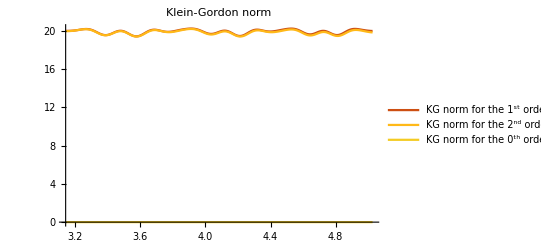

```mathematica
Plot[Evaluate[
{kgNormAdbNumFulling[1][a,b,T],kgNormAdbNumFulling[2][a,b,T],kgNormAdbNumFulling[0][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution","KG norm for the
0^th order solution"}]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[{kgNormAdbNumFulling[1][a,b,T],kgNormAdbNumFulling[2][a,b,T],kgNormAdbNumFulling[0][a,b,T]},{t,Start,Start+WindowSize},
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution","KG norm for the
0^th order solution"}],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

#### Comparison: analytical vs. semi-analytic norms ({a → 1, b → 1, T → 10})

```mathematica
stylecompare
```

{SolidData,Dashing[{Small,Small}],SolidData,Dashing[{Small,Small}],SolidData,Dashing[{Small,Small}]}

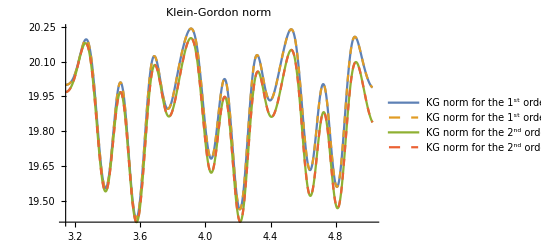

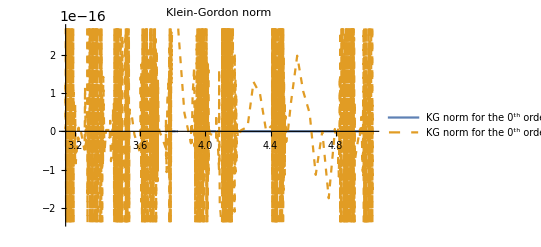

```mathematica
Plot[Evaluate[{
kgNormAdbFulling[1][a,b,T],kgNormAdbNumFulling[1][a,b,T],
kgNormAdbFulling[2][a,b,T],kgNormAdbNumFulling[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->stylecompare,
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution - Analytical","KG norm for the
1^st order solution - semi-analytic","KG norm for the
2^nd order solution - Analytical","KG norm for the
2^nd order solution - semi-analytic"}]
Plot[Evaluate[{
kgNormAdbFulling[0][a,b,T],
kgNormAdbNumFulling[0][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->stylecompare,
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
0^th order solution - Analytical","KG norm for the
0^th order solution - semi-analytic"}]
```

### Comparisons for {a → 1, b → 1, T → 10}

#### Static plot for t ∈ (t_i,t_f) ~ (π, 5)

```mathematica
ti
tf//N
```

π

5.02655

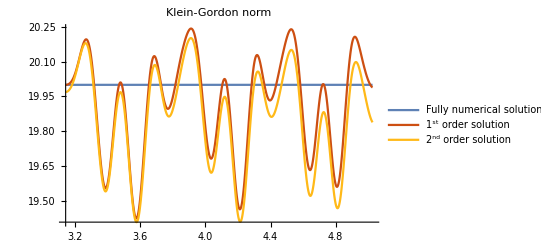

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

#### Static plot for t ∈ (t_i, 20)

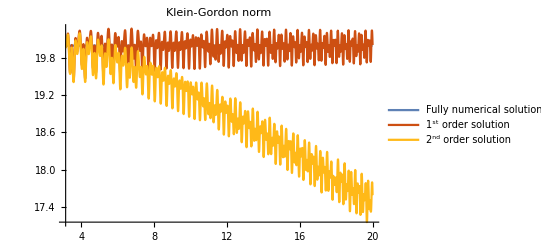

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}/.{a->1,b->1,T->10}
],{t,ti,20},
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

Here we see that the higher order solution (in this case, 2nd) makes a better job in keeping the Klein-Gordon norm relatively constant, while the 1st order solution doesn’t manage to do that.

#### Static plot for t ∈ (t_i, 60)

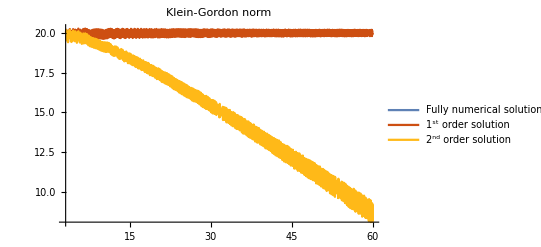

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}/.{a->1,b->1,T->10}
],{t,ti,60},
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

However, plotting an even larger domain, the  2nd order solution fails even worse.

#### Static plot for t ∈ (t_i, 100)

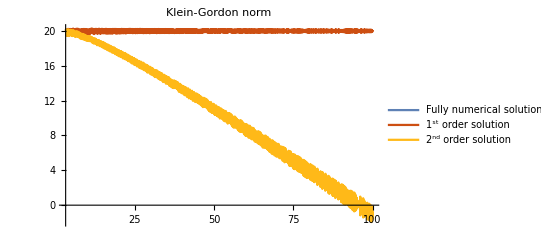

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}/.{a->1,b->1,T->10}
],{t,ti,100},
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

### Comparisons for {a → 1, b → 1, T → 50}

The situation improves if one goes deeper in the adiabatic regime (e.g. T → 50).

However, the norm oscillates significantly, and it still blows up eventually if we wait long enough.

#### Static plot for t ∈ (t_i,t_f) ~ (π, 5)

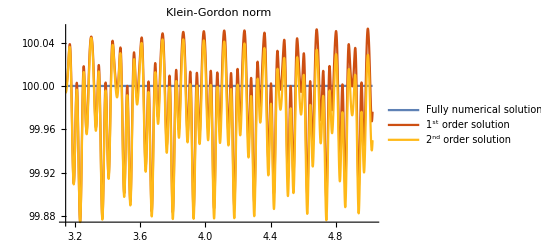

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}/.a->1/.b->1/.T->50
],relevantdomain,
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

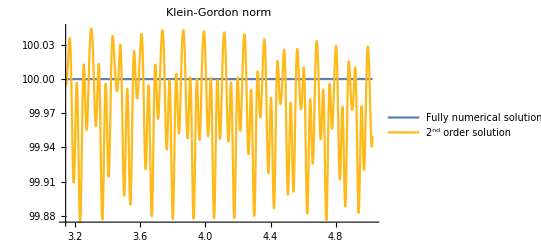

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[2][a,b,T]}/.T->50/.a->1/.b->1
],relevantdomain,
PlotStyle->{ColorData[97,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","2^nd order solution"}]
```

#### Static plot for t ∈ (t_i, 20)

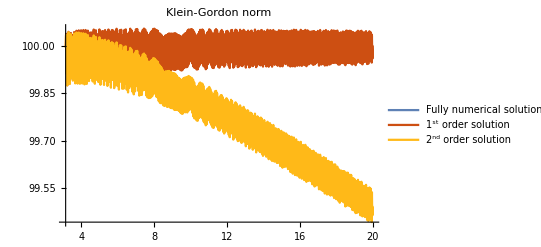

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}/.a->1/.b->1/.T->50
],{t,ti,20},
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

### Manipulable comparison

```mathematica
Manipulate[
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],kgNormAdbFulling[1][a,b,T],kgNormAdbFulling[2][a,b,T]}
],{t,Start,Start+WindowSize},
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Explanation of the zero norm of the 0th-order solution

#### Figuring it out

```mathematica
kgNormAdbFulling[0][a,b,T](*=KleinGordonNorm[vxAdbFulling[0][a,b,T][t]];*)/.{a->1,b->1}/.t->ti
kgNormAdbFulling[0][a,b,T](*=KleinGordonNorm[vxAdbFulling[0][a,b,T][t]];*)/.{a->1,b->1}/.t->5/.T->10//N
```

0

0.+0. ⅈ

```mathematica
vxAdbFulling[0][a,b,T][t]/.{a->1,b->1}//Simplify
vxAdbFulling[0][a,b,T][t]/.{a->1,b->1}/.t->ti
vxAdbFulling[0][a,b,T][t]/.{a->1,b->1}/.t->ti//N
vxAdbFulling[0][a,b,T][t]/.{a->1,b->1}/.t->5/.T->10//N
```

{0,(ⅇ^(-2/3 ⅈ (π^(3/2)-t^(3/2)) T) (1+ⅇ^(4/3 ⅈ (π^(3/2)-t^(3/2)) T)) Cos[t])/(2 t^(1/4)),(ⅇ^(-2/3 ⅈ (π^(3/2)-t^(3/2)) T) (1+ⅇ^(4/3 ⅈ (π^(3/2)-t^(3/2)) T)) Sin[t])/(2 t^(1/4))}

{0,-1/π^(1/4),0}

{0.,-0.751126,0.}

{0.,0.182007+0. ⅈ,-0.615277+0. ⅈ}

```mathematica
{x[1][a,b,T][t],x[2][a,b,T][t],x[3][a,b,T][t]}/.solFullNumFulling/.{a->1,b->1}/.T->10/.t->ti
{x[1][a,b,T][t],x[2][a,b,T][t],x[3][a,b,T][t]}/.solFullNumFulling/.{a->1,b->1}/.T->10/.t->5
```

{0.+0. ⅈ,-0.751126+0. ⅈ,0.+0. ⅈ}

{0.+0. ⅈ,0.128349-0.0467855 ⅈ,-0.654327+0.0479682 ⅈ}

```mathematica
kgNormFullNumFulling[a,b,T]/.{a->1,b->1}/.t->ti/.T->10
kgNormAdbFulling[0][a,b,T]/.{a->1,b->1}/.t->ti/.T->10//N
```

20.+0. ⅈ

0.

```mathematica
kgNormFullNumFulling[a,b,T]/.{a->1,b->1}/.t->5/.T->10
kgNormAdbFulling[0][a,b,T]/.{a->1,b->1}/.t->5/.T->10//N
```

20.+0. ⅈ

0.+0. ⅈ

```mathematica
vxAdbFulling[0][a,b,T]'[t]/.{a->1,b->1}/.t->ti
vxAdbFulling[0][a,b,T]'[t]/.{a->1,b->1}/.t->ti//N
{x[1][a,b,T]'[t],x[2][a,b,T]'[t],x[3][a,b,T]'[t]}/.solFullNumFulling/.{a->1,b->1}/.T->10/.t->ti
```

{0,1/(4 π^(5/4)),-1/π^(1/4)}

{0.,0.0597727,-0.751126}

{0.+0. ⅈ,0.-13.3134 ⅈ,6.61744×10^-24+1.21169×10^-27 ⅈ}

```mathematica
vxAdbFulling[0][a,b,T][t]/.{a->1,b->1}/.t->5/.T->10
vxAdbFulling[0][a,b,T][t]/.{a->1,b->1}/.t->5/.T->10//N
{x[1][a,b,T][t],x[2][a,b,T][t],x[3][a,b,T][t]}/.solFullNumFulling/.{a->1,b->1}/.T->10/.t->5
```

{0,(ⅇ^(-10 ⅈ ((10 √5)/3-(2 π^(3/2))/3)) Cos[5])/(2 5^(1/4))+(ⅇ^(10 ⅈ ((10 √5)/3-(2 π^(3/2))/3)) Cos[5])/(2 5^(1/4)),(ⅇ^(-10 ⅈ ((10 √5)/3-(2 π^(3/2))/3)) Sin[5])/(2 5^(1/4))+(ⅇ^(10 ⅈ ((10 √5)/3-(2 π^(3/2))/3)) Sin[5])/(2 5^(1/4))}

{0.,0.182007+0. ⅈ,-0.615277+0. ⅈ}

{0.+0. ⅈ,0.128349-0.0467855 ⅈ,-0.654327+0.0479682 ⅈ}

#### Explanation

Conclusion:

Even though the 0th-order adiabatic expansion is a good approximation to the exact solution, it cannot incorporate the 1st-order initial conditions in the derivative (recall they are proportional to T !), and hence it is not a good approximation to the exact derivative.

And, since the Klein-Gordon norm incorporates information about solution and derivative, the 0th-order KG norm is very bad.

And, precisely, since at 0th-order the initial conditions for the derivative are zero (i.e. not imaginary), and at the initial time the exponent in the complex exponential is canceled out by the initial phase, the 0th-order solution starts real and its KG norm is exactly zero.

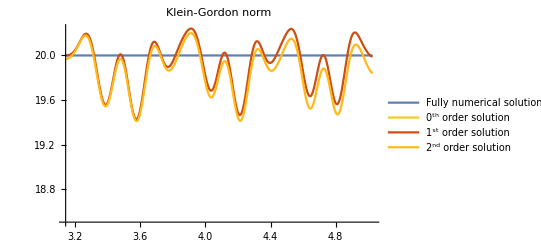

```mathematica
Plot[Evaluate[{
kgNormFullNumFulling[a,b,T],
kgNormAdbFulling[0][a,b,T],
kgNormAdbFulling[1][a,b,T],
kgNormAdbFulling[2][a,b,T]
}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->{ColorData[97,1],ColorData[35,3],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

### Normalized plots (for {a → 1, b → 1, T → 10})

#### Initial norms

```mathematica
kgNormFullNumFullingti[a_,b_,T_]=kgNormFullNumFulling[a,b,T]/.t->ti;
```

```mathematica
kgNormAdbFullingti[0][a_,b_,T_]=kgNormAdbFulling[1][a,b,T]/.t->ti;
kgNormAdbFullingti[1][a_,b_,T_]=kgNormAdbFulling[1][a,b,T]/.t->ti;
kgNormAdbFullingti[2][a_,b_,T_]=kgNormAdbFulling[2][a,b,T]/.t->ti;
```

```mathematica
kgNormAdbNumFullingti[0][a_,b_,T_]=kgNormAdbNumFulling[0][a,b,T]/.t->ti;
kgNormAdbNumFullingti[1][a_,b_,T_]=kgNormAdbNumFulling[1][a,b,T]/.t->ti;
kgNormAdbNumFullingti[2][a_,b_,T_]=kgNormAdbNumFulling[2][a,b,T]/.t->ti;
```

#### Normalized norms

```mathematica
kgNormFullNumFullingNormalized[a_,b_,T_]=kgNormFullNumFulling[a,b,T]/kgNormFullNumFullingti[a,b,T];
```

```mathematica
kgNormAdbFullingNormalized[0][a_,b_,T_]=Re[kgNormAdbFulling[0][a,b,T](*/kgNormAdbFullingti[0][a,b,T]*)];
```

(Since it is zero, we don’t want to divide by the 0th-order KG norm, and we keep the original one;
 Also, it seems to be incorporating some tiny imaginary error, so we take its real part to plot it correctly.)

```mathematica
kgNormAdbFullingNormalized[1][a_,b_,T_]=kgNormAdbFulling[1][a,b,T]/kgNormAdbFullingti[1][a,b,T];
kgNormAdbFullingNormalized[2][a_,b_,T_]=kgNormAdbFulling[2][a,b,T]/kgNormAdbFullingti[2][a,b,T];
```

#### Numerical

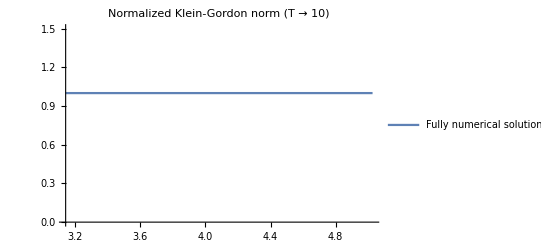

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0,1.5},
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"Fully numerical solution"}]
```

#### Adiabatic (0th order)

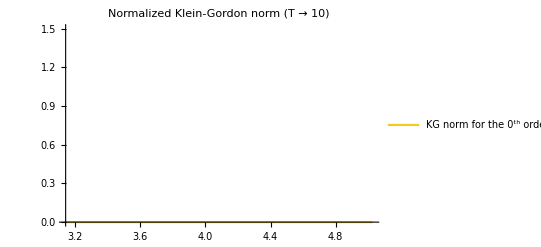

```mathematica
Plot[Evaluate[{
kgNormAdbFullingNormalized[0][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->ColorData[35,3],
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"KG norm for the
0^th order solution"}]
```

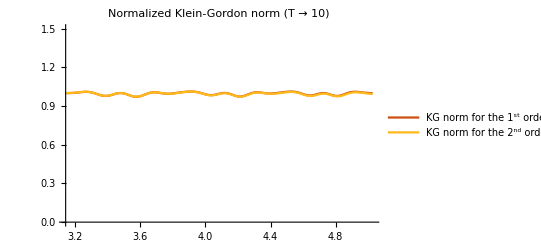

```mathematica
Plot[Evaluate[{
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution"}]
```

#### Semi-analytic (1st & 2nd orders)

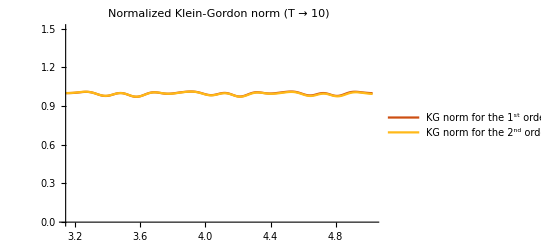

```mathematica
Plot[Evaluate[{
kgNormAdbNumFulling[1][a,b,T]/kgNormAdbNumFullingti[1][a,b,T],kgNormAdbNumFulling[2][a,b,T]/kgNormAdbNumFullingti[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution"}]
```

#### Comparison (numerical vs. 1st vs. 2nd-order adiabatic)

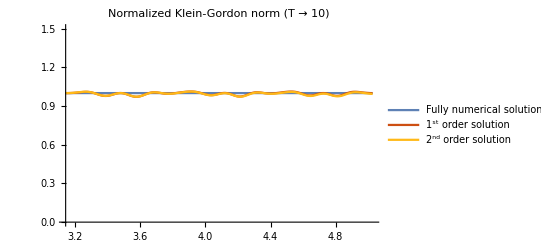

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->{ColorData[97,1],ColorData[35,1],ColorData[35,2]},
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

#### Comparison (adiabatic analytical vs. semi-analytic)

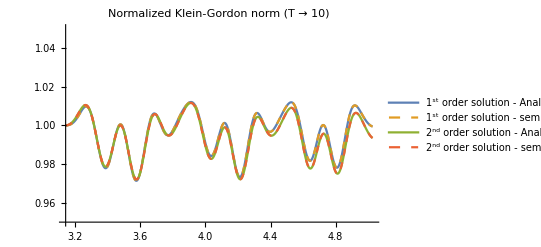

```mathematica
Plot[Evaluate[{
kgNormAdbFullingNormalized[1][a,b,T],kgNormAdbNumFulling[1][a,b,T]/kgNormAdbNumFullingti[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T],kgNormAdbNumFulling[2][a,b,T]/kgNormAdbNumFullingti[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0.95,1.05},
PlotStyle->stylecompare,
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"1^st order solution - Analytical","1^st order solution - semi-analytic","2^nd order solution - Analytical","2^nd order solution - semi-analytic"}]
```

Amazing.

#### KG plots for the report

```mathematica
colorNum=ColorData[97,1]
color0th={Dashed,ColorData[97,3]}
color1st=ColorData[35,2]
color2nd=ColorData[35,1]
```

RGBColor[0.368417, 0.506779, 0.709798]

{Dashing[{Small,Small}],RGBColor[0.560181, 0.691569, 0.194885]}

RGBColor[1., 0.7254901960784313, 0.09411764705882353]

RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765]

```mathematica
range1={-0.045,1+1/3};
rangeZoomed={0.7(*-0.045*0.1*3*),1.1};
latetime=10.97;
latetimedomain={t,ti,latetime+8/10};
```

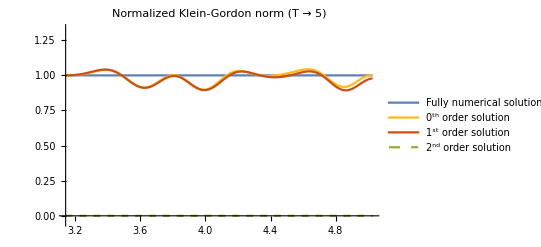

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T],
kgNormAdbFullingNormalized[0][a,b,T]}/.{a->1,b->1,T->5}
],relevantdomain,PlotRange->range1,
PlotStyle->{colorNum,color1st,color2nd,color0th},
PlotLabel->"Normalized Klein-Gordon norm (T → 5)",
PlotLegends->{"Fully numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

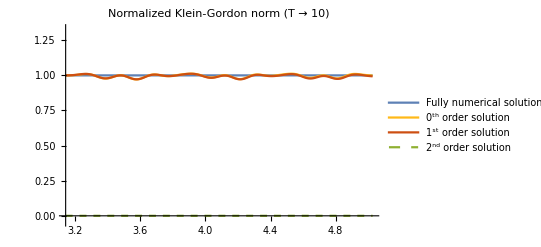

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T],
kgNormAdbFullingNormalized[0][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->range1,
PlotStyle->{colorNum,color1st,color2nd,color0th},
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"Fully numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

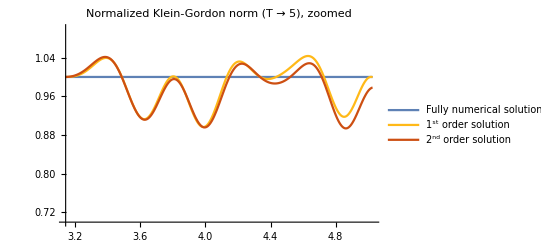

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T]}/.{a->1,b->1,T->5}
],relevantdomain,PlotRange->rangeZoomed,
PlotStyle->{colorNum,color1st,color2nd},
PlotLabel->"Normalized Klein-Gordon norm (T → 5), zoomed",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

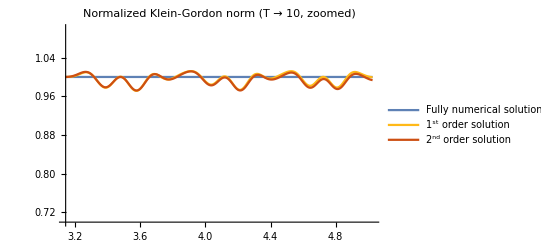

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->rangeZoomed,
PlotStyle->{colorNum,color1st,color2nd},
PlotLabel->"Normalized Klein-Gordon norm (T → 10, zoomed)",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

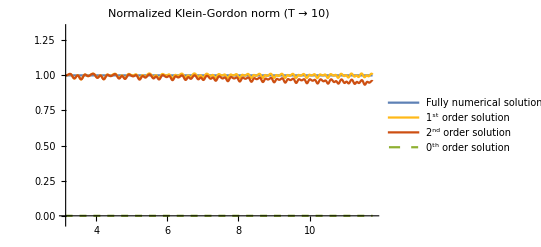

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T],
kgNormAdbFullingNormalized[0][a,b,T]}/.{a->1,b->1,T->10}
],latetimedomain,PlotRange->range1,
PlotStyle->{colorNum,color1st,color2nd,color0th},
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution","0^th order solution"}]
```

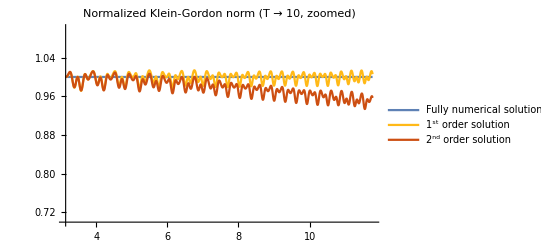

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T]}/.{a->1,b->1,T->10}
],latetimedomain,PlotRange->rangeZoomed,
PlotStyle->{colorNum,color1st,color2nd},
PlotLabel->"Normalized Klein-Gordon norm (T → 10, zoomed)",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

#### Both T ’s together? (Nope)

```mathematica
styleT10={colorNum,color1st,color2nd,color0th};
styleT5={{Dashed,colorNum},{Dashed,color1st},{Dashed,color2nd},{Dashed,color0th}};
```

```mathematica
Flatten[{styleT10,styleT5},1]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],{Dashing[{Small,Small}],RGBColor[0.560181, 0.691569, 0.194885]},{Dashing[{Small,Small}],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[{Small,Small}],RGBColor[1., 0.7254901960784313, 0.09411764705882353]},{Dashing[{Small,Small}],RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765]},{Dashing[{Small,Small}],{Dashing[{Small,Small}],RGBColor[0.560181, 0.691569, 0.194885]}}}

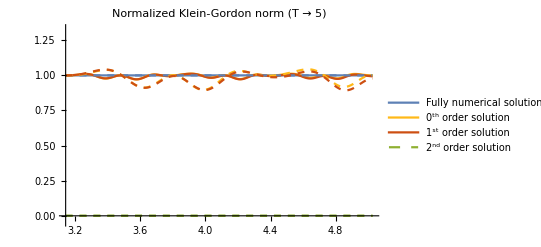

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T]/.T->10,
kgNormAdbFullingNormalized[1][a,b,T]/.T->10,
kgNormAdbFullingNormalized[2][a,b,T]/.T->10,
kgNormAdbFullingNormalized[0][a,b,T]/.T->10,
kgNormFullNumFullingNormalized[a,b,T]/.T->5,
kgNormAdbFullingNormalized[1][a,b,T]/.T->5,
kgNormAdbFullingNormalized[2][a,b,T]/.T->5,
kgNormAdbFullingNormalized[0][a,b,T]/.T->5
}/.{a->1,b->1}
],relevantdomain,PlotRange->range1,
PlotStyle->Flatten[{styleT10,styleT5},1],
PlotLabel->"Normalized Klein-Gordon norm (T → 5)",
PlotLegends->{"Fully numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

```mathematica
Plot[Evaluate[{
kgNormFullNumFullingNormalized[a,b,T],
kgNormAdbFullingNormalized[1][a,b,T],
kgNormAdbFullingNormalized[2][a,b,T]}/.{a->1,b->1,T->5}
],relevantdomain,PlotRange->rangeZoomed,
PlotStyle->{colorNum,color1st,color2nd},
PlotLabel->"Normalized Klein-Gordon norm (T → 5), zoomed",
PlotLegends->{"Fully numerical solution","1^st order solution","2^nd order solution"}]
```

-Graphics-

## Extra: semi-analytic (coefficients) results

I keep it just to triple check that the final semi-analytic solution is what I had achieved before analytically.

## Semi-analytic adiabatic solution (T-manipulative): Extras

### First order tests (not needed for the rest of the notebook): Analytical vs. semi-analytic primitives in HOvaP

#### Integrals in the higher order parallel (∥) recurrence relation (HOVaP) - Analytical version

```mathematica
PrimitiveinHOvaPAnalyt[n_,k_][a_,b_,T_][t_]:=∫_ti^t mUinv[a,b][t1].(-1/2(p[k][a,b][t1])^(-1/2)mP[k][a,b][t1].va[n-1,k][a,b,T]''[t1]+1/4(p[k][a,b][t1])^(-3/2)p[k][a,b]'[t1]mP[k][a,b][t1].va[n-1,k][a,b,T]'[t1]+1/2(p[k][a,b][t1])^(1/2)((p[k][a,b]''[t1])/(4p[k][a,b][t1]^2)-(5p[k][a,b]'[t1]^2)/(16p[k][a,b][t1]^3))mP[k][a,b][t1].va[n-1,k][a,b,T][t1]-mP[k][a,b][t1].vaN[n,k][a,b,T]'[t1])ⅆt1
```

#### Integrals in the higher order parallel (∥) recurrence relation (HOVaP) - semi-analytic version

Rec:	NPrimitive nomenclature:
	ParametricNPrimitive[{f[param ][t],ti},F,{t,tmin,tmax},{param }]

Semi-analytic function (through NPrimitiveValue):

Particularization to all-1s ζ-constants:

```mathematica
NPrimitiveinHOvaPAll1s[n_,k_]:=Array[ParametricNPrimitiveValue[{(IntegrandinHOvaP[n,k][a,b,T][t]/.Subscript[ζ, _,_,_]->1)[[#]],ti},intN,{t,tmin,tmax},{a,b,T}]&,dim]
```

Particularization to Fulling’s i.c.’s ζ-constants:

```mathematica
NPrimitiveinHOvaPFulling[n_,k_]:=Array[ParametricNPrimitiveValue[{(IntegrandinHOvaP[n,k][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T])[[#]],ti},intN,{t,tmin,tmax},{a,b,T}]&,dim]
```

#### Check: Correct evaluation of the integrand in HOvaP

```mathematica
IntegrandinHOvaP[n,k][c,d,S][s]
```

{{1,0,0},{0,Cos[d (π-s)],-Sin[d (π-s)]},{0,Sin[d (π-s)],Cos[d (π-s)]}}.(-mP[k][c,d][s].vaN[n,k][c,d,S]'[s]+(mP[k][c,d][s].(vaN[-1+n,k][c,d,S]'[s]+vaP[-1+n,k][c,d,S]'[s]) p[k][c,d]'[s])/(4 (p[k][c,d][s])^(3/2))-(mP[k][c,d][s].(vaN[-1+n,k][c,d,S]''[s]+vaP[-1+n,k][c,d,S]''[s]))/(2 √(p[k][c,d][s]))+1/2 mP[k][c,d][s].(vaN[-1+n,k][c,d,S][s]+vaP[-1+n,k][c,d,S][s]) (-(5 (p[k][c,d]'[s])^2)/(16 (p[k][c,d][s])^3)+(p[k][c,d]''[s])/(4 (p[k][c,d][s])^2)) √(p[k][c,d][s]))

#### Check: Analytical vs. semi-analytic functions for all-1s ζ-constants

Analytical integrand:

```mathematica
For[k=1,k<=nk,k++,{
integrandinHOvaPAll1s[1,k][a_,b_,T_][t_]=IntegrandinHOvaP[1,k][a,b,T][t]/.Subscript[ζ, _,_,_]->1//Simplify
}]
ClearAll[k]
```

```mathematica
Array[integrandinHOvaPAll1s[1,#][a,b,T][t]&,nk]
```

{{-5/(32 √(a t^5)),-((-5+5 t+16 b^2 t^2+48 b^2 t^3) Cos[b π])/(32 (-1+t) t^2 √(a t)),-((-5+5 t+16 b^2 t^2+48 b^2 t^3) Sin[b π])/(32 (-1+t) t^2 √(a t))},{0,-(b^2 (3+t) Sin[b π])/(2 √a (-1+t)),(b^2 (3+t) Cos[b π])/(2 √a (-1+t))}}

Plot: Analytical integrand

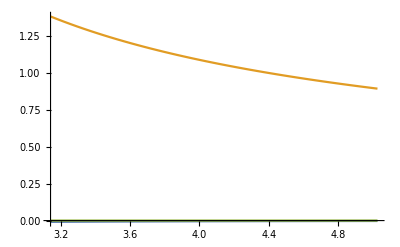
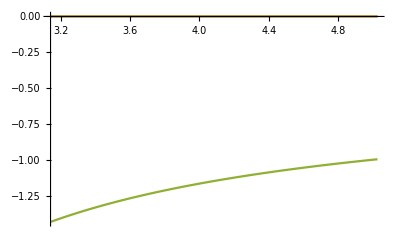

```mathematica
Array[
Plot[Evaluate[{
integrandinHOvaPAll1s[1,#][a,b,T][t]
}/.{a->1,b->1,T->1}],
relevantdomain]&,
nk]
```

Analytical primitive:

```mathematica
For[k=1,k<=nk,k++,{
primitiveinHOvaPAnalytAll1s[1,k][a_,b_,T_][t_]=PrimitiveinHOvaPAnalyt[1,k][a,b,T][t]/.Subscript[ζ, _,_,_]->1
}]
ClearAll[k]
```

```mathematica
Array[primitiveinHOvaPAnalytAll1s[1,#][a,b,T][t]&,nk]
```

{{-(5 (1/π^(3/2)-1/t^(3/2)))/(48 √a),-((5/π^(3/2)-5/t^(3/2)-48 b^2 (3 √π-3 √t-4 ArcCoth[√π])-192 b^2 ArcCoth[√t]) Cos[b π])/(48 √a),-((5/π^(3/2)-5/t^(3/2)-48 b^2 (3 √π-3 √t-4 ArcCoth[√π])-192 b^2 ArcCoth[√t]) Sin[b π])/(48 √a)},{0,(b^2 (π-t+4 Log[-1+π]-4 Log[-1+t]) Sin[b π])/(2 √a),(b^2 Cos[b π] (-π+t-4 Log[-1+π]+4 Log[-1+t]))/(2 √a)}}

Semi-analytic primitive:

```mathematica
For[k=1,k<=nk,k++,{
primitiveinHOvaPNumAll1s[1,k]=NPrimitiveinHOvaPAll1s[1,k]
}]
ClearAll[k]
```

```mathematica
primitiveinHOvaPNumAll1s[1,1]
```

{ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>]}

Plots: Analytical vs. semi-analytic primitives

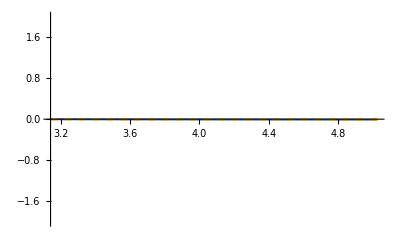
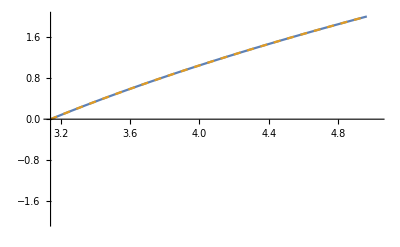
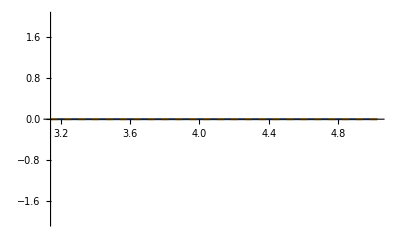
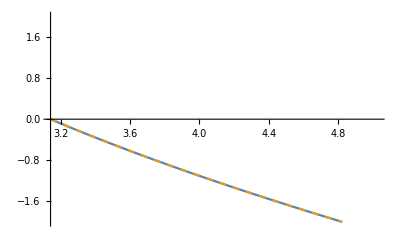
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Array[Plot[Evaluate[{
primitiveinHOvaPAnalytAll1s[1,#1][a,b,T][t][[#2]],primitiveinHOvaPNumAll1s[1,#1][[#2]][a,b,T][t]
}/.{a->1,b->1,T->1}],
relevantdomain,PlotRange->{-2,2},PlotStyle->stylecompare]&,{nk,dim}]
```

#### Check: Analytical vs. semi-analytic functions for Fulling’s i.c.’s

For Fulling’s i.c.’s:

Analytical integrand:

```mathematica
For[k=1,k<=nk,k++,{
integrandinHOvaPFulling[1,k][a_,b_,T_][t_]=IntegrandinHOvaP[1,k][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T]//Simplify
}]
ClearAll[k]
```

```mathematica
Array[integrandinHOvaPFulling[1,#][a,b,T][t]&,nk]
```

{{0,-((-5+5 t+16 b^2 t^2+48 b^2 t^3) Cos[b π])/(64 (-1+t) t^2 √(a t)),-((-5+5 t+16 b^2 t^2+48 b^2 t^3) Sin[b π])/(64 (-1+t) t^2 √(a t))},{0,0,0}}

Plot: Analytical integrand

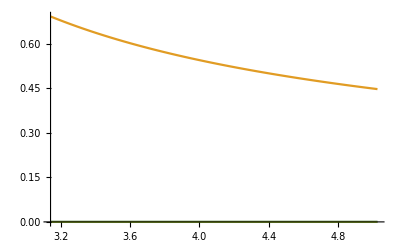
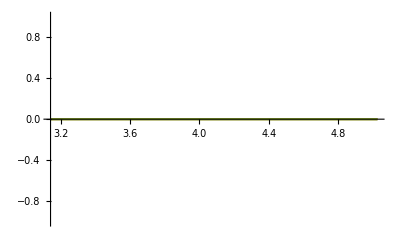

```mathematica
Array[
Plot[Evaluate[{
integrandinHOvaPFulling[1,#][a,b,T][t]
}/.{a->1,b->1,T->1}],
relevantdomain]&,
nk]
```

Analytical primitive:

```mathematica
For[k=1,k<=nk,k++,{
primitiveinHOvaPAnalytFulling[1,k][a_,b_,T_][t_]=PrimitiveinHOvaPAnalyt[1,k][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T]
}]
ClearAll[k]
```

```mathematica
Array[primitiveinHOvaPAnalytFulling[1,#][a,b,T][t]&,nk]
```

{{0,-((5/π^(3/2)-5/t^(3/2)-48 b^2 (3 √π-3 √t-4 ArcCoth[√π])-192 b^2 ArcCoth[√t]) Cos[b π])/(96 √a),-((5/π^(3/2)-5/t^(3/2)-48 b^2 (3 √π-3 √t-4 ArcCoth[√π])-192 b^2 ArcCoth[√t]) Sin[b π])/(96 √a)},{0,0,0}}

Semi-analytic primitive:

```mathematica
For[k=1,k<=nk,k++,{
primitiveinHOvaPNumFulling[1,k]=NPrimitiveinHOvaPFulling[1,k]
}]
ClearAll[k]
```

```mathematica
primitiveinHOvaPNumFulling[1,1]
```

{ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>]}

Plots: Analytical vs. semi-analytic primitives

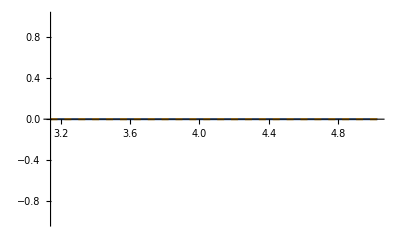
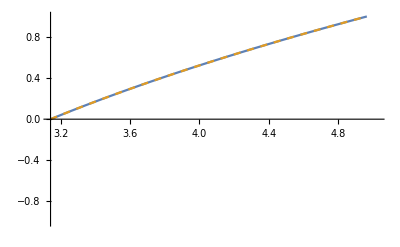
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Array[Plot[Evaluate[{
primitiveinHOvaPAnalytFulling[1,#1][a,b,T][t][[#2]],primitiveinHOvaPNumFulling[1,#1][[#2]][a,b,T][t]
}/.{a->1,b->1,T->1}],
relevantdomain,PlotRange->{-1,1},PlotStyle->stylecompare]&,{nk,dim}]
```

### Checks and explanations on semi-analytic HOvaP’s

#### Semi-analytic version of HOvaP (for all ζ i.c.’s = 1)

```mathematica
NHOvaPAll1s[1,1][c,d,S][s]
```

{1+ParametricFunction[<>][c,d,S][s],Cos[d π] Cos[d (π-s)]+Sin[d π] Sin[d (π-s)]+Sin[d (π-s)] ParametricFunction[<>][c,d,S][s]+Cos[d (π-s)] ParametricFunction[<>][c,d,S][s],Cos[d (π-s)] Sin[d π]-Cos[d π] Sin[d (π-s)]+Cos[d (π-s)] ParametricFunction[<>][c,d,S][s]-Sin[d (π-s)] ParametricFunction[<>][c,d,S][s]}

```mathematica
NHOvaPAll1s[1,1][a,b,T][t][[1]]
```

1+ParametricFunction[<>][a,b,T][t]

```mathematica
NHOvaPAll1s[1,1][a,b,T][t][[1]]/.{a->1,b->1,T->10}
```

1+InterpolatingFunction[…][t]

```mathematica
NHOvaPAll1s[1,1][a,b,T][t][[1]]/.{a->1,b->1,T->10}/.t->ti
```

1.

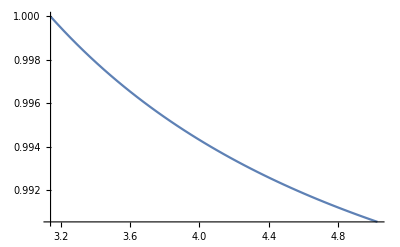

```mathematica
Plot[Evaluate[NHOvaPAll1s[1,1][a,b,T][t][[1]]/.{a->1,b->1,T->10}],relevantdomain]
```

Obs:	Note the [t] after the NPrimitiveValue[…], i.e.  NPrimitiveValue[…][t].
	This returns not the interpolating function, but the interpolating function evaluated at [t] instead.
	Although usually not wanted (complicates handling/plotting the interpolating function), but it is the way to use it within analytical expressions.
	The handicap is that Mathematica will need to numerically solve the interpolating function every time we call it or plot it. (Fortunately, that is usually quite fast, actually faster than somehow complicated analytical expressions.)

Here we also have to add the parameters [a,b,T] between ParametricNPrimitiveValue and [t] since it is parametric. Also, it is important to define the function itself in parameters with different names (here, e.g. [c,d,S]) so the function works properly when evaluating. The mnemotechnic would be
	...[c_,d_,S_][t_]:=...NPrimitiveValue[{...,{a,b,T}][c,d,S][t]...

We define the analytical expressions so it doesn’t need to compute it every time we call it.

```mathematica
For[k=1,k<=nk,k++,
HOvaPAnalytAll1s[1,k][a_,b_,T_][t_]=HOvaP[1,k][a,b,T][t]/.Subscript[ζ, _,_,_]->1
]
ClearAll[k];
```

{1+(5 (-1/π^(3/2)+1/t^(3/2)))/(48 √a),1/48 (48-144 b^2 √(t/a)+5/(√(a t^3))+(-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π]))/(√a π^(3/2))+(192 b^2 ArcCoth[√t])/(√a)) Cos[b t],1/48 (48-144 b^2 √(t/a)+5/(√(a t^3))+(-5+48 b^2 (3 π^2-4 π^(3/2) ArcCoth[√π]))/(√a π^(3/2))+(192 b^2 ArcCoth[√t])/(√a)) Sin[b t]}

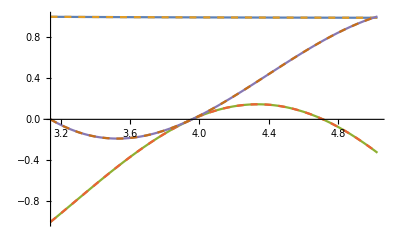

```mathematica
HOvaPAnalytAll1s[1,1][a,b,T][t]//Simplify
Plot[Evaluate[{
HOvaPAnalytAll1s[1,1][a,b,T][t][[1]],NHOvaPAll1s[1,1][a,b,T][t][[1]],
HOvaPAnalytAll1s[1,1][a,b,T][t][[2]],NHOvaPAll1s[1,1][a,b,T][t][[2]],
HOvaPAnalytAll1s[1,1][a,b,T][t][[3]],NHOvaPAll1s[1,1][a,b,T][t][[3]]
}/.{a->1,b->1,T->10}],relevantdomain,PlotStyle->stylecompare]
```

Wonderful.

#### Semi-analytic version of HOvaP (for my own old i.c.’s)

```mathematica
NHOvaPOwn[1,1][c,d,T][s]
NHOvaPOwn[1,2][c,d,T][s]
```

{ParametricFunction[<>][c,d,T][s],Cos[d (π-s)] ParametricFunction[<>][c,d,T][s]+Sin[d (π-s)] ParametricFunction[<>][c,d,T][s],-Sin[d (π-s)] ParametricFunction[<>][c,d,T][s]+Cos[d (π-s)] ParametricFunction[<>][c,d,T][s]}

{ParametricFunction[<>][c,d,T][s],-((-2/(-1+π^(1/4)-√π+π^(3/4))-(ⅈ T ((1+3 π)/π^(3/4)-(2 ⅈ (-T+2 √π T-2 π^(3/2) T+π^2 T))/π^(1/4)))/(-1+π)^2) Cos[d (π-s)] Sin[d π])+(-2/(-1+π^(1/4)-√π+π^(3/4))-(ⅈ T ((1+3 π)/π^(3/4)-(2 ⅈ (-T+2 √π T-2 π^(3/2) T+π^2 T))/π^(1/4)))/(-1+π)^2) Cos[d π] Sin[d (π-s)]+Sin[d (π-s)] ParametricFunction[<>][c,d,T][s]+Cos[d (π-s)] ParametricFunction[<>][c,d,T][s],(-2/(-1+π^(1/4)-√π+π^(3/4))-(ⅈ T ((1+3 π)/π^(3/4)-(2 ⅈ (-T+2 √π T-2 π^(3/2) T+π^2 T))/π^(1/4)))/(-1+π)^2) Cos[d π] Cos[d (π-s)]+(-2/(-1+π^(1/4)-√π+π^(3/4))-(ⅈ T ((1+3 π)/π^(3/4)-(2 ⅈ (-T+2 √π T-2 π^(3/2) T+π^2 T))/π^(1/4)))/(-1+π)^2) Sin[d π] Sin[d (π-s)]+Cos[d (π-s)] ParametricFunction[<>][c,d,T][s]-Sin[d (π-s)] ParametricFunction[<>][c,d,T][s]}

We define the analytical expressions so it doesn’t need to compute it every time we call it.

```mathematica
For[k=1,k<=nk,k++,
HOvaPAnalytOwn[1,k][a_,b_,T_][t_]=HOvaP[1,k][a,b,T][t]/.j->ⅈ//.constsOwn[T]
]
ClearAll[k];
```

{0,-((-5 t^(3/2)+144 b^2 π^2 t^(3/2)+π^(3/2) (5-48 b^2 (3 t^2+4 t^(3/2) ArcCoth[√π]))+192 b^2 π^(3/2) t^(3/2) ArcCoth[√t]) Cos[b t])/(48 π^(3/2) √(a t^3)),-((-5 t^(3/2)+144 b^2 π^2 t^(3/2)+π^(3/2) (5-48 b^2 (3 t^2+4 t^(3/2) ArcCoth[√π]))+192 b^2 π^(3/2) t^(3/2) ArcCoth[√t]) Sin[b t])/(48 π^(3/2) √(a t^3))}

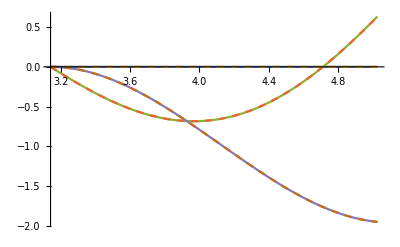

```mathematica
HOvaPAnalytOwn[1,1][a,b,T][t]
Plot[Evaluate[{
HOvaPAnalytOwn[1,1][a,b,T][t][[1]],NHOvaPOwn[1,1][a,b,T][t][[1]],
HOvaPAnalytOwn[1,1][a,b,T][t][[2]],NHOvaPOwn[1,1][a,b,T][t][[2]],
HOvaPAnalytOwn[1,1][a,b,T][t][[3]],NHOvaPOwn[1,1][a,b,T][t][[3]]
}/.{a->1,b->1,T->10}],relevantdomain,PlotStyle->stylecompare]
```

#### Semi-analytic version of HOvaP (for Fulling’s i.c.’s)

Obs:	Note the [t] after the NPrimitiveValue[…], i.e.  NPrimitiveValue[…][t].
	This returns not the interpolating function, but the interpolating function evaluated at [t] instead.
	Although usually not wanted (complicates handling/plotting the interpolating function), but it is the way to use it within analytical expressions.
	The handicap is that Mathematica will need to numerically solve the interpolating function every time we call it or plot it. (Fortunately, that is usually quite fast, actually faster than somehow complicated analytical expressions.)

```mathematica
NHOvaPFulling[1,1][c,d,S][s]
```

{ParametricFunction[<>][c,d,S][s],((1/π^(3/2)+4 ⅈ c^(1/4) S) Cos[d π] Cos[d (π-s)])/(8 √c)+((1/π^(3/2)+4 ⅈ c^(1/4) S) Sin[d π] Sin[d (π-s)])/(8 √c)+Sin[d (π-s)] ParametricFunction[<>][c,d,S][s]+Cos[d (π-s)] ParametricFunction[<>][c,d,S][s],((1/π^(3/2)+4 ⅈ c^(1/4) S) Cos[d (π-s)] Sin[d π])/(8 √c)-((1/π^(3/2)+4 ⅈ c^(1/4) S) Cos[d π] Sin[d (π-s)])/(8 √c)+Cos[d (π-s)] ParametricFunction[<>][c,d,S][s]-Sin[d (π-s)] ParametricFunction[<>][c,d,S][s]}

We define the analytical expressions so it doesn’t need to compute it every time we call it.

```mathematica
For[k=1,k<=nk,k++,
HOvaPAnalytFulling[1,k][a_,b_,T_][t_]=HOvaP[1,k][a,b,T][t]/.j->ⅈ//.constsFulling[a,b,T]
]
ClearAll[k];
```

```mathematica
HOvaPAnalytFulling[1,1][a,b,T][t]
Plot[Evaluate[{
HOvaPAnalytFulling[1,1][a,b,T][t][[1]],NHOvaPFulling[1,1][a,b,T][t][[1]],
HOvaPAnalytFulling[1,1][a,b,T][t][[2]],NHOvaPFulling[1,1][a,b,T][t][[2]],
HOvaPAnalytFulling[1,1][a,b,T][t][[3]],NHOvaPFulling[1,1][a,b,T][t][[3]]}/.{a->1,b->1,T->10}],
relevantdomain,PlotStyle->stylecompare]
```

{0,1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5 t^(3/2)+144 b^2 π^2 t^(3/2)+π^(3/2) (5-48 b^2 (3 t^2+4 t^(3/2) ArcCoth[√π]))+192 b^2 π^(3/2) t^(3/2) ArcCoth[√t])/(2 π^(3/2) √(a t^3))) Cos[b t],1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5 t^(3/2)+144 b^2 π^2 t^(3/2)+π^(3/2) (5-48 b^2 (3 t^2+4 t^(3/2) ArcCoth[√π]))+192 b^2 π^(3/2) t^(3/2) ArcCoth[√t])/(2 π^(3/2) √(a t^3))) Sin[b t]}

-Graphics-

Here, the second and third entries doesn’t appear because Fulling’s i.c.’s include the imaginary unit and makes the result be complex. Taking the real part is not straightforward because there are several functions involved, but we can manage to get rid of the imaginary parts by //Expand//Re//Simplify. (Note that it might be needed to specify assumptions if there are constants involved; typically, that they are real, and perhaps positive. For example, here we need T ∈ ℝ.) For example, for the second entry:

```mathematica
NHOvaPFulling[1,1][a,b,T][t][[2]]/.{a->1,b->1,T->10}
```

1/8 (40 ⅈ+1/π^(3/2)) Cos[t]+Sin[t] InterpolatingFunction[…][t]-Cos[t] InterpolatingFunction[…][t]

```mathematica
NHOvaPFulling[1,1][a,b,T][t][[2]]/.{a->1,b->1,T->10}//Expand//Re//Simplify
```

Re[Sin[t] InterpolatingFunction[…][t]+1/8 Cos[t] (1/π^(3/2)-8 InterpolatingFunction[…][t])]

Then, we apply Simplify@Re@Expand@ to the plotted functions:

{0,1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5 t^(3/2)+144 b^2 π^2 t^(3/2)+π^(3/2) (5-48 b^2 (3 t^2+4 t^(3/2) ArcCoth[√π]))+192 b^2 π^(3/2) t^(3/2) ArcCoth[√t])/(2 π^(3/2) √(a t^3))) Cos[b t],1/48 ((6 (1/π^(3/2)+4 ⅈ a^(1/4) T))/(√a)+(-5 t^(3/2)+144 b^2 π^2 t^(3/2)+π^(3/2) (5-48 b^2 (3 t^2+4 t^(3/2) ArcCoth[√π]))+192 b^2 π^(3/2) t^(3/2) ArcCoth[√t])/(2 π^(3/2) √(a t^3))) Sin[b t]}

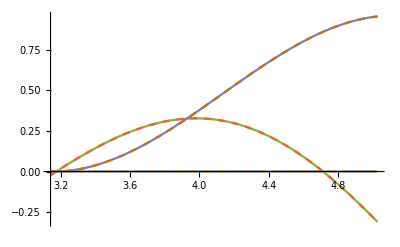

```mathematica
HOvaPAnalytFulling[1,1][a,b,T][t]
Plot[Evaluate[{
Simplify@Re@Expand@HOvaPAnalytFulling[1,1][a,b,T][t][[1]],Simplify@Re@Expand@NHOvaPFulling[1,1][a,b,T][t][[1]],
Simplify@Re@Expand@HOvaPAnalytFulling[1,1][a,b,T][t][[2]],Simplify@Re@Expand@NHOvaPFulling[1,1][a,b,T][t][[2]],
Simplify@Re@Expand@HOvaPAnalytFulling[1,1][a,b,T][t][[3]],Simplify@Re@Expand@NHOvaPFulling[1,1][a,b,T][t][[3]]}/.{a->1,b->1,T->10}],
relevantdomain,PlotStyle->stylecompare]
```

### Plots and prints of the semi-analytic coefficients

#### Prints of the parallel (∥) coefficients

All-orders parallel (∥) coefficients:

```mathematica
For[n=0,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
Print["vaPNumFulling[",n,",",k,"][a,b,T][t] = ",vaPNumFulling[n,k][a,b,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

vaPNumFulling[0,1][a,b,T][t] = (0
1/2 (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)])
1/2 (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))

vaPNumFulling[0,2][a,b,T][t] = (0
0
0)

vaPNumFulling[1,1][a,b,T][t] = (ParametricFunction[<>][a,b,T][t]
((1/π^(3/2)+4 ⅈ a^(1/4) T) Cos[b π] Cos[b (π-t)])/(8 √a)+((1/π^(3/2)+4 ⅈ a^(1/4) T) Sin[b π] Sin[b (π-t)])/(8 √a)+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]+Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]
((1/π^(3/2)+4 ⅈ a^(1/4) T) Cos[b (π-t)] Sin[b π])/(8 √a)-((1/π^(3/2)+4 ⅈ a^(1/4) T) Cos[b π] Sin[b (π-t)])/(8 √a)-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t])

vaPNumFulling[1,2][a,b,T][t] = (ParametricFunction[<>][a,b,T][t]
-(Cos[b (π-t)] Sin[b π] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+(Cos[b π] Sin[b (π-t)] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]
(Cos[b π] Cos[b (π-t)] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+(Sin[b π] Sin[b (π-t)] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t])

vaPNumFulling[2,1][a,b,T][t] = (ParametricFunction[<>][a,b,T][t]
Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]
Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t])

vaPNumFulling[2,2][a,b,T][t] = (ParametricFunction[<>][a,b,T][t]
Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]+Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]
-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t])

#### Plots of the parallel (∥) coefficients

First order:

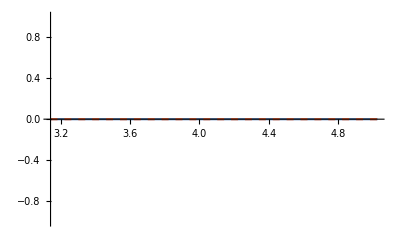
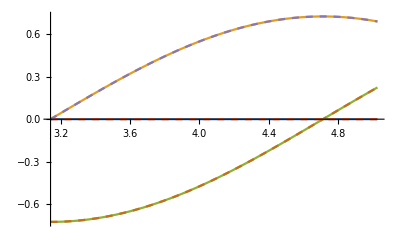

```mathematica
Array[
Plot[Evaluate[{
vaP[1,#][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T],vaPNumFulling[1,#][a,b,T][t]
}/.{a->1,b->1,T->1}],relevantdomain,PlotStyle->stylecompare2]&,
nk]
```

Second order:

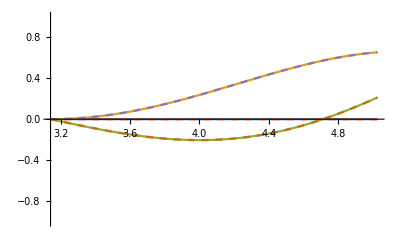
{-Graphics-,-Graphics-}

```mathematica
Array[
Plot[Evaluate[{
vaP[2,#][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T],vaPNumFulling[2,#][a,b,T][t]
}/.{a->1,b->1,T->1}],relevantdomain,PlotRange->{-1,1},PlotStyle->stylecompare2]&,
nk]
```

#### Prints of the normal (⊥) coefficients

All-orders normal (⊥) coefficients:

```mathematica
For[n=0,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
Print["vaNNumFulling[",n,",",k,"][a,b,T][t] = ",vaNNumFulling[n,k][a,b,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

vaNNumFulling[0,1][a,b,T][t] = (0
0
0)

vaNNumFulling[0,2][a,b,T][t] = (0
0
0)

vaNNumFulling[1,1][a,b,T][t] = (0
(b t Sin[b t])/((-1+t) √(a t))
-(b t Cos[b t])/((-1+t) √(a t)))

vaNNumFulling[1,2][a,b,T][t] = (0
0
0)

vaNNumFulling[2,1][a,b,T][t] = ((2 √(a t) ParametricFunction[<>][a,b,T]'[t])/(a-a t)
(Cos[b t] (5-5 t-16 b^2 t^2-48 b^2 t^3+64 (√(a t^5)-√(a t^7)) Cos[b π] ParametricFunction[<>][a,b,T]'[t]+64 (√(a t^5)-√(a t^7)) Sin[b π] ParametricFunction[<>][a,b,T]'[t]+64 b √(a t^5) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^7) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^5) Cos[b π] ParametricFunction[<>][a,b,T][t]+64 b √(a t^7) Cos[b π] ParametricFunction[<>][a,b,T][t]))/(32 a (-1+t)^2 t^2)
(Sin[b t] (5-5 t-16 b^2 t^2-48 b^2 t^3+64 (√(a t^5)-√(a t^7)) Cos[b π] ParametricFunction[<>][a,b,T]'[t]+64 (√(a t^5)-√(a t^7)) Sin[b π] ParametricFunction[<>][a,b,T]'[t]+64 b √(a t^5) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^7) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^5) Cos[b π] ParametricFunction[<>][a,b,T][t]+64 b √(a t^7) Cos[b π] ParametricFunction[<>][a,b,T][t]))/(32 a (-1+t)^2 t^2))

vaNNumFulling[2,2][a,b,T][t] = (0
-(2 Sin[b t] (Cos[b π] ParametricFunction[<>][a,b,T]'[t]-Sin[b π] ParametricFunction[<>][a,b,T]'[t]+b Sin[b π] ParametricFunction[<>][a,b,T][t]+b Cos[b π] ParametricFunction[<>][a,b,T][t]))/(√a (-1+t))
(2 Cos[b t] (Cos[b π] ParametricFunction[<>][a,b,T]'[t]-Sin[b π] ParametricFunction[<>][a,b,T]'[t]+b Sin[b π] ParametricFunction[<>][a,b,T][t]+b Cos[b π] ParametricFunction[<>][a,b,T][t]))/(√a (-1+t)))

#### Plots of the normal (⊥) coefficients

First order:

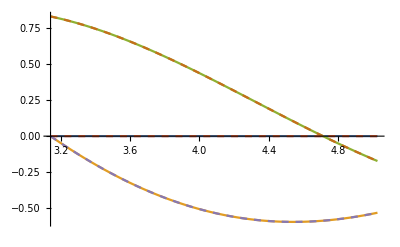
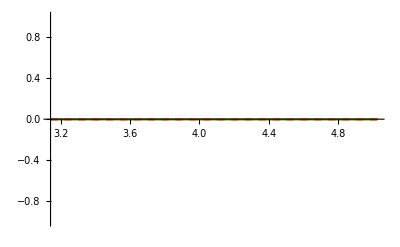

```mathematica
Array[
Plot[Evaluate[{
vaN[1,#][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T],vaNNumFulling[1,#][a,b,T][t]
}/.{a->1,b->1,T->1}],relevantdomain,PlotStyle->stylecompare2]&,
nk]
```

Second order:

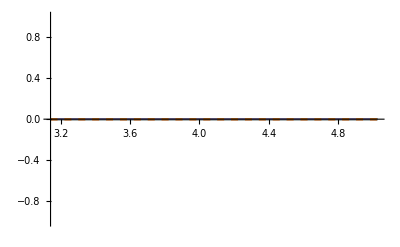
{-Graphics-,-Graphics-}

```mathematica
Array[
Plot[Evaluate[{
vaN[2,#][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T],vaNNumFulling[2,#][a,b,T][t]
}/.{a->1,b->1,T->1}],relevantdomain,PlotRange->{-1,1},PlotStyle->stylecompare]&,
nk]
```

#### Prints of the full (∥ + ⊥) coefficients

```mathematica
For[n=0,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
Print["vaNumFulling[",n,",",k,"][a,b,T][t] = ",vaNumFulling[n,k][a,b,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

vaNumFulling[0,1][a,b,T][t] = (0
1/2 (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)])
1/2 (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))

vaNumFulling[0,2][a,b,T][t] = (0
0
0)

vaNumFulling[1,1][a,b,T][t] = (ParametricFunction[<>][a,b,T][t]
((1/π^(3/2)+4 ⅈ a^(1/4) T) Cos[b π] Cos[b (π-t)])/(8 √a)+((1/π^(3/2)+4 ⅈ a^(1/4) T) Sin[b π] Sin[b (π-t)])/(8 √a)+(b t Sin[b t])/((-1+t) √(a t))+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]+Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]
-(b t Cos[b t])/((-1+t) √(a t))+((1/π^(3/2)+4 ⅈ a^(1/4) T) Cos[b (π-t)] Sin[b π])/(8 √a)-((1/π^(3/2)+4 ⅈ a^(1/4) T) Cos[b π] Sin[b (π-t)])/(8 √a)-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t])

vaNumFulling[1,2][a,b,T][t] = (ParametricFunction[<>][a,b,T][t]
-(Cos[b (π-t)] Sin[b π] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+(Cos[b π] Sin[b (π-t)] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]
(Cos[b π] Cos[b (π-t)] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+(Sin[b π] Sin[b (π-t)] ((4 ⅈ (-π^(1/4) T Tan[b π]+π^(5/4) T Tan[b π]))/a^(1/4)+(4 b π+4 b π^2-Tan[b π]+π Tan[b π]+π^(3/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π]-π^(5/2) (1/π^(3/2)+4 ⅈ a^(1/4) T) Tan[b π])/(√a π^(5/4))))/(8 (-1+π))+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t])

vaNumFulling[2,1][a,b,T][t] = ((2 √(a t) ParametricFunction[<>][a,b,T]'[t])/(a-a t)+ParametricFunction[<>][a,b,T][t]
Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]+(Cos[b t] (5-5 t-16 b^2 t^2-48 b^2 t^3+64 (√(a t^5)-√(a t^7)) Cos[b π] ParametricFunction[<>][a,b,T]'[t]+64 (√(a t^5)-√(a t^7)) Sin[b π] ParametricFunction[<>][a,b,T]'[t]+64 b √(a t^5) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^7) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^5) Cos[b π] ParametricFunction[<>][a,b,T][t]+64 b √(a t^7) Cos[b π] ParametricFunction[<>][a,b,T][t]))/(32 a (-1+t)^2 t^2)
Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+(Sin[b t] (5-5 t-16 b^2 t^2-48 b^2 t^3+64 (√(a t^5)-√(a t^7)) Cos[b π] ParametricFunction[<>][a,b,T]'[t]+64 (√(a t^5)-√(a t^7)) Sin[b π] ParametricFunction[<>][a,b,T]'[t]+64 b √(a t^5) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^7) Sin[b π] ParametricFunction[<>][a,b,T][t]-64 b √(a t^5) Cos[b π] ParametricFunction[<>][a,b,T][t]+64 b √(a t^7) Cos[b π] ParametricFunction[<>][a,b,T][t]))/(32 a (-1+t)^2 t^2))

vaNumFulling[2,2][a,b,T][t] = (ParametricFunction[<>][a,b,T][t]
Cos[b (π-t)] ParametricFunction[<>][a,b,T][t]-(2 Sin[b t] (Cos[b π] ParametricFunction[<>][a,b,T]'[t]-Sin[b π] ParametricFunction[<>][a,b,T]'[t]+b Sin[b π] ParametricFunction[<>][a,b,T][t]+b Cos[b π] ParametricFunction[<>][a,b,T][t]))/(√a (-1+t))+Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]
-Sin[b (π-t)] ParametricFunction[<>][a,b,T][t]+(2 Cos[b t] (Cos[b π] ParametricFunction[<>][a,b,T]'[t]-Sin[b π] ParametricFunction[<>][a,b,T]'[t]+b Sin[b π] ParametricFunction[<>][a,b,T][t]+b Cos[b π] ParametricFunction[<>][a,b,T][t]))/(√a (-1+t))+Cos[b (π-t)] ParametricFunction[<>][a,b,T][t])

### Integrals in the higher order parallel (∥) recurrence relation (HOvaP) but keeping the exponents and normal (⊥) coefficients analytical

#### Semi-analytic (coefficients) parallel (∥) / normal (⊥) decomposition

```mathematica
Definition[va]
```

va[n_,k_][a_,b_,T_][t_]=vaN[n,k][a,b,T][t]+vaP[n,k][a,b,T][t]

```mathematica
vaNumCoeffsFulling[n_,k_][a_,b_,T_][t_]:=vaN[n,k][a,b,T][t]+vaPNumFulling[n,k][a,b,T][t]/.j->ⅈ/.constsFulling[a,b,T]
```

#### Semi-analytic solutions

Semi-analytic vector adiabatic ansatz function:

```mathematica
VecAdbAnsatzNumCoeffsFulling[o_,k_][a_,b_,T_][t_]:=(p[k][a,b][t])^(-1/4) Exp[j T (∫√(p[k][a,b][t])ⅆt+iph[k][a,b])] ∑_(n=0)^o (j T)^-n vaNumCoeffsFulling[n,k][a,b,T][t]
```

Semi-analytic vector adiabatic general expansion function:

```mathematica
VecAdbGralExpNumCoeffsFulling[o_][a_,b_,T_][t_]:=(∑_(k=1)^nk VecAdbAnsatzNumCoeffsFulling[o,k][a,b,T][t]/.j->+ⅈ)+(∑_(k=1)^nk VecAdbAnsatzNumCoeffsFulling[o,k][a,b,T][t]/.j->-ⅈ)
```

Semi-analytic adiabatic solution:

```mathematica
For[n=0,n<=adbOrd,n++,
vxAdbNumCoeffsFulling[n][a_,b_,T_][t_]=VecAdbGralExpNumCoeffsFulling[n][a,b,T][t]//.constsFulling[a,b,T]]
ClearAll[n]
```

## Semi-analytic (coefficients) solution plots (T-manipulative)

### 0th order semi-analytic adiabatic solution

#### Static plot for {a → 1, b → 1, T → 10}

```mathematica
vxAdbNumCoeffsFulling[0][a,b,T][t]
```

{0,(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4)),(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))}

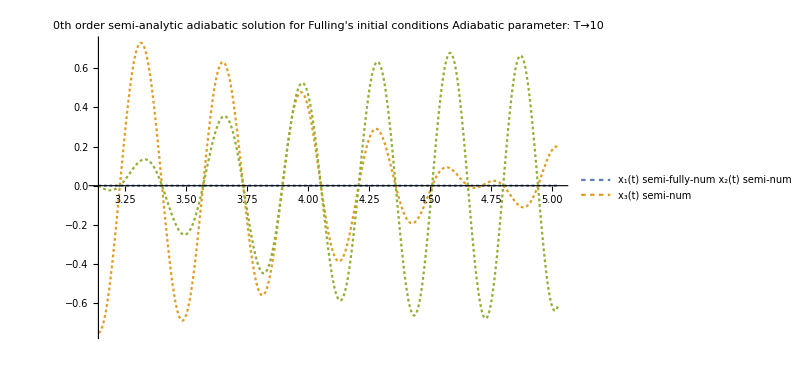

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->style0th,
PlotLegends->{"x_1(t) semi-fully-num""x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->style0th,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 1st order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

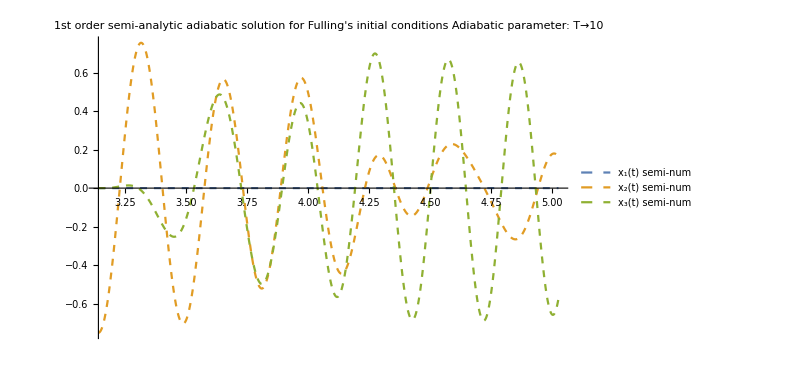

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->style1st,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->style1st,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 2nd order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

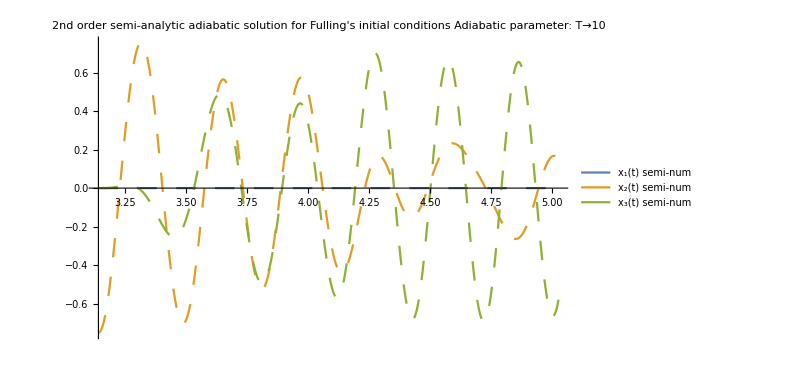

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->style2nd,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->style2nd,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order semi-analytic adiabatic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Altogether (0th, 1st and 2nd order, semi-analytic adiabatic solutions)

#### Static plot for {a → 1, b → 1, T → 10}

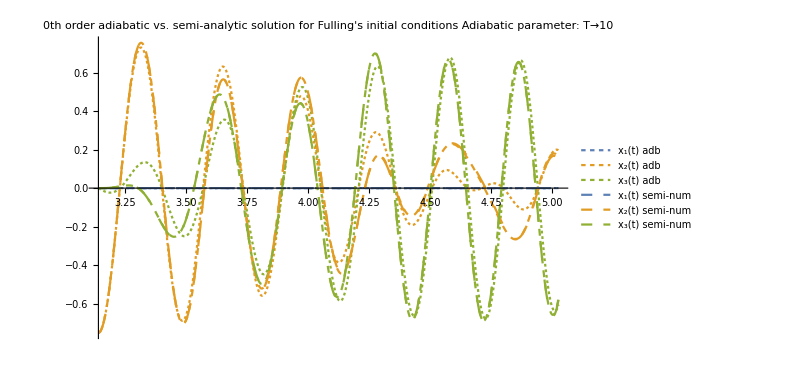

```mathematica
Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order adiabatic vs. semi-analytic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{"x_1(t) adb","x_2(t) adb","x_3(t) adb","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order adiabatic vs. semi-analytic solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Comparing the adiabatic and semi-analytic (coefficients) solutions

### 0th order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

```mathematica
vxAdbNumCoeffsFulling[0][a,b,T][t]
```

{0,(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b π] Cos[b (π-t)]+Sin[b π] Sin[b (π-t)]))/(2 (a t)^(1/4)),(ⅇ^(-ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))+(ⅇ^(ⅈ (-2/3 √a π^(3/2)+2/3 t √(a t)) T) (Cos[b (π-t)] Sin[b π]-Cos[b π] Sin[b (π-t)]))/(2 (a t)^(1/4))}

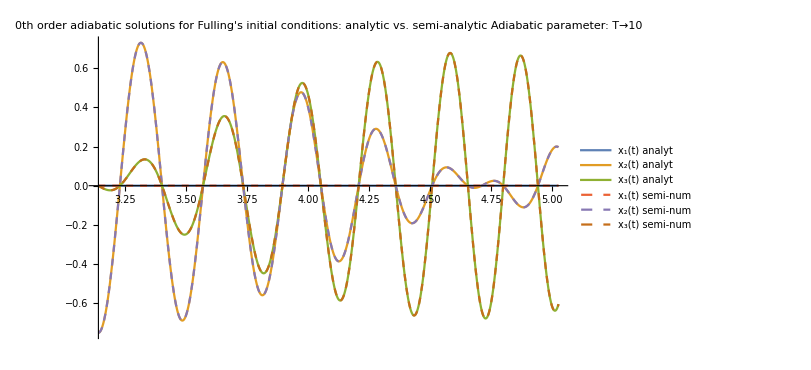

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{
"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt",
"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"0th order analytic vs. semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 1st order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

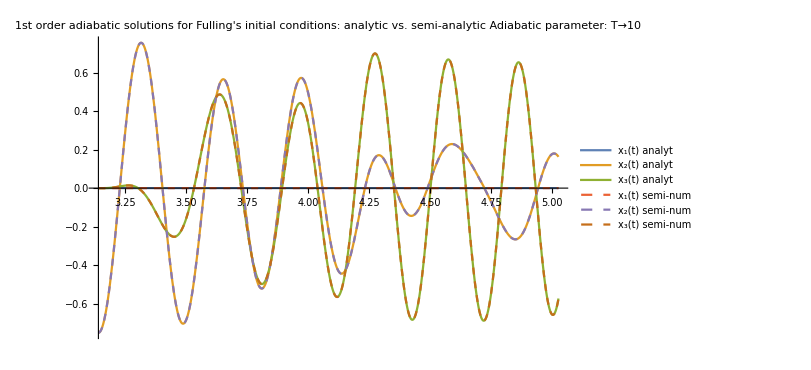

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{
"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt",
"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"1st order analytic vs. semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### 2nd order adiabatic solution vs. semi-analytic

#### Static plot for {a → 1, b → 1, T → 10}

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt","x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

-Graphics-

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{
"x_1(t) analyt","x_2(t) analyt","x_3(t) analyt",
"x_1(t) semi-num","x_2(t) semi-num","x_3(t) semi-num"},
PlotLabel->"2nd order analytic vs. semi-analytic adiabatic solution for Fulling's initial conditions
Adiabatic parameter: T"->10,
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Altogether (0th, 1st and 2nd order solutions, adiabatic vs. semi-analytic)

#### Static plot for {a → 1, b → 1, T → 10}

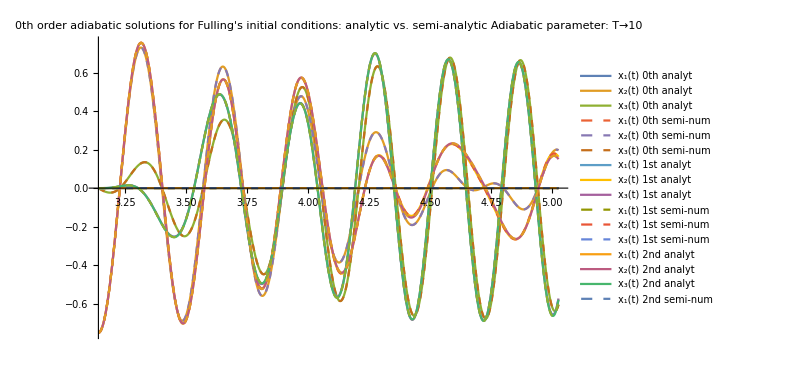

```mathematica
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) 0th analyt","x_2(t) 0th analyt","x_3(t) 0th analyt",
"x_1(t) 0th semi-num","x_2(t) 0th semi-num","x_3(t) 0th semi-num",
"x_1(t) 1st analyt","x_2(t) 1st analyt","x_3(t) 1st analyt",
"x_1(t) 1st semi-num","x_2(t) 1st semi-num","x_3(t) 1st semi-num",
"x_1(t) 2nd analyt","x_2(t) 2nd analyt","x_3(t) 2nd analyt",
"x_1(t) 2nd semi-num","x_2(t) 2nd semi-num","x_3(t) 2nd semi-num"
},
PlotLabel->"0th order adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600]
```

I plot this because they seemed too similar, but that’s because for T → 10 they are similar (although not exactly the same, as we can see here).

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[1]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[2]]],Re[vxAdbNumCoeffsFulling[2][a,b,T][t][[3]]]}/.T->10
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->stylecompare2,
PlotLegends->{"x_1(t) 0th analyt","x_2(t) 0th analyt","x_3(t) 0th analyt",
"x_1(t) 0th semi-num","x_2(t) 0th semi-num","x_3(t) 0th semi-num",
"x_1(t) 1st analyt","x_2(t) 1st analyt","x_3(t) 1st analyt",
"x_1(t) 1st semi-num","x_2(t) 1st semi-num","x_3(t) 1st semi-num",
"x_1(t) 2nd analyt","x_2(t) 2nd analyt","x_3(t) 2nd analyt",
"x_1(t) 2nd semi-num","x_2(t) 2nd semi-num","x_3(t) 2nd semi-num"
},
PlotLabel->"All orders adiabatic solutions for Fulling's initial conditions:
analytic vs. semi-analytic
Adiabatic parameter: T"->10,
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

## Semi-analytic (coefficients) Klein-Gordon norm

### Semi-analytic (coefficients) solutions

#### Computation

```mathematica
kgNormAdbNumCoeffsFulling[0][a_,b_,T_]=KleinGordonNorm[vxAdbNumCoeffsFulling[0][a,b,T][t]];
kgNormAdbNumCoeffsFulling[1][a_,b_,T_]=KleinGordonNorm[vxAdbNumCoeffsFulling[1][a,b,T][t]];
kgNormAdbNumCoeffsFulling[2][a_,b_,T_]=KleinGordonNorm[vxAdbNumCoeffsFulling[2][a,b,T][t]];
```

#### Static plot for {a → 1, b → 1, T → 10}

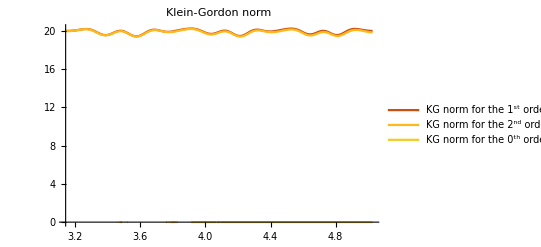

```mathematica
Plot[Evaluate[
{kgNormAdbNumCoeffsFulling[1][a,b,T],kgNormAdbNumCoeffsFulling[2][a,b,T],kgNormAdbNumCoeffsFulling[0][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution","KG norm for the
0^th order solution"}]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[{kgNormAdbNumCoeffsFulling[1][a,b,T],kgNormAdbNumCoeffsFulling[2][a,b,T],kgNormAdbNumCoeffsFulling[0][a,b,T]},{t,Start,Start+WindowSize},
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution","KG norm for the
0^th order solution"}],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

### Comparisons for {a → 1, b → 1, T → 10}

#### Comparison: analytical vs. semi-analytic (coefficients) norms ({a → 1, b → 1, T → 10})

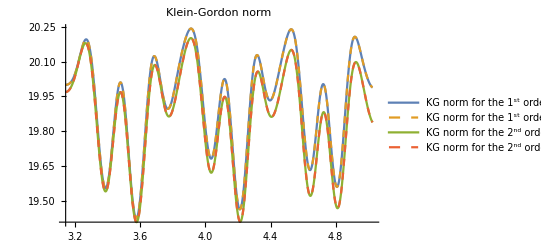

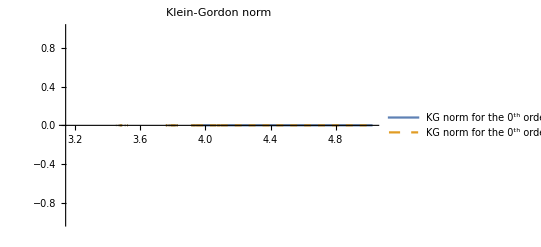

```mathematica
Plot[Evaluate[{
kgNormAdbFulling[1][a,b,T],kgNormAdbNumCoeffsFulling[1][a,b,T],
kgNormAdbFulling[2][a,b,T],kgNormAdbNumCoeffsFulling[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->stylecompare,
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution - Analytical","KG norm for the
1^st order solution - semi-analytic (coefficients)","KG norm for the
2^nd order solution - Analytical","KG norm for the
2^nd order solution - semi-analytic (coefficients)"}]
Plot[Evaluate[{
kgNormAdbFulling[0][a,b,T],
kgNormAdbNumCoeffsFulling[0][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,
PlotStyle->stylecompare,
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
0^th order solution - Analytical","KG norm for the
0^th order solution - semi-analytic (coefficients)"}]
```

### Normalized plots (for {a → 1, b → 1, T → 10})

#### Initial norms

```mathematica
kgNormAdbNumCoeffsFullingti[0][a_,b_,T_]=Re[kgNormAdbNumCoeffsFulling[0][a,b,T]/.t->ti];
kgNormAdbNumCoeffsFullingti[1][a_,b_,T_]=Re[kgNormAdbNumCoeffsFulling[1][a,b,T]/.t->ti];
kgNormAdbNumCoeffsFullingti[2][a_,b_,T_]=Re[kgNormAdbNumCoeffsFulling[2][a,b,T]/.t->ti];
```

#### Semi-analytic (coefficients) (1st & 2nd orders)

```mathematica
Plot[Evaluate[{
kgNormAdbNumCoeffsFulling[1][a,b,T]/kgNormAdbNumCoeffsFullingti[1][a,b,T],kgNormAdbNumCoeffsFulling[2][a,b,T]/kgNormAdbNumCoeffsFullingti[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->ColorData[35,"ColorList"],
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution"}]
```

-Graphics-

#### Comparison (adiabatic analytical vs. semi-analytic (coefficients))

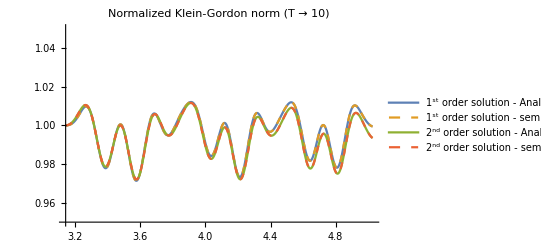

```mathematica
Plot[Evaluate[{
kgNormAdbFulling[1][a,b,T]/kgNormAdbFullingti[1][a,b,T],kgNormAdbNumCoeffsFulling[1][a,b,T]/kgNormAdbNumCoeffsFullingti[1][a,b,T],
kgNormAdbFulling[2][a,b,T]/kgNormAdbFullingti[2][a,b,T],kgNormAdbNumCoeffsFulling[2][a,b,T]/kgNormAdbNumCoeffsFullingti[2][a,b,T]}/.{a->1,b->1,T->10}
],relevantdomain,PlotRange->{0.95,1.05},
PlotStyle->stylecompare,
PlotLabel->"Normalized Klein-Gordon norm (T → 10)",
PlotLegends->{"1^st order solution - Analytical","1^st order solution - semi-analytic (coefficients)","2^nd order solution - Analytical","2^nd order solution - semi-analytic (coefficients)"}]
```

## Representative plots: WKB approximation vs. exact (numerical) solution

### Full comparison: 0th vs. 1st vs. 2nd adiabatic orders vs. exact (numerical) solution

#### Static plot for {a → 1, b → 1, T → 3}

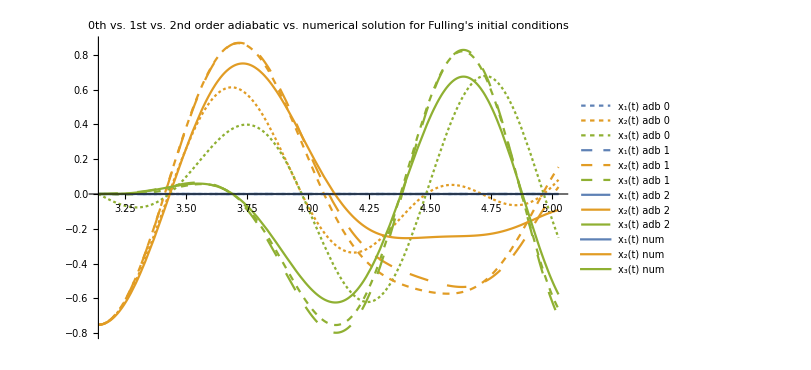

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vxAdbFulling[0][a,b,T][t][[1]]],Re[vxAdbFulling[0][a,b,T][t][[2]]],Re[vxAdbFulling[0][a,b,T][t][[3]]],
Re[vxAdbFulling[1][a,b,T][t][[1]]],Re[vxAdbFulling[1][a,b,T][t][[2]]],Re[vxAdbFulling[1][a,b,T][t][[3]]],
Re[vxAdbFulling[2][a,b,T][t][[1]]],Re[vxAdbFulling[2][a,b,T][t][[2]]],Re[vxAdbFulling[2][a,b,T][t][[3]]],
Re[x[1][a,b,T][t]],Re[x[2][a,b,T][t]],Re[x[3][a,b,T][t]]}/.solFullNumFulling
],{t,Start,Start+WindowSize},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0","x_3(t) adb 0",
"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1",
"x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2",
"x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic vs. numerical solution for Fulling's initial conditions",
ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01}]
```

#### All integration constants manipulable

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
VecAdbGralExp[0][a,b,T][t],VecAdbGralExp[1][a,b,T][t],VecAdbGralExp[2][a,b,T][t]}/.{a->1,b->1}/.constsTest[c011p,c011m,c012p,c012m,c02p,c02m,c111p,c111m,c112p,c112m,c12p,c12m,c211p,c211m,c212p,c212m,c22p,c22m]
],{t,Start,Start+WindowSize},
PlotRange->All,PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{"x_1(t) adb 1","x_2(t) adb 1","x_3(t) adb 1","x_1(t) adb 2","x_2(t) adb 2","x_3(t) adb 2","x_1(t) num","x_2(t) num","x_3(t) num"},
PlotLabel->"1st vs. 2nd order adiabatic vs. numerical solution for Fulling's initial conditions",ImageSize->600],
Style["Parameters",12],{{a,1},0.1,10},{{b,1},0.1,10},Style["
Adiabatic regime",12],{{T,10},0.1,Tmax},Style["
Manipulate graph",12],{{WindowSize,tf-ti,"⟷ "},0.01,tmax/10},{{Start,ti," ←  →"},tmin,tmax-WindowSize-0.01},Style["
Integration constants",12],{{c011p,0},-2,2},{{c011m,0},-2,2},{{c012p,1},-2,2},{{c012m,1},-2,2},{{c02p,1},-2,2},{{c02m,1},-2,2},{{c111p,0},-2,2},{{c111m,0},-2,2},{{c112p,1},-2,2},{{c112m,1},-2,2},{{c12p,1},-2,2},{{c12m,1},-2,2},{{c211p,0},-2,2},{{c211m,0},-2,2},{{c212p,1},-2,2},{{c212m,1},-2,2},{{c22p,1},-2,2},{{c22m,1},-2,2}]
```